## Omni Robot

In this note book the Vector tools by Dr. Alan A Barhorst was used. Please contact him via alan.barhorst@louisiana.edu for it. 
You can cite the work of this notebook using: 
Amarasiri, N., Barhorst, A.A. and Gottumukkala, R., 2022. Robust Dynamic Modeling and Trajectory Tracking Controller of a Universal Omni-Wheeled Mobile Robot. ASME Letters in Dynamic Systems and Control, 2(4), p.040902.
DOI: 10.1115/1.4055690

This paper can be downloaded using https://www.researchgate.net/profile/Nalaka-Amarasiri

Please cite the vector tools by using:
Barhorst, A. A., 1997, “Symbolic Equation Processing Utilizing Vector/Dyad Notation,” J. Sound Vib., 208(5), pp. 823–839.

## Graphics

### Start Parallel Processes and Load the vector tools

For the moment I will keep the omni wheels aside and will work on it after this simulation

```mathematica
<<"/Users/nalakaamarasiri/Desktop/vectorDefsMM30.m" (*This is the vector tools by Dr. Alan A Barhorst. Please contact him from alan.barhorst@louisiana.edu*)
```

These Engineering Vector algorithms are copyright Alan A. Barhorst

```mathematica
ParallelEvaluate[$ProcessID]
```

{2338,2339,2340,2341,2342,2343,2344,2345}

```mathematica
ParallelEvaluate[$MachineName]
```

{Nalakas-Air,Nalakas-Air,Nalakas-Air,Nalakas-Air,Nalakas-Air,Nalakas-Air,Nalakas-Air,Nalakas-Air}

```mathematica
ParallelEvaluate[<<"/Users/nalakaamarasiri/Desktop/vectorDefsMM30.m"]
```

These Engineering Vector algorithms are copyright Alan A. Barhorst

These Engineering Vector algorithms are copyright Alan A. Barhorst

These Engineering Vector algorithms are copyright Alan A. Barhorst

«5 more identical outputs»

{Null,Null,Null,Null,Null,Null,Null,Null}

Turn off a warning message that is the result of one of the vector tools functions.

```mathematica
ParallelEvaluate[Off[ReplaceRepeated::"rrlim"]]
```

{Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Off[ReplaceRepeated::"rrlim"]
```

### Typical rotations

Generic 0 rotation (Identity)

```mathematica
rot0[q_:1]={{1,0,0},{0,1,0},
		            {0,0,1}};MatrixForm [rot0[ ]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Generic 1 rotation

```mathematica
rot1[q_]={{1,0,0},{0,Cos[q],Sin[q]},
		            {0,-Sin[q],Cos[q]}};MatrixForm [rot1[Subscript[q, 1][t]]]
```

(1 | 0 | 0
0 | Cos[q_1[t]] | Sin[q_1[t]]
0 | -Sin[q_1[t]] | Cos[q_1[t]])

Generic rotation 2

```mathematica
rot2[q_]={{Cos[q],0,-Sin[q]},{0,1,0},{Sin[q],0,Cos[q]}};
MatrixForm[rot2[Subscript[q, 2][t]]]
```

(Cos[q_2[t]] | 0 | -Sin[q_2[t]]
0 | 1 | 0
Sin[q_2[t]] | 0 | Cos[q_2[t]])

Generic Rotation 3

```mathematica
rot3[q_]={{Cos[q],Sin[q],0},{-Sin[q],Cos[q],0},{0,0,1}};
MatrixForm[rot3[Subscript[q, 3][t]]]
```

(Cos[q_3[t]] | Sin[q_3[t]] | 0
-Sin[q_3[t]] | Cos[q_3[t]] | 0
0 | 0 | 1)

### Define the symbols used for unit vectors and unit Dyads

```mathematica
a[x_]:=unitVector[A,a,x]
b[x_]:=unitVector[B,b,x]
c[x_]:=unitVector[C,c,x]
d[x_]:=unitVector[D,d,x]
e[x_]:=unitVector[E,e,x]
f[x_]:=unitVector[F,f,x]
g[x_]:=unitVector[G,g,x]
h[x_]:=unitVector[H,h,x]
l[x_]:=unitVector[L,l,x]
m[x_]:=unitVector[M,m,x]
p[x_]:=unitVector[P,p,x]
s[x_]:=unitVector[S,s,x]
n[x_]:=unitVector[N,n,x]
w[x_]:=unitVector[W,w,x]
aa[x_,y_]:=unitDyad[a[x],a[y]]
bb[x_,y_]:=unitDyad[b[x],b[y]]
cc[x_,y_]:=unitDyad[c[x],c[y]]
dd[x_,y_]:=unitDyad[d[x],d[y]]
ee[x_,y_]:=unitDyad[e[x],e[y]]
ff[x_,y_]:=unitDyad[f[x],f[y]]
gg[x_,y_]:=unitDyad[g[x],g[y]]
hh[x_,y_]:=unitDyad[h[x],h[y]]
ll[x_,y_]:=unitDyad[l[x],l[y]]
mm[x_,y_]:=unitDyad[m[x],m[y]]
pp[x_,y_]:=unitDyad[p[x],p[y]]
ss[x_,y_]:=unitDyad[s[x],s[y]]
ww[x_,y_]:=unitDyad[w[x],w[y]]
```

### Robot graphic

#### Base

```mathematica
vecL=3;
```

```mathematica
widthBase=8;depthBase=8;heightBase=1;
```

```mathematica
baseShape=Cuboid[
{-widthBase/2,-depthBase/2,-heightBase/2},
{widthBase/2,depthBase/2,heightBase/2}];
```

```mathematica
baseGraphic={{Opacity[1],baseShape},
{
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[baseGraphic],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 1st wheel

```mathematica
vecL=2;
```

```mathematica
halfHeightwheel=0.4;
wheelBase={0,0,-halfHeightwheel};
wheelTop={0,0,halfHeightwheel};
wheelRadius=3;
```

```mathematica
wheelshape1=Cylinder[{wheelBase,wheelTop},wheelRadius];
```

```mathematica
Show[Graphics3D[{Glow[Red],wheelshape1}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wheelGraphic1={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
wheelGraphic11={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
Show[Graphics3D[{Glow[Red],wheelGraphic11}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wheelGraphic1={Rotate[{Opacity[0.1],wheelGraphic11},Pi/2,{0,0,1}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Red],wheelGraphic1}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Barrels for wheels 1 and 2

```mathematica
halfHeightbarrel=0.60;
barrelBase={0,0,-halfHeightbarrel};
barrelTop={0,0,halfHeightbarrel};
barrelRadius=0.4;
```

```mathematica
barrelGraphic1={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Red],barrelGraphic1}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic2={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/2,{0,0,1}]};
```

```mathematica
Show[Graphics3D[{Glow[Red],barrelGraphic2}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic3={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/4,{0,1,0}]};
Show[Graphics3D[{Glow[Red],barrelGraphic3}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic4={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],3Pi/4,{0,1,0}]};
Show[Graphics3D[{Glow[Red],barrelGraphic4}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
barrelGraphic5={Rotate[Cylinder[{barrelBase,barrelTop},barrelRadius],Pi/2,{0,1,0}]};
Show[Graphics3D[{Glow[Red],barrelGraphic5}],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 1

```mathematica
comwheelGraphic1=
(*Base*){Translate[wheelGraphic1,{0,0, 0}],

(*barrel 1*)Translate[barrelGraphic1,{0wheelRadius,0halfHeightwheel,-(wheelRadius-barrelRadius)}],
(*barrel 2*)GeometricTransformation[Translate[barrelGraphic3,{(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 3*)Translate[barrelGraphic5,{0,0halfHeightwheel,(wheelRadius-barrelRadius)}],
(*barrel 4*)Translate[barrelGraphic2,{-(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 5*)Translate[barrelGraphic2,{(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 6*)GeometricTransformation[Translate[barrelGraphic3,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 7*)GeometricTransformation[Translate[barrelGraphic4,{(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 8*)GeometricTransformation[Translate[barrelGraphic4,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]]
};
Show[Graphics3D[comwheelGraphic1],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 2nd wheel

```mathematica
wheelGraphic2={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{1,0,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Yellow],wheelGraphic11}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 2

```mathematica
comwheelGraphic2=
(*Base*){Translate[wheelGraphic2,{0,0, 0}],

(*barrel 1*)Translate[barrelGraphic5,{0wheelRadius,0halfHeightwheel,-(wheelRadius-barrelRadius)}],
(*barrel 2*)GeometricTransformation[Translate[barrelGraphic3,{(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 3*)Translate[barrelGraphic5,{0,0halfHeightwheel,(wheelRadius-barrelRadius)}],
(*barrel 4*)Translate[barrelGraphic2,{-(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 5*)Translate[barrelGraphic2,{(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 6*)GeometricTransformation[Translate[barrelGraphic3,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 7*)GeometricTransformation[Translate[barrelGraphic4,{(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 8*)GeometricTransformation[Translate[barrelGraphic4,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]]
};
Show[Graphics3D[comwheelGraphic2],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 3rd wheel

```mathematica
wheelGraphic3={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Green],wheelGraphic3}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
Barrelring=
{(*barrel 1*)Translate[barrelGraphic5,{0wheelRadius,0halfHeightwheel,-(wheelRadius-barrelRadius)}],
(*barrel 2*)GeometricTransformation[Translate[barrelGraphic3,{(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 3*)Translate[barrelGraphic5,{0,0halfHeightwheel,(wheelRadius-barrelRadius)}],
(*barrel 4*)Translate[barrelGraphic2,{-(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 5*)Translate[barrelGraphic2,{(wheelRadius-barrelRadius),0halfHeightwheel,0}],
(*barrel 6*)GeometricTransformation[Translate[barrelGraphic3,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 7*)GeometricTransformation[Translate[barrelGraphic4,{(wheelRadius-barrelRadius)Cos[Pi/4],0,(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]],
(*barrel 8*)GeometricTransformation[Translate[barrelGraphic4,{-(wheelRadius-barrelRadius)Cos[Pi/4],0,-(wheelRadius-barrelRadius)Sin[Pi/4]}],RotationTransform[0Degree,{1,1,0}]]
};
Show[Graphics3D[Barrelring],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 3

```mathematica
comwheelGraphic3=
{(*Base*)Translate[wheelGraphic3,{0,0, 0}],

(*Barrel ring*)Translate[Rotate[Barrelring,Pi/2,{0,0,1}],{0wheelRadius,0halfHeightwheel,0(wheelRadius-barrelRadius)}]
};
Show[Graphics3D[comwheelGraphic3],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### 4th wheel

```mathematica
wheelGraphic4={Rotate[{Opacity[0.1],wheelshape1},Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Blue],wheelGraphic4}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Combined wheel 4

```mathematica
comwheelGraphic4=
{(*Base*)Translate[wheelGraphic4,{0,0, 0}],

(*Barrel ring*)Translate[Rotate[Barrelring,Pi/2,{0,0,1}],{0wheelRadius,0halfHeightwheel,0(wheelRadius-barrelRadius)}]
};
Show[Graphics3D[comwheelGraphic4],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Graphic

```mathematica
robotGraphic1=
(*Base*){Translate[baseGraphic,{0,0, 0}],

(*wheel 1*)Translate[comwheelGraphic1,{0widthBase,(0.5 depthBase+halfHeightwheel),-0.4heightBase}],

(*wheel 2*)Translate[comwheelGraphic2,{ 0widthBase,-(0.5 depthBase+halfHeightwheel),-0.4 heightBase}],

(*wheel 3*)Translate[comwheelGraphic3,{(0.5widthBase+halfHeightwheel),0 depthBase,-0.4 heightBase}],

(*wheel 4*)Translate[comwheelGraphic4,{ -(0.5widthBase+halfHeightwheel),0depthBase,-0.4heightBase}]
};
Show[Graphics3D[robotGraphic1],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

### Rotations

```mathematica
rotA=rot3[Subscript[q, 3][t]];
AtoN=rotA.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(n̂)_3}

```mathematica
TransAtoN[x_]:=x//.{a[1]-> AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]}
```

```mathematica
{a[1]->AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]}
```

{(â)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(â)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(â)_3→(n̂)_3}

------------------------------------------------Wheel--------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 1

```mathematica
rotB=rot2[Subscript[q, 4][t]].rotA;
BtoN=rotB.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_4[t]] (n̂)_1+Cos[q_4[t]] Sin[q_3[t]] (n̂)_2-Sin[q_4[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_4[t]] (n̂)_1+Sin[q_3[t]] Sin[q_4[t]] (n̂)_2+Cos[q_4[t]] (n̂)_3}

```mathematica
TransBtoN[x_]:=x//.{b[1]->BtoN[[1]],b[2]->BtoN[[2]],b[3]->BtoN[[3]]}
{b[1]->BtoN[[1]],b[2]->BtoN[[2]],b[3]->BtoN[[3]]}
```

{(b̂)_1→Cos[q_3[t]] Cos[q_4[t]] (n̂)_1+Cos[q_4[t]] Sin[q_3[t]] (n̂)_2-Sin[q_4[t]] (n̂)_3,(b̂)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(b̂)_3→Cos[q_3[t]] Sin[q_4[t]] (n̂)_1+Sin[q_3[t]] Sin[q_4[t]] (n̂)_2+Cos[q_4[t]] (n̂)_3}

```mathematica
rotC=rot1[Subscript[q, 5][t]].rotA;
CtoN=rotC.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_5[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_5[t]] (n̂)_2+Sin[q_5[t]] (n̂)_3,Sin[q_3[t]] Sin[q_5[t]] (n̂)_1-Cos[q_3[t]] Sin[q_5[t]] (n̂)_2+Cos[q_5[t]] (n̂)_3}

```mathematica
TransCtoN[x_]:=x//.{c[1]->CtoN[[1]],c[2]->CtoN[[2]],c[3]->CtoN[[3]]}
{c[1]->CtoN[[1]],c[2]->CtoN[[2]],c[3]->CtoN[[3]]}
```

{(ĉ)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(ĉ)_2→-Cos[q_5[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_5[t]] (n̂)_2+Sin[q_5[t]] (n̂)_3,(ĉ)_3→Sin[q_3[t]] Sin[q_5[t]] (n̂)_1-Cos[q_3[t]] Sin[q_5[t]] (n̂)_2+Cos[q_5[t]] (n̂)_3}

#### Wheel 2

```mathematica
rotD=rot2[Subscript[q, 6][t]].rotA;
```

```mathematica
DtoN=rotD.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_6[t]] (n̂)_1+Cos[q_6[t]] Sin[q_3[t]] (n̂)_2-Sin[q_6[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_6[t]] (n̂)_1+Sin[q_3[t]] Sin[q_6[t]] (n̂)_2+Cos[q_6[t]] (n̂)_3}

```mathematica
TransDtoN[x_]:=x//.{d[1]->DtoN[[1]],d[2]->DtoN[[2]],d[3]->DtoN[[3]]}
{d[1]->DtoN[[1]],d[2]->DtoN[[2]],d[3]->DtoN[[3]]}
```

{(d̂)_1→Cos[q_3[t]] Cos[q_6[t]] (n̂)_1+Cos[q_6[t]] Sin[q_3[t]] (n̂)_2-Sin[q_6[t]] (n̂)_3,(d̂)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(d̂)_3→Cos[q_3[t]] Sin[q_6[t]] (n̂)_1+Sin[q_3[t]] Sin[q_6[t]] (n̂)_2+Cos[q_6[t]] (n̂)_3}

```mathematica
rotE=rot1[Subscript[q, 7][t]].rotA;
EtoN=rotE.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_7[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_7[t]] (n̂)_2+Sin[q_7[t]] (n̂)_3,Sin[q_3[t]] Sin[q_7[t]] (n̂)_1-Cos[q_3[t]] Sin[q_7[t]] (n̂)_2+Cos[q_7[t]] (n̂)_3}

```mathematica
TransEtoN[x_]:=x//.{e[1]->EtoN[[1]],e[2]->EtoN[[2]],e[3]->EtoN[[3]]}
{e[1]->EtoN[[1]],e[2]->EtoN[[2]],e[3]->EtoN[[3]]}
```

{(ê)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(ê)_2→-Cos[q_7[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_7[t]] (n̂)_2+Sin[q_7[t]] (n̂)_3,(ê)_3→Sin[q_3[t]] Sin[q_7[t]] (n̂)_1-Cos[q_3[t]] Sin[q_7[t]] (n̂)_2+Cos[q_7[t]] (n̂)_3}

#### Wheel 3

```mathematica
rotF=rot1[Subscript[q, 8][t]].rotA;
```

```mathematica
FtoN=rotF.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_8[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_8[t]] (n̂)_2+Sin[q_8[t]] (n̂)_3,Sin[q_3[t]] Sin[q_8[t]] (n̂)_1-Cos[q_3[t]] Sin[q_8[t]] (n̂)_2+Cos[q_8[t]] (n̂)_3}

```mathematica
TransFtoN[x_]:=x//.{f[1]->FtoN[[1]],f[2]->FtoN[[2]],f[3]->FtoN[[3]]}
{f[1]->FtoN[[1]],f[2]->FtoN[[2]],f[3]->FtoN[[3]]}
```

{(f̂)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(f̂)_2→-Cos[q_8[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_8[t]] (n̂)_2+Sin[q_8[t]] (n̂)_3,(f̂)_3→Sin[q_3[t]] Sin[q_8[t]] (n̂)_1-Cos[q_3[t]] Sin[q_8[t]] (n̂)_2+Cos[q_8[t]] (n̂)_3}

```mathematica
rotG=rot2[Subscript[q, 9][t]].rotA;
GtoN=rotG.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_9[t]] (n̂)_1+Cos[q_9[t]] Sin[q_3[t]] (n̂)_2-Sin[q_9[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_9[t]] (n̂)_1+Sin[q_3[t]] Sin[q_9[t]] (n̂)_2+Cos[q_9[t]] (n̂)_3}

```mathematica
TransGtoN[x_]:=x//.{g[1]->GtoN[[1]],g[2]->GtoN[[2]],g[3]->GtoN[[3]]}
{g[1]->GtoN[[1]],g[2]->GtoN[[2]],g[3]->GtoN[[3]]}
```

{(ĝ)_1→Cos[q_3[t]] Cos[q_9[t]] (n̂)_1+Cos[q_9[t]] Sin[q_3[t]] (n̂)_2-Sin[q_9[t]] (n̂)_3,(ĝ)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(ĝ)_3→Cos[q_3[t]] Sin[q_9[t]] (n̂)_1+Sin[q_3[t]] Sin[q_9[t]] (n̂)_2+Cos[q_9[t]] (n̂)_3}

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 4

```mathematica
rotH=rot1[Subscript[q, 10][t]].rotA;
```

```mathematica
HtoN=rotH.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,-Cos[q_10[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_10[t]] (n̂)_2+Sin[q_10[t]] (n̂)_3,Sin[q_3[t]] Sin[q_10[t]] (n̂)_1-Cos[q_3[t]] Sin[q_10[t]] (n̂)_2+Cos[q_10[t]] (n̂)_3}

```mathematica
TransHtoN[x_]:=x//.{h[1]->HtoN[[1]],h[2]->HtoN[[2]],h[3]->HtoN[[3]]}
{h[1]->HtoN[[1]],h[2]->HtoN[[2]],h[3]->HtoN[[3]]}
```

{(ĥ)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(ĥ)_2→-Cos[q_10[t]] Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] Cos[q_10[t]] (n̂)_2+Sin[q_10[t]] (n̂)_3,(ĥ)_3→Sin[q_3[t]] Sin[q_10[t]] (n̂)_1-Cos[q_3[t]] Sin[q_10[t]] (n̂)_2+Cos[q_10[t]] (n̂)_3}

```mathematica
rotL=rot2[Subscript[q, 11][t]].rotA;
LtoN=rotL.{n[1],n[2],n[3]}
```

{Cos[q_3[t]] Cos[q_11[t]] (n̂)_1+Cos[q_11[t]] Sin[q_3[t]] (n̂)_2-Sin[q_11[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,Cos[q_3[t]] Sin[q_11[t]] (n̂)_1+Sin[q_3[t]] Sin[q_11[t]] (n̂)_2+Cos[q_11[t]] (n̂)_3}

```mathematica
TransLtoN[x_]:=x//.{l[1]->LtoN[[1]],l[2]->LtoN[[2]],l[3]->LtoN[[3]]}
{l[1]->LtoN[[1]],l[2]->LtoN[[2]],l[3]->LtoN[[3]]}
```

{(l̂)_1→Cos[q_3[t]] Cos[q_11[t]] (n̂)_1+Cos[q_11[t]] Sin[q_3[t]] (n̂)_2-Sin[q_11[t]] (n̂)_3,(l̂)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(l̂)_3→Cos[q_3[t]] Sin[q_11[t]] (n̂)_1+Sin[q_3[t]] Sin[q_11[t]] (n̂)_2+Cos[q_11[t]] (n̂)_3}

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

### Relative position vectors

```mathematica
Show[Graphics3D[robotGraphic1,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

Base

```mathematica
OrA=Subscript[q, 1][t] n[1]+ Subscript[q, 2][t] n[2]+(0.4  heightBase+wheelRadius) n[3]
```

3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

ComWheel 1

```mathematica
ArB=(0.5depthBase+halfHeightwheel)a[2]-0.4  heightBase a[3]
```

4.4 (â)_2-0.4 (â)_3

```mathematica
BrC=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

ComWheel 2

```mathematica
ArD= -(0.5depthBase+halfHeightwheel)a[2]-0.4  heightBase a[3]
```

-4.4 (â)_2-0.4 (â)_3

```mathematica
DrE=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

ComWheel 3

```mathematica
ArF=(0.5depthBase+halfHeightwheel)a[1]-0.4  heightBase a[3]
```

4.4 (â)_1-0.4 (â)_3

```mathematica
FrG=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

ComWheel 4

```mathematica
ArH=-(0.5depthBase+halfHeightwheel)a[1]-0.4  heightBase a[3]
```

-4.4 (â)_1-0.4 (â)_3

```mathematica
HrL=-(wheelRadius-barrelRadius)a[3]
```

-2.6 (â)_3

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

Wheel 1 On floor vector for contact point C_c

```mathematica
OrCc=(Subscript[q, 1][t]+(widthBase/2+halfHeightwheel)Sin[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]+(widthBase/2+halfHeightwheel)Cos [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (4.4 Sin[q_3[t]]+q_1[t])+(n̂)_2 (4.4 Cos[q_3[t]]+q_2[t])

Wheel 2 On floor vector for contact point E_e

```mathematica
OrEe= (Subscript[q, 1][t]-(widthBase/2+halfHeightwheel)Sin[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]-(widthBase/2+halfHeightwheel)Cos [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (-4.4 Sin[q_3[t]]+q_1[t])+(n̂)_2 (-4.4 Cos[q_3[t]]+q_2[t])

Wheel 3 On floor vector for contact point G_g

```mathematica
OrGg= (Subscript[q, 1][t]+(widthBase/2+halfHeightwheel)Cos[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]+(widthBase/2+halfHeightwheel)Sin [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (4.4 Cos[q_3[t]]+q_1[t])+(n̂)_2 (4.4 Sin[q_3[t]]+q_2[t])

Wheel 4 On floor vector for contact point L_l

```mathematica
OrLl= (Subscript[q, 1][t]-(widthBase/2+halfHeightwheel)Cos[Subscript[q, 3][t]])n[1]+(Subscript[q, 2][t]-(widthBase/2+halfHeightwheel)Sin [Subscript[q, 3][t]])n[2]
```

(n̂)_1 (-4.4 Cos[q_3[t]]+q_1[t])+(n̂)_2 (-4.4 Sin[q_3[t]]+q_2[t])

Coordinates for Ao , Base

```mathematica
xA=OrA. n[1]//Chop
yA=OrA . n[2]//Chop
zA=OrA . n[3]//Chop
```

q_1[t]

q_2[t]

3.4

#### Wheel 1

```mathematica
xB=(OrA + ArB) . n[1]//TransAtoN//TransBtoN//Chop
yB=(OrA + ArB) . n[2]//TransAtoN//TransBtoN//Chop
zB=(OrA + ArB) . n[3]//TransAtoN//TransBtoN//Chop
```

-4.4 Sin[q_3[t]]+q_1[t]

4.4 Cos[q_3[t]]+q_2[t]

3.

```mathematica
xC=(OrA + ArB+BrC) . n[1]//TransAtoN//TransBtoN//TransCtoN//Chop
yC=(OrA + ArB+BrC) . n[2]//TransAtoN//TransBtoN//TransCtoN//Chop
zC=(OrA +ArB+BrC) . n[3]//TransAtoN//TransBtoN//TransCtoN//Chop
```

-4.4 Sin[q_3[t]]+q_1[t]

4.4 Cos[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 2

```mathematica
xD=(OrA + ArD) . n[1]//TransAtoN//TransDtoN//Chop
yD=(OrA + ArD) . n[2]//TransAtoN//TransDtoN//Chop
zD=(OrA + ArD) . n[3]//TransAtoN//TransDtoN//Chop
```

4.4 Sin[q_3[t]]+q_1[t]

-4.4 Cos[q_3[t]]+q_2[t]

3.

```mathematica
xE=(OrA + ArD+DrE) . n[1]//TransAtoN//TransDtoN//TransEtoN//Chop
yE=(OrA + ArD+DrE) . n[2]//TransAtoN//TransDtoN//TransEtoN//Chop
zE=(OrA + ArD+DrE) . n[3]//TransAtoN//TransDtoN//TransEtoN//Chop
```

4.4 Sin[q_3[t]]+q_1[t]

-4.4 Cos[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 3

```mathematica
xF=(OrA + ArF) . n[1]//TransAtoN//TransFtoN//Chop
yF=(OrA + ArF) . n[2]//TransAtoN//TransFtoN//Chop
zF=(OrA + ArF) . n[3]//TransAtoN//TransFtoN//Chop
```

4.4 Cos[q_3[t]]+q_1[t]

4.4 Sin[q_3[t]]+q_2[t]

3.

```mathematica
xG=(OrA + ArF+FrG) . n[1]//TransAtoN//TransFtoN//TransGtoN//Chop
yG=(OrA + ArF+FrG) . n[2]//TransAtoN//TransFtoN//TransGtoN//Chop
zG=(OrA +  ArF+FrG) . n[3]//TransAtoN//TransFtoN//TransGtoN//Chop
```

4.4 Cos[q_3[t]]+q_1[t]

4.4 Sin[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

#### Wheel 4

```mathematica
xH=(OrA + ArH) . n[1]//TransAtoN//TransHtoN//Chop
yH=(OrA + ArH) . n[2]//TransAtoN//TransHtoN//Chop
zH=(OrA + ArH) . n[3]//TransAtoN//TransHtoN//Chop
```

-4.4 Cos[q_3[t]]+q_1[t]

-4.4 Sin[q_3[t]]+q_2[t]

3.

```mathematica
xL=(OrA + ArH+HrL) . n[1]//TransAtoN//TransHtoN//TransLtoN//Chop
yL=(OrA + ArH+HrL) . n[2]//TransAtoN//TransHtoN//TransLtoN//Chop
zL=(OrA + ArH+HrL) . n[3]//TransAtoN//TransHtoN//TransLtoN//Chop
```

-4.4 Cos[q_3[t]]+q_1[t]

-4.4 Sin[q_3[t]]+q_2[t]

0.4

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

### Animation

Create functions for the coordinates for demonstration purposes.

```mathematica
A=3;B=1;Cc=0;ω=2 Pi (.1);BB=0;
```

```mathematica
Subscript[q, 1][t_]:=A Cos[ω t]
Subscript[q, 2][t_]:= A Cos[ω t]
Subscript[q, 3][t_]:=B t + Cc
Subscript[q, 4][t_]:= B t + Cc
Subscript[q, 5][t_]:=B t + Cc
Subscript[q, 6][t_]:=B t + Cc
Subscript[q, 7][t_]:=B t + Cc
Subscript[q, 8][t_]:= B t + Cc
Subscript[q, 9][t_]:= B t + Cc
Subscript[q, 10][t_]:= B t + Cc
Subscript[q, 11][t_]:= B t + Cc
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

Make it a function of to so it can be looped over time

```mathematica
robotGraphicAnimT[t_]=robotGraphicAnim;
(*NtPp[t_]=NtP;*)
```

```mathematica
tf=15;
scale=3A;
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/500},AnimationRunning->False]
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/1000},AnimationRunning->False]
```

## New Kinematic approach

#### Clear variables

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
A=.;
B=.;
Cc=.;
ω=.;
```

#### Wheel 1

```mathematica
ω1=V. a[1]/R- ( Abs[ArB.a[2]]Ω )/R
(*ω1=V. b[1]/R- ( Abs[ArB.b[2]]Ω )/R*)
```

-(4.4 Ω)/R+(V.(â)_1)/R

#### Wheel 2

Say V is the resultant velocity of the robot and Ω is the resultant angular velocity at a given moment of the robot.

```mathematica
ω2=V .a[1]/R+(Abs[ ArD.a[2]]Ω )/R
```

(4.4 Ω)/R+(V.(â)_1)/R

```mathematica
(*ω2=V .d[1]/R+(Abs[ ArD.d[2]]Ω )/R *)
```

#### Wheel 3

Say V is the resultant velocity of the robot and Ω is the resultant angular velocity at a given moment of the robot.

```mathematica
ω3=(-V .a[2])/R- (Abs[ ArF.a[1]]Ω )/R
```

-(4.4 Ω)/R-(V.(â)_2)/R

```mathematica
(*ω3=(-V .f[2])/R- (Abs[ ArF.f[1]]Ω )/R*)
```

#### Wheel 4

Say V is the resultant velocity of the robot and Ω is the resultant angular velocity at a given moment of the robot.

```mathematica
ω4=(-V .a[2])/R+ ( Abs[ArH.a[1]]Ω )/R
```

(4.4 Ω)/R-(V.(â)_2)/R

```mathematica
(*ω4=(-V .h[2])/R+ ( Abs[ArH.h[1]]Ω )/R*)
```

#### Velocity

Say that V = u1 a[1] + u2 a[2] Note Here Ω is q3’[t] , u1 is q1’[t] and u2 is q2’[t]

```mathematica
VN=Subscript[u, 1] n[1]+Subscript[u, 2] n[2]
```

u_1 (n̂)_1+u_2 (n̂)_2

from {a} frame the velocity

```mathematica
Va1=VN.a[1]//TransAtoN
```

Cos[q_3[t]] u_1+Sin[q_3[t]] u_2

```mathematica
Va2=VN.a[2]//TransAtoN
```

-Sin[q_3[t]] u_1+Cos[q_3[t]] u_2

```mathematica
V=Va1 a[1]+Va2 a[2]
```

(Cos[q_3[t]] u_1+Sin[q_3[t]] u_2) (â)_1+(-Sin[q_3[t]] u_1+Cos[q_3[t]] u_2) (â)_2

```mathematica
ω1a=ω1//TransAtoN//TransBtoN//Expand//Simplify
```

(-4.4 Ω+1. Cos[q_3[t]] u_1+1. Sin[q_3[t]] u_2)/R

```mathematica
ω2a=ω2//TransAtoN//TransDtoN//Expand//Simplify
```

(4.4 Ω+1. Cos[q_3[t]] u_1+1. Sin[q_3[t]] u_2)/R

```mathematica
ω3a=ω3//TransAtoN//TransFtoN//Simplify
```

(-4.4 Ω+1. Sin[q_3[t]] u_1-1. Cos[q_3[t]] u_2)/R

```mathematica
ω4a=ω4//TransAtoN//TransHtoN//Simplify
```

(4.4 Ω+1. Sin[q_3[t]] u_1-1. Cos[q_3[t]] u_2)/R

```mathematica
MatrixA={{Coefficient[ω1a, Subscript[u, 1]],Coefficient[ω1a, Subscript[u, 2]],Coefficient[ω1a, Ω]},{Coefficient[ω2a, Subscript[u, 1]],Coefficient[ω2a, Subscript[u, 2]],Coefficient[ω2a, Ω]},{Coefficient[ω3a, Subscript[u, 1]],Coefficient[ω3a, Subscript[u, 2]],Coefficient[ω3a, Ω]},{Coefficient[ω4a, Subscript[u, 1]],Coefficient[ω4a, Subscript[u, 2]],Coefficient[ω4a, Ω]}}//MatrixForm
```

((1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | -4.4/R
(1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | 4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | -4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | 4.4/R)

It seems that we are in the required form of equations which is {ω_i}^T= [M]{u1,u2,Ω}^TIt seems that no need of writing the equation for the roller angular velocity ϕ_i= V.e_i/r
If we were given the {u1,u2,Ω}^T we have to find q_i[t]{i=4,6,8,10 and 3} But they are interdependent. q_3[t]=∫Ωⅆt  from t=A to B.

Here {ω1, ω2,ω3,ω4 }^T= ((1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | -4.4/R
(1. Cos[q_3[t]])/R | (1. Sin[q_3[t]])/R | 4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | -4.4/R
(1. Sin[q_3[t]])/R | -(1. Cos[q_3[t]])/R | 4.4/R){u1,u2,Ω}^T
-1< Cos[qi[t]]<1 for any qi[t] (i=4,6,8,10) If I do the analysis I can see that the motion is happening as expected. If I linearize this expression

Either I can linear approximate above MatrixA or Integrate it and substitute back.

```mathematica
ω1=.; ω2=.;ω3=.;ω4=.;
```

```mathematica
(*ωi={{ω1},{ω2},{ω3},{ω4}}//MatrixForm*)
```

```mathematica
(*Q={{Subscript[u, 1]},{Subscript[u, 2]},{Ω}}//MatrixForm*)
```

```mathematica
(*fom=ωi==MatrixA .Q*)
```

#### q1[t]

```mathematica
SetAttributes[{r,R},Constant]
A1=0;A2=0;B1=.;B2=.;A3=0;B3=.;
```

```mathematica
eqk1=Subscript[q, 1]'[t]==A1 t+B1
```

q_1'[t]==B1

#### q2[t]

```mathematica
eqk2=Subscript[q, 2]'[t]==A2 t+B2
```

q_2'[t]==B2

#### q3[t]

```mathematica
eqOmega=Subscript[q, 3]'[t]==A3 t+B3
```

q_3'[t]==B3

```mathematica
solq3=DSolve[{eqOmega,Subscript[q, 3][0]==0},Subscript[q, 3][t],t]//Simplify
```

{{q_3[t]→B3 t}}

### Wheels and rollers

```mathematica
SetAttributes[{B1,B2,B3},Constant]
```

#### qi [t] from 4 to 11

```mathematica
eq1=Subscript[q, 4]'[t]==Coefficient[ω1a, Ω]Subscript[q, 3]'[t]+Coefficient[ω1a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω1a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq2=Subscript[q, 6]'[t]==Coefficient[ω2a, Ω]Subscript[q, 3]'[t]+Coefficient[ω2a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω2a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq3=Subscript[q, 8]'[t]==Coefficient[ω3a, Ω]Subscript[q, 3]'[t]+Coefficient[ω3a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω3a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq4=Subscript[q, 10]'[t]==Coefficient[ω4a, Ω]Subscript[q, 3]'[t]+Coefficient[ω4a, Subscript[u, 1]]Subscript[q, 1]'[t]+Coefficient[ω4a, Subscript[u, 2]]Subscript[q, 2]'[t];
eq5=Subscript[q, 5]'[t]==(-V.a[2])/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransBtoN//TransAtoN//Simplify;
eq6=Subscript[q, 7]'[t]==(-V.a[2])/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransDtoN//TransAtoN//Simplify;
eq7=Subscript[q, 9]'[t]==V.a[1]/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransFtoN//TransAtoN//Simplify;
eq8=Subscript[q, 11]'[t]==V.a[1]/r/.{Subscript[u, 1]-> Subscript[q, 1]'[t],Subscript[u, 2]-> Subscript[q, 2]'[t]}//TransHtoN//TransAtoN//Simplify;
```

```mathematica
qt[b1_,b2_,b3_,Tf_]:=NDSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eqk1,eqk2,eqOmega,Subscript[q, 1][0]==0,Subscript[q, 2][0]==0,Subscript[q, 3][0]==0,Subscript[q, 4][0]==0,Subscript[q, 5][0]==0,Subscript[q, 6][0]==0,Subscript[q, 7][0]==0,Subscript[q, 8][0]==0,Subscript[q, 9][0]==0,Subscript[q, 10][0]==0,Subscript[q, 11][0]==0}/.{r-> 0.4,R->3,B1->b1,B2->b2,B3->b3},{Subscript[q, 1][t],Subscript[q, 2][t],Subscript[q, 3][t],Subscript[q, 4][t],Subscript[q, 5][t],Subscript[q, 6][t],Subscript[q, 7][t],Subscript[q, 8][t],Subscript[q, 9][t],Subscript[q, 10][t],Subscript[q, 11][t]},{t,0, Tf}]//First
```

```mathematica
(*qt[b1_,b2_,b3_,Tf_]:=DSolve[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eqk1,eqk2,eqOmega,Subscript[q, 1][0]==0,Subscript[q, 2][0]==0,Subscript[q, 3][0]==0,Subscript[q, 4][0]==0,Subscript[q, 5][0]==0,Subscript[q, 6][0]==0,Subscript[q, 7][0]==0,Subscript[q, 8][0]==0,Subscript[q, 9][0]==0,Subscript[q, 10][0]==0,Subscript[q, 11][0]==0}/.{r-> 0.4,R->3,B1->b1,B2->b2,B3->b3},{Subscript[q, 1][t],Subscript[q, 2][t],Subscript[q, 3][t],Subscript[q, 4][t],Subscript[q, 5][t],Subscript[q, 6][t],Subscript[q, 7][t],Subscript[q, 8][t],Subscript[q, 9][t],Subscript[q, 10][t],Subscript[q, 11][t]},{t,0, Tf}]//First*)
```

```mathematica
qtsol=qt[1,1,1,100]
```

{q_1[t]→InterpolatingFunction[…][t],q_2[t]→InterpolatingFunction[…][t],q_3[t]→InterpolatingFunction[…][t],q_4[t]→InterpolatingFunction[…][t],q_5[t]→InterpolatingFunction[…][t],q_6[t]→InterpolatingFunction[…][t],q_7[t]→InterpolatingFunction[…][t],q_8[t]→InterpolatingFunction[…][t],q_9[t]→InterpolatingFunction[…][t],q_10[t]→InterpolatingFunction[…][t],q_11[t]→InterpolatingFunction[…][t]}

```mathematica
q1sol=Subscript[q, 1][t]/.qtsol;
q2sol=Subscript[q, 2][t]/.qtsol;
q3sol=Subscript[q, 3][t]/.qtsol;
q4sol=Subscript[q, 4][t]/.qtsol;
q5sol=Subscript[q, 5][t]/.qtsol;
q6sol=Subscript[q, 6][t]/.qtsol;
q7sol=Subscript[q, 7][t]/.qtsol;
q8sol=Subscript[q, 8][t]/.qtsol;
q9sol=Subscript[q, 9][t]/.qtsol;
q10sol=Subscript[q, 10][t]/.qtsol;
q11sol=Subscript[q, 11][t]/.qtsol;
```

#### Plots

```mathematica
P1=Plot[q1sol,{t,0,100},PlotLabel->q1[t]];
P2=Plot[q2sol,{t,0,100},PlotLabel->q2[t]];
P3=Plot[q3sol,{t,0,100},PlotLabel->q3[t]];
P4=Plot[q4sol,{t,0,100},PlotLabel->q4[t]];
P5=Plot[q5sol,{t,0,100},PlotLabel->q5[t]];
P6=Plot[q6sol,{t,0,100},PlotLabel->q6[t]];
P7=Plot[q7sol,{t,0,100},PlotLabel->q7[t]];
P8=Plot[q8sol,{t,0,100},PlotLabel->q8[t]];
P9=Plot[q9sol,{t,0,100},PlotLabel->q9[t]];
P10=Plot[q10sol,{t,0,100},PlotLabel->q10[t]];
P11=Plot[q11sol,{t,0,100},PlotLabel->q11[t]];
```

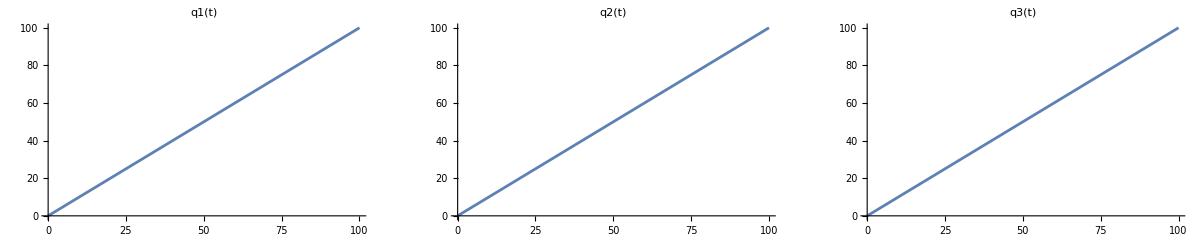

```mathematica
GraphicsRow[{P1,P2,P3}]
```

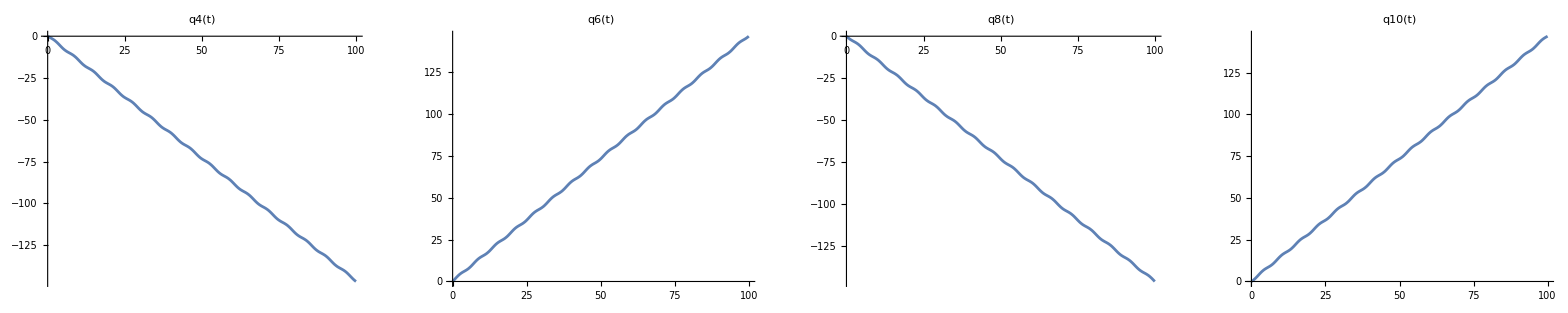

```mathematica
GraphicsRow[{P4,P6,P8,P10}]
```

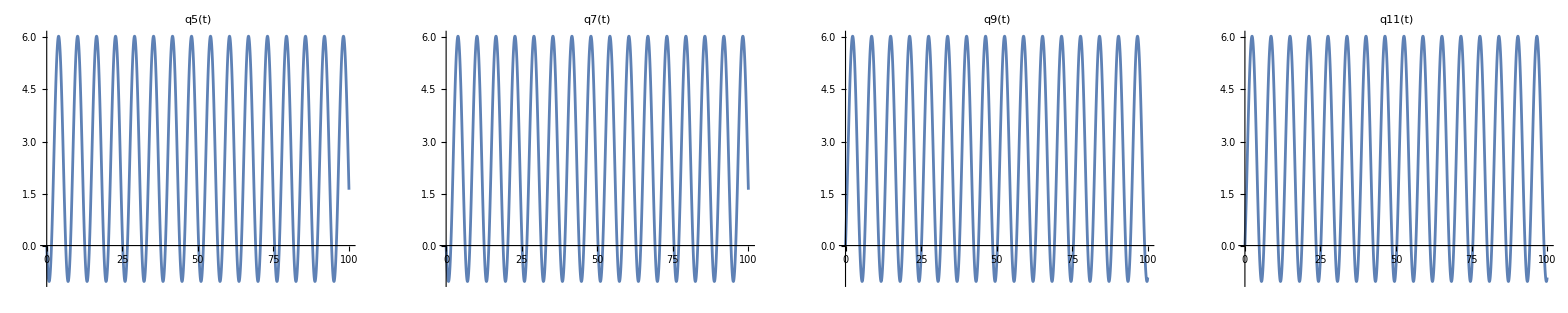

```mathematica
GraphicsRow[{P5,P7,P9,P11}]
```

### Animation

Create functions for the coordinates for demonstration purposes.

```mathematica
A=8;
```

```mathematica
Subscript[q, 1][t_]:=q1sol
Subscript[q, 2][t_]:= q2sol
Subscript[q, 3][t_]:=q3sol
Subscript[q, 4][t_]:= q4sol
Subscript[q, 5][t_]:= q5sol
Subscript[q, 6][t_]:=q6sol
Subscript[q, 7][t_]:=q7sol
Subscript[q, 8][t_]:= q8sol
Subscript[q, 9][t_]:= q9sol
Subscript[q, 10][t_]:= q10sol
Subscript[q, 11][t_]:= q11sol
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicAnim1={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

Make it a function of to so it can be looped over time

```mathematica
robotGraphicAnimT1[t_]=robotGraphicAnim1;
(*NtPp[t_]=NtP;*)
```

```mathematica
tf=100;
scale=3A;
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT1[t],ViewPoint->{1,1,1},ViewVertical->{1,1,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/10000},AnimationRunning->False]
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT1[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/1000},AnimationRunning->False]
```

Assume the base is made form perspex (Density =1.18 g/cm.b3=1180kg/m3)and wheels from a nylon (Density =1.15 g/cm.b3=1150 kg/m3)

### Manipulated FK animation

```mathematica
robotGraphicAnimT4[As_,b1_,b2_,b3_,tt_,tf_]:=Module[{qtsol,q1sol,q2sol,q3sol,q4sol,q5sol,q6sol,q7sol,q8sol,q9sol,q10sol,q11sol,A},
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
qtsol=qt[b1,b2,b3,tt];
q1sol=Subscript[q, 1][t]/.qtsol;
q2sol=Subscript[q, 2][t]/.qtsol;
q3sol=Subscript[q, 3][t]/.qtsol;
q4sol=Subscript[q, 4][t]/.qtsol;
q5sol=Subscript[q, 5][t]/.qtsol;
q6sol=Subscript[q, 6][t]/.qtsol;
q7sol=Subscript[q, 7][t]/.qtsol;
q8sol=Subscript[q, 8][t]/.qtsol;
q9sol=Subscript[q, 9][t]/.qtsol;
q10sol=Subscript[q, 10][t]/.qtsol;
q11sol=Subscript[q, 11][t]/.qtsol;
A=As;
Subscript[q, 1][t_]:=q1sol;
Subscript[q, 2][t_]:= q2sol;
Subscript[q, 3][t_]:=q3sol;
Subscript[q, 4][t_]:= q4sol;
Subscript[q, 5][t_]:= q5sol;
Subscript[q, 6][t_]:=q6sol;
Subscript[q, 7][t_]:=q7sol;
Subscript[q, 8][t_]:= q8sol;
Subscript[q, 9][t_]:= q9sol;
Subscript[q, 10][t_]:= q10sol;
Subscript[q, 11][t_]:= q11sol;
Graphics3D[{
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
}//.t->tt]
]
```

```mathematica
Manipulate[Show[robotGraphicAnimT4[A,B1,B2,B3,t,tf],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"},ImageSize->500],{{t,1},0,tf,tf/500,Appearance->"Open"},{{B1,1},-5,5,1,Appearance->"Open"},{{B2,3},-5,5,1,Appearance->"Open"},{{B3,2},-5,5,1,Appearance->"Open"}]
```

## Inverse Kinematics

#### Clearing variables

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
A=.;
B=.;
t=.;
Cc=.;
ω=.;
Ω=.;
r=.;
R=.;
A1=.;
A2=.;
A3=.;
B1=.;
B2=.;
B3=.;
```

Let’s Use Least square method

#### Least square method

```mathematica
relTransform[x_]:=x//.tRules
(*mytrig[x_]:= x/.{a__ Cos[b_]^2+a__ Sin[b_]^2-> a,a_. Cos[b_]^2+a_. Sin[b_]^2-> a}*)
```

```mathematica
MatrixA={{Coefficient[ω1a, Subscript[u, 1]],Coefficient[ω1a, Subscript[u, 2]],Coefficient[ω1a, Ω]},{Coefficient[ω2a, Subscript[u, 1]],Coefficient[ω2a, Subscript[u, 2]],Coefficient[ω2a, Ω]},{Coefficient[ω3a, Subscript[u, 1]],Coefficient[ω3a, Subscript[u, 2]],Coefficient[ω3a, Ω]},{Coefficient[ω4a, Subscript[u, 1]],Coefficient[ω4a, Subscript[u, 2]],Coefficient[ω4a, Ω]}}
```

{{(1. Cos[q_3[t]])/R,(1. Sin[q_3[t]])/R,-4.4/R},{(1. Cos[q_3[t]])/R,(1. Sin[q_3[t]])/R,4.4/R},{(1. Sin[q_3[t]])/R,-(1. Cos[q_3[t]])/R,-4.4/R},{(1. Sin[q_3[t]])/R,-(1. Cos[q_3[t]])/R,4.4/R}}

```mathematica
(*ωi={{ω1},{ω2},{ω3},{ω4}}*)
```

```mathematica
(*Q={{Subscript[u, 1]},{Subscript[u, 2]},{Ω}}*)
```

```mathematica
MatLeast=Inverse[Transpose[MatrixA].MatrixA].Transpose[MatrixA]//FullSimplify//Expand//gatherScalars//Chop(*//mytrig*)
```

{{0.5 R Cos[q_3[t]],0.5 R Cos[q_3[t]],0.5 R Sin[q_3[t]],0.5 R Sin[q_3[t]]},{0.5 R Sin[q_3[t]],0.5 R Sin[q_3[t]],-0.5 R Cos[q_3[t]],-0.5 R Cos[q_3[t]]},{-0.0568182 R,0.0568182 R,-0.0568182 R,0.0568182 R}}

```mathematica
(*Q=.;*)
```

```mathematica
MatLeastar=MatLeast(*/.{ω1-> Subscript[q, 4]'[t],ω2-> Subscript[q, 6]'[t],ω3-> Subscript[q, 8]'[t],ω4-> Subscript[q, 10]'[t]}*)//.{Subscript[q, n_][t]->Subscript[Q, n][t] ,Subscript[q, n_]'[t]->Subscript[Q, n]'[t] }//gatherScalars//Chop(*//mytrig*)
```

{{0.5 R Cos[Q_3[t]],0.5 R Cos[Q_3[t]],0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]]},{0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]],-0.5 R Cos[Q_3[t]],-0.5 R Cos[Q_3[t]]},{-0.0568182 R,0.0568182 R,-0.0568182 R,0.0568182 R}}

```mathematica
MatLeastar//MatrixForm
```

(0.5 R Cos[Q_3[t]] | 0.5 R Cos[Q_3[t]] | 0.5 R Sin[Q_3[t]] | 0.5 R Sin[Q_3[t]]
0.5 R Sin[Q_3[t]] | 0.5 R Sin[Q_3[t]] | -0.5 R Cos[Q_3[t]] | -0.5 R Cos[Q_3[t]]
-0.0568182 R | 0.0568182 R | -0.0568182 R | 0.0568182 R)

```mathematica
(*Subscript[Ui, Des]={{vx},{vy},{Ωz}}*)
```

```mathematica
A4= 0; A6= 0; A8= 0;A10= 0;
```

### q4 q6 q8 q10 pre -defined velocity

#### q4[t]

```mathematica
eqin1=Subscript[Q, 4]'[t]==A4 t+ B4
```

Q_4'[t]==B4

#### q6[t]

```mathematica
eqin2=Subscript[Q, 6]'[t]==A6 t+ B6
```

Q_6'[t]==B6

#### q8[t]

```mathematica
eqin3=Subscript[Q, 8]'[t]==A8 t+ B8
```

Q_8'[t]==B8

#### q10[t]

```mathematica
eqin4=Subscript[Q, 10]'[t]==A10 t+ B10
```

Q_10'[t]==B10

```mathematica
SetAttributes[{B4,B6,B8, B10},Constant]
```

### q1 q2 q3 calculating with the aid of q4 q6 q8 q10

#### Q1[t]

Comment these for the moment as testing

```mathematica
eqin5Right0=MatLeastar[[1]]//FullSimplify//Chop(*//mytrig*)
```

{0.5 R Cos[Q_3[t]],0.5 R Cos[Q_3[t]],0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]]}

```mathematica
eqin5Right1=eqin5Right0.{Subscript[Q, 4]'[t],Subscript[Q, 6]'[t],Subscript[Q, 8]'[t],Subscript[Q, 10]'[t]}//FullSimplify//Chop(*//mytrig*)
```

R (Cos[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Sin[Q_3[t]] (0.5 Q_8'[t]+0.5 Q_10'[t]))

```mathematica
eqin5=Subscript[Q, 1]'[t]==eqin5Right1//Chop(*//mytrig*)
```

Q_1'[t]==R (Cos[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Sin[Q_3[t]] (0.5 Q_8'[t]+0.5 Q_10'[t]))

#### Q2[t]

```mathematica
eqin6Right0=MatLeastar[[2]]//FullSimplify//Chop(*//mytrig*)
```

{0.5 R Sin[Q_3[t]],0.5 R Sin[Q_3[t]],-0.5 R Cos[Q_3[t]],-0.5 R Cos[Q_3[t]]}

```mathematica
eqin6Right1=eqin6Right0.{Subscript[Q, 4]'[t],Subscript[Q, 6]'[t],Subscript[Q, 8]'[t],Subscript[Q, 10]'[t]}//FullSimplify//Chop(*//mytrig*)
```

R (Sin[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Cos[Q_3[t]] (-0.5 Q_8'[t]-0.5 Q_10'[t]))

```mathematica
eqin6=Subscript[Q, 2]'[t]==eqin6Right1//Chop(*//mytrig*)
```

Q_2'[t]==R (Sin[Q_3[t]] (0.5 Q_4'[t]+0.5 Q_6'[t])+Cos[Q_3[t]] (-0.5 Q_8'[t]-0.5 Q_10'[t]))

#### Q3[t]

```mathematica
eqin7Right0=MatLeastar[[3]]//FullSimplify//Chop(*//mytrig*)
```

{-0.0568182 R,0.0568182 R,-0.0568182 R,0.0568182 R}

```mathematica
eqin7Right1=eqin7Right0.{Subscript[Q, 4]'[t],Subscript[Q, 6]'[t],Subscript[Q, 8]'[t],Subscript[Q, 10]'[t]}//FullSimplify//Chop(*//mytrig*)
```

R (-0.0568182 Q_4'[t]+0.0568182 Q_6'[t]-0.0568182 Q_8'[t]+0.0568182 Q_10'[t])

```mathematica
eqin7=Subscript[Q, 3]'[t]==eqin7Right1//Chop(*//mytrig*)
```

Q_3'[t]==R (-0.0568182 Q_4'[t]+0.0568182 Q_6'[t]-0.0568182 Q_8'[t]+0.0568182 Q_10'[t])

### q5 q7 q9 q11

#### Q5

```mathematica
eqQ5=eq5/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 5]'[t]-> Subscript[Q, 5]'[t]}
```

Q_5'[t]==(Sin[Q_3[t]] Q_1'[t]-Cos[Q_3[t]] Q_2'[t])/r

#### Q7

```mathematica
eqQ7=eq6/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 7]'[t]-> Subscript[Q, 7]'[t]}
```

Q_7'[t]==(Sin[Q_3[t]] Q_1'[t]-Cos[Q_3[t]] Q_2'[t])/r

#### Q9

```mathematica
eqQ9=eq7/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 9]'[t]-> Subscript[Q, 9]'[t]}
```

Q_9'[t]==(Cos[Q_3[t]] Q_1'[t]+Sin[Q_3[t]] Q_2'[t])/r

#### Q11

```mathematica
eqQ11=eq8/.{Subscript[q, 1]'[t]-> Subscript[Q, 1]'[t],Subscript[q, 2]'[t]-> Subscript[Q, 2]'[t],Subscript[q, 3][t]-> Subscript[Q, 3][t],Subscript[q, 11]'[t]-> Subscript[Q, 11]'[t]}
```

Q_11'[t]==(Cos[Q_3[t]] Q_1'[t]+Sin[Q_3[t]] Q_2'[t])/r

### Test IC

#### Test

```mathematica
eqin1
```

Q_4'[t]==B4

```mathematica
eqin2
```

Q_6'[t]==B6

```mathematica
eqin3
```

Q_8'[t]==B8

```mathematica
eqin4
```

Q_10'[t]==B10

```mathematica
Denominator[eqin5[[2]]]
```

1

```mathematica
Denominator[eqin6[[2]]]
```

1

```mathematica
Denominator[eqin7[[2]]]
```

1

```mathematica
Denominator[eqin5[[2]]]-Denominator[eqin6[[2]]]
```

0

```mathematica
Denominator[eqin5[[2]]]/.{Subscript[Q, 4][t]-> 0,Subscript[Q, 6][t]-> 0,Subscript[Q, 8][t]-> 0,Subscript[Q, 10][t]->0}
```

1

```mathematica
Denominator[eqin6[[2]]]/.{Subscript[Q, 4][t]-> 0,Subscript[Q, 6][t]-> 0,Subscript[Q, 8][t]-> 0,Subscript[Q, 10][t]->0}
```

1

```mathematica
Denominator[eqin7[[2]]]/.{Subscript[Q, 4][t]-> 100,Subscript[Q, 6][t]->100,Subscript[Q, 8][t]->100,Subscript[Q, 10][t]->100}
```

1

#### Test of initial Condition space #1 (Check this next and test 1 code later)

```mathematica
(*eqin5t=eqin5//.{Subscript[Q, 1]'[t]->Subscript[Qt, 1]'[t],Subscript[Q, 3][t]->Subscript[Qt, 3][t],Subscript[Q, 4][t]->Subscript[Qt, 4][t],Subscript[Q, 6][t]->Subscript[Qt, 6][t],Subscript[Q, 8][t]->Subscript[Qt, 8][t],Subscript[Q, 10][t]->Subscript[Qt, 10][t]}*)
```

```mathematica
(*eqin6t=eqin6//.{Subscript[Q, 1]'[t]->Subscript[Qt, 1]'[t],Subscript[Q, 3][t]->Subscript[Qt, 3][t],Subscript[Q, 4][t]->Subscript[Qt, 4][t],Subscript[Q, 6][t]->Subscript[Qt, 6][t],Subscript[Q, 8][t]->Subscript[Qt, 8][t],Subscript[Q, 10][t]->Subscript[Qt, 10][t]}*)
```

```mathematica
(*eqin7t=eqin7//.{Subscript[Q, 1]'[t]->Subscript[Qt, 1]'[t],Subscript[Q, 3][t]->Subscript[Qt, 3][t],Subscript[Q, 4][t]->Subscript[Qt, 4][t],Subscript[Q, 6][t]->Subscript[Qt, 6][t],Subscript[Q, 8][t]->Subscript[Qt, 8][t],Subscript[Q, 10][t]->Subscript[Qt, 10][t]}*)
```

```mathematica
(*{eqin5t,eqin6t,eqin7t}//.{Subscript[Qt, 3][t]->Q3,Subscript[Qt, 4][t]->Q4,Subscript[Qt, 6][t]->Q6,Subscript[Qt, 8][t]->Q8,Subscript[Qt, 10][t]->Q10}//.{r-> 5,R-> 50,B4->b4,B6->b6,B8->b8,B10->b10}*)
```

```mathematica
(*test1[b4_,b6_,b8_,b10_,Q3_,Q4_,Q6_,Q8_,Q10_,t_]:={eqin5t,eqin6t,eqin7t}//.{Subscript[Qt, 3][t]->Q3,Subscript[Qt, 4][t]->Q4,Subscript[Qt, 6][t]->Q6,Subscript[Qt, 8][t]->Q8,Subscript[Qt, 10][t]->Q10}*)
```

```mathematica
(*test1[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,t]*)
```

```mathematica
(*Manipulate[test1[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,t],{b4,-10,10,Appearance-> "Open"},{b6,-10,10,Appearance-> "Open"},{b8,-10,10,Appearance-> "Open"},{b10,-10,10,Appearance-> "Open"},{{Q3,0},-10,10,0.1,Appearance-> "Open"},{{Q4,0},-10,10,0.1,Appearance-> "Open"},{{Q6,0},-10,10,0.1,Appearance-> "Open"},{{Q8,0},-10,10,0.1,Appearance-> "Open"},{{Q10,0},-10,10,0.1,Appearance-> "Open"},{t,0,10,0.1,Appearance-> "Open"}]*)
```

```mathematica
(*test1[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,t]*)
```

```mathematica
(*Manipulate[test1[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,t],{b4,-10,10},{b6,-10,10},{b8,-10,10},{b10,-10,10},{Q3,-10,10},{Q4,-10,10},{Q6,-10,10},{Q8,-10,10},{Q10,-10,10},{t,0,10}]*)
```

#### Test of initial Condition space #2

```mathematica
(*test2[b4_,b6_,b8_,b10_,Q3_,Q4_,Q6_,Q8_,Q10_,t_]:={eqin5,eqin6,eqin7}//.{Subscript[Q, 3][t]->Q3,Subscript[Q, 4][t]->Q4,Subscript[Q, 6][t]->Q6,Subscript[Q, 8][t]->Q8,Subscript[Q, 10][t]->Q10}//.{r-> 5,R-> 50,B4->b4,B6->b6,B8->b8,B10->b10}*)
```

```mathematica
(*test2[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,t]*)
```

```mathematica
(*Manipulate[test2[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,t],{b4,-10,10,Appearance-> "Open"},{b6,-10,10,Appearance-> "Open"},{b8,-10,10,Appearance-> "Open"},{b10,-10,10,Appearance-> "Open"},{{Q3,0},-10,10,0.1,Appearance-> "Open"},{{Q4,0},-10,10,0.1,Appearance-> "Open"},{{Q6,0},-10,10,0.1,Appearance-> "Open"},{{Q8,0},-10,10,0.1,Appearance-> "Open"},{{Q10,0},-10,10,0.1,Appearance-> "Open"},{t,0,10,0.1,Appearance-> "Open"}]*)
```

```mathematica
(*Manipulate[test2[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,t],{b4,-10,10},{b6,-10,10},{b8,-10,10},{b10,-10,10,Appearance-> "Open"},{{Q3,0},-10,10},{{Q4,0},-10,10},{{Q6,0},-10,10},{{Q8,0},-10,10},{{Q10,0},-10,10},{t,0,10}]*)
```

#### Test 1

```mathematica
(*eqin5t=eqin5/.{Subscript[Q, 4]'[t]-> B4,Subscript[Q, 6]'[t]->B6,Subscript[Q, 8]'[t]->B8,Subscript[Q, 10]'[t]->B10}*)
```

```mathematica
(*eqin6t=eqin6/.{Subscript[Q, 4]'[t]-> B4,Subscript[Q, 6]'[t]->B6,Subscript[Q, 8]'[t]->B8,Subscript[Q, 10]'[t]->B10}*)
```

```mathematica
(*eqin7t=eqin7/.{Subscript[Q, 4]'[t]-> B4,Subscript[Q, 6]'[t]->B6,Subscript[Q, 8]'[t]->B8,Subscript[Q, 10]'[t]->B10}*)
```

```mathematica
(*test[b4_,b6_,b8_,b10_,Q3_,Q4_,Q6_,Q8_,Q10_,Tfin_]:={eqin5t,eqin6t,eqin7t}//.{Subscript[Q, 3][t]->Q3,Subscript[Q, 4][t]->Q4,Subscript[Q, 6][t]->Q6,Subscript[Q, 8][t]->Q8,Subscript[Q, 10][t]->Q10}//.{r-> 5,R-> 50,B4->b4,B6->b6,B8->b8,B10->b10}*)
```

```mathematica
(*Manipulate[test[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,TF],{b4,-10,10},{b6,-10,10},{b8,-10,10},{b10,-10,10},{Q3,-10,10},{Q4,-10,10},{Q6,-10,10},{Q8,-10,10},{Q10,-10,10},{TF,0,1}]*)
```

### Test 2

```mathematica
eqin5t=eqin5/.{Subscript[Q, 1]'[t]-> Subscript[Qt, 1]'[t],Subscript[Q, 2]'[t]-> Subscript[Qt, 2]'[t],Subscript[Q, 3]'[t]-> Subscript[Qt, 3]'[t],Subscript[Q, 4]'[t]-> B4,Subscript[Q, 6]'[t]->B6,Subscript[Q, 8]'[t]->B8,Subscript[Q, 10]'[t]->B10,Subscript[Q, 3][t]->Subscript[Qt, 3][t],Subscript[Q, 4][t]->Subscript[Qt, 4][t],Subscript[Q, 6][t]->Subscript[Qt, 6][t],Subscript[Q, 8][t]->Subscript[Qt, 8][t],Subscript[Q, 10][t]->Subscript[Qt, 10][t]}
```

Qt_1'[t]==R ((0.5 B4+0.5 B6) Cos[Qt_3[t]]+(0.5 B10+0.5 B8) Sin[Qt_3[t]])

```mathematica
eqin6t=eqin6/.{Subscript[Q, 1]'[t]-> Subscript[Qt, 1]'[t],Subscript[Q, 2]'[t]-> Subscript[Qt, 2]'[t],Subscript[Q, 3]'[t]-> Subscript[Qt, 3]'[t],Subscript[Q, 4]'[t]-> B4,Subscript[Q, 6]'[t]->B6,Subscript[Q, 8]'[t]->B8,Subscript[Q, 10]'[t]->B10,Subscript[Q, 3][t]->Subscript[Qt, 3][t],Subscript[Q, 4][t]->Subscript[Qt, 4][t],Subscript[Q, 6][t]->Subscript[Qt, 6][t],Subscript[Q, 8][t]->Subscript[Qt, 8][t],Subscript[Q, 10][t]->Subscript[Qt, 10][t]}
```

Qt_2'[t]==R ((-0.5 B10-0.5 B8) Cos[Qt_3[t]]+(0.5 B4+0.5 B6) Sin[Qt_3[t]])

```mathematica
eqin7t=eqin7/.{Subscript[Q, 1]'[t]-> Subscript[Qt, 1]'[t],Subscript[Q, 2]'[t]-> Subscript[Qt, 2]'[t],Subscript[Q, 3]'[t]-> Subscript[Qt, 3]'[t],Subscript[Q, 4]'[t]-> B4,Subscript[Q, 6]'[t]->B6,Subscript[Q, 8]'[t]->B8,Subscript[Q, 10]'[t]->B10,Subscript[Q, 3][t]->Subscript[Qt, 3][t],Subscript[Q, 4][t]->Subscript[Qt, 4][t],Subscript[Q, 6][t]->Subscript[Qt, 6][t],Subscript[Q, 8][t]->Subscript[Qt, 8][t],Subscript[Q, 10][t]->Subscript[Qt, 10][t]}
```

Qt_3'[t]==(0.0568182 B10-0.0568182 B4+0.0568182 B6-0.0568182 B8) R

```mathematica
test[b4_,b6_,b8_,b10_,Q3_,Q4_,Q6_,Q8_,Q10_,Tfin_]:={eqin5t,eqin6t,eqin7t}//.{Subscript[Qt, 3][t]->Q3,Subscript[Qt, 4][t]->Q4,Subscript[Qt, 6][t]->Q6,Subscript[Qt, 8][t]->Q8,Subscript[Qt, 10][t]->Q10}//.{r-> 5,R-> 50,B4->b4,B6->b6,B8->b8,B10->b10}
```

```mathematica
Manipulate[test[b4,b6,b8,b10,Q3,Q4,Q6,Q8,Q10,TF],{b4,-10,10},{b6,-10,10},{b8,-10,10},{b10,-10,10},{Q3,-10,10},{Q4,-10,10},{Q6,-10,10},{Q8,-10,10},{Q10,-10,10},{TF,0,1}]
```

Denominator of Q_1'[t],Q_2'[t],Q_3'[t] are f[Q_4[t],Q_6[t],Q_8[t],Q_10[t]]
B4, B6, B8, B10 (which are Q_4'[t],Q_6'[t],Q_8'[t],Q_10'[t]) 
If B4, B6, B8, B10 are zero and Q_4[t],Q_6[t],Q_8[t],Q_10[t] are zero { Qt_1'[t]==ComplexInfinity,Qt_2'[t]==ComplexInfinity,Qt_3'[t]==Indeterminate }
For NOT to be ComplexInfinity and  indeterminate either one of Q_4[t],Q_6[t],Q_8[t],Q_10[t] not equal to zero. If B4, B6, B8, B10 = 0 and one of the Q_4[t],Q_6[t],Q_8[t],Q_10[t] or all of them NOT equal to zero {Qt_1'[t]==0.,Qt_2'[t]==0.,Qt_3'[t]==0.}.

### Equation

-Graphics3D-

```mathematica
(*eqQ5,eqQ7,eqQ9,eqQ11,*)
(*,Subscript[Q, 5][0]==0.1,Subscript[Q, 7][0]==0.1,Subscript[Q, 9][0]==0.1,Subscript[Q, 11][0]==0.1*)
```

ICns Q_4[0]==5,Q_6[0]==5.1,Q_8[0]==-5.1,Q_10[0]==-5

```mathematica
(*qtinv[b4_,b6_,b8_,b10_,Tfin_]:=NDSolve[{eqin1,eqin2,eqin3,eqin4,eqin5,eqin6,eqin7,Subscript[Q, 1][0]==0,Subscript[Q, 2][0]==0,Subscript[Q, 3][0]==0,Subscript[Q, 4][0]==1.5,Subscript[Q, 6][0]==1.51,Subscript[Q, 8][0]==-1.51,Subscript[Q, 10][0]==-1.5}/.{r-> 0.4,R->3,B4->b4,B6->b6,B8->b8,B10->b10,A4-> 0, A6-> 0, A8-> 0,A10-> 0},{Subscript[Q, 1][t],Subscript[Q, 2][t],Subscript[Q, 3][t],Subscript[Q, 4][t],Subscript[Q, 6][t],Subscript[Q, 8][t],Subscript[Q, 10][t]},{t,0, Tfin}]//First*)
```

```mathematica
qtinv[b4_,b6_,b8_,b10_,Tfin_]:=NDSolve[{eqin1,eqin2,eqin3,eqin4,eqin5,eqin6,eqin7,eqQ5,eqQ7,eqQ9,eqQ11, Subscript[Q, 1][0]==0,Subscript[Q, 2][0]==0,Subscript[Q, 3][0]==0,Subscript[Q, 4][0]==0,Subscript[Q, 6][0]==0,Subscript[Q, 8][0]==0,Subscript[Q, 10][0]==0,Subscript[Q, 5][0]==0,Subscript[Q, 7][0]==0,Subscript[Q, 9][0]==0,Subscript[Q, 11][0]==0}/.{r-> 0.4,R->3,B4->b4,B6->b6,B8->b8,B10->b10,A4-> 0, A6-> 0, A8-> 0,A10-> 0},{Subscript[Q, 1][t],Subscript[Q, 2][t],Subscript[Q, 3][t],Subscript[Q, 4][t],Subscript[Q, 6][t],Subscript[Q, 8][t],Subscript[Q, 10][t],Subscript[Q, 5][t],Subscript[Q, 7][t],Subscript[Q, 9][t],Subscript[Q, 11][t]},{t,0, Tfin}]//First
```

```mathematica
qtinvsol=.;
```

```mathematica
(*qtinvsol=qtinv[0.5,0.3,-0.1,-0.2,100]*)
```

```mathematica
qtinvsol=qtinv[0,0,-1,-1,100]
```

{Q_1[t]→InterpolatingFunction[…][t],Q_2[t]→InterpolatingFunction[…][t],Q_3[t]→InterpolatingFunction[…][t],Q_4[t]→InterpolatingFunction[…][t],Q_6[t]→InterpolatingFunction[…][t],Q_8[t]→InterpolatingFunction[…][t],Q_10[t]→InterpolatingFunction[…][t],Q_5[t]→InterpolatingFunction[…][t],Q_7[t]→InterpolatingFunction[…][t],Q_9[t]→InterpolatingFunction[…][t],Q_11[t]→InterpolatingFunction[…][t]}

### Results

#### Q1[t]

```mathematica
Subscript[Qn, 1][t]=Subscript[Q, 1][t]/.qtinvsol
```

InterpolatingFunction[…][t]

```mathematica
Qn1[t]=Subscript[Qn, 1][t]
```

InterpolatingFunction[…][t]

```mathematica
Q1plot=Plot[Qn1[t],{t,0,100}]
```

-Graphics-

#### Q2[t]

```mathematica
Subscript[Qn, 2][t]=Subscript[Q, 2][t]/.qtinvsol
```

InterpolatingFunction[…][t]

```mathematica
Qn2[t]=Subscript[Qn, 2][t];
Q2plot=Plot[Qn2[t],{t,0,100}]
```

-Graphics-

```mathematica
Manipulate[ParametricPlot[{Subscript[Q, 1][t]/.qtinvsol,Subscript[Q, 2][t]/.qtinvsol},{t,0,TF}],{TF,0.0001,100,50/10000}]
```

```mathematica
Subscript[Qn, 3][t]=Subscript[Q, 3][t]/.qtinvsol
```

InterpolatingFunction[…][t]

```mathematica
Qn3[t]=Subscript[Qn, 3][t];
Q3plot=Plot[Qn3[t],{t,0,100}]
```

-Graphics-

```mathematica
Show[Q1plot,Q2plot, PlotRange-> All]
```

-Graphics-

#### Q1'[t]

```mathematica
Q1d[t]=D[Subscript[Qn, 1][t],t]
```

InterpolatingFunction[…][t]

```mathematica
Q1dplot=Plot[Q1d[t],{t,0,100}, PlotRange-> All]
```

-Graphics-

#### Q2'[t]

```mathematica
Q2d[t]=D[Subscript[Qn, 2][t],t]
```

InterpolatingFunction[…][t]

```mathematica
Q2dplot=Plot[Q2d[t],{t,0,100}, PlotRange-> All]
```

-Graphics-

```mathematica
Show[Q1dplot,Q2dplot]
```

-Graphics-

#### Q3’[t]

```mathematica
Q3d[t]=D[Subscript[Qn, 3][t],t]
```

InterpolatingFunction[…][t]

```mathematica
Q3dplot=Plot[Q3d[t],{t,0,100}, PlotRange-> All]
```

-Graphics-

### Animation

Create functions for the coordinates for demonstration purposes.

```mathematica
A=8;
```

```mathematica
(*Subscript[q, n_][t_]:=Subscript[Q, n][t]*)
```

```mathematica
q1insol=Subscript[q, 1][t]/.{Subscript[q, 1][t]-> Subscript[Q, 1][t]}/.qtinvsol;
q2insol=Subscript[q, 2][t]/.{Subscript[q, 2][t]-> Subscript[Q, 2][t]}/.qtinvsol;
q3insol=Subscript[q, 3][t]/.{Subscript[q, 3][t]-> Subscript[Q, 3][t]}/.qtinvsol;
q4insol=Subscript[q, 4][t]/.{Subscript[q, 4][t]-> Subscript[Q, 4][t]}/.qtinvsol;
q5insol=Subscript[q, 5][t]/.{Subscript[q, 5][t]-> Subscript[Q, 5][t]}/.qtinvsol;
q6insol=Subscript[q, 6][t]/.{Subscript[q, 6][t]-> Subscript[Q, 6][t]}/.qtinvsol;
q7insol=Subscript[q, 7][t]/.{Subscript[q, 7][t]-> Subscript[Q, 7][t]}/.qtinvsol;
q8insol=Subscript[q, 8][t]/.{Subscript[q, 8][t]-> Subscript[Q, 8][t]}/.qtinvsol;
q9insol=Subscript[q, 9][t]/.{Subscript[q, 9][t]-> Subscript[Q, 9][t]}/.qtinvsol;
q10insol=Subscript[q, 10][t]/.{Subscript[q, 10][t]-> Subscript[Q, 10][t]}/.qtinvsol;
q11insol=Subscript[q, 11][t]/.{Subscript[q, 11][t]-> Subscript[Q, 11][t]}/.qtinvsol;
```

```mathematica
Subscript[q, 1][t_]:=q1insol
Subscript[q, 2][t_]:= q2insol
Subscript[q, 3][t_]:=q3insol
Subscript[q, 4][t_]:= q4insol
Subscript[q, 5][t_]:= q5insol
Subscript[q, 6][t_]:=q6insol
Subscript[q, 7][t_]:=q7insol
Subscript[q, 8][t_]:= q8insol
Subscript[q, 9][t_]:= q9insol
Subscript[q, 10][t_]:= q10insol
Subscript[q, 11][t_]:= q11insol
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
(*Subscript[q, n_][t_]:=Subscript[Q, n][t]*)
```

```mathematica
robotGraphicAnim2={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

Make it a function of to so it can be looped over time

```mathematica
robotGraphicAnimT2[t_]=robotGraphicAnim2;
(*NtPp[t_]=NtP;*)
```

```mathematica
tf=100;
scale=3A;
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT2[t],ViewPoint->{1,1,1},ViewVertical->{1,1,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/500},AnimationRunning->False]
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT2[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/1000},AnimationRunning->False]
```

Assume the base is made form perspex (Density =1.18 g/cm.b3=1180kg/m3)and wheels from a nylon (Density =1.15 g/cm.b3=1150 kg/m3)

### Manipulated IK animation

```mathematica
robotGraphicAnimT3[As_,b1_,b2_,b3_,b4_,tt_,tf_]:=Module[{qtinvsol,q1insol,q2insol,q3insol,q4insol,q5insol,q6insol,q7insol,q8insol,q9insol,q10insol,q11insol,A},
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
qtinvsol=qtinv[b1,b2,b3,b4,tt];
q1insol=Subscript[Q, 1][t]/.qtinvsol;
q2insol=Subscript[Q, 2][t]/.qtinvsol;
q3insol=Subscript[Q, 3][t]/.qtinvsol;
q4insol=Subscript[Q, 4][t]/.qtinvsol;
q5insol=Subscript[Q, 5][t]/.qtinvsol;
q6insol=Subscript[Q, 6][t]/.qtinvsol;
q7insol=Subscript[Q, 7][t]/.qtinvsol;
q8insol=Subscript[Q, 8][t]/.qtinvsol;
q9insol=Subscript[Q, 9][t]/.qtinvsol;
q10insol=Subscript[Q, 10][t]/.qtinvsol;
q11insol=Subscript[Q, 11][t]/.qtinvsol;
A=As;
Subscript[q, 1][t_]:=q1insol;
Subscript[q, 2][t_]:= q2insol;
Subscript[q, 3][t_]:=q3insol;
Subscript[q, 4][t_]:= q4insol;
Subscript[q, 5][t_]:= q5insol;
Subscript[q, 6][t_]:=q6insol;
Subscript[q, 7][t_]:=q7insol;
Subscript[q, 8][t_]:= q8insol;
Subscript[q, 9][t_]:= q9insol;
Subscript[q, 10][t_]:= q10insol;
Subscript[q, 11][t_]:= q11insol;
Graphics3D[{
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
}//.t->tt]
]
```

```mathematica
Manipulate[Show[robotGraphicAnimT3[A,B1,B2,B3,B4,t,tf],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"},ImageSize->500],{{t,1},0,tf,tf/500,Appearance->"Open"},{{B1,1},-5,5,1,Appearance->"Open"},{{B2,3},-5,5,1,Appearance->"Open"},{{B3,2},-5,5,1,Appearance->"Open"},{{B4,2},-5,5,1,Appearance->"Open"}]
```

## Dynamic Equations of Motion

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
```

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

-Graphics3D-

#### Substitution

```mathematica
Subscript[q, 5]'[t_]:=eqQ5[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]};
Subscript[q, 7]'[t_]:=eqQ7[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]};
Subscript[q, 9]'[t_]:=eqQ9[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]};
Subscript[q, 11]'[t_]:=eqQ11[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]};
```

```mathematica
Subscript[q, 1]'[t_]:= Subscript[u, 1][t]
Subscript[q, 2]'[t_]:= Subscript[u, 2][t]
Subscript[q, 3]'[t_]:=Ω[t]
Subscript[q, 4]'[t_]:= Subscript[ω, 1][t]
Subscript[q, 6]'[t_]:= Subscript[ω, 2][t]
Subscript[q, 8]'[t_]:= Subscript[ω, 3][t]
Subscript[q, 10]'[t_]:= Subscript[ω, 4][t]
```

### Bodies

#### Base platform[1]

```mathematica
Subscript[F, app][1]=- Subscript[M, 1] g n[3]
```

-g M_1 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][1]=- Subscript[T, mot][1] a[2]  -Subscript[T, mot][2] a[2]  -Subscript[T, mot][3] a[1]  -Subscript[T, mot][4] a[1]
```

-(â)_2 T_mot[1]-(â)_2 T_mot[2]-(â)_1 T_mot[3]-(â)_1 T_mot[4]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[1] = OrA
BrCM[1] = 0
```

3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[1] = OrB[1] + BrCM[1]
```

3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[1] = omega[N,A]=Subscript[q, 3]'[t] a[3]
```

(â)_3 Ω[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[1] = DvDt[N,OrB[1]]//Chop
```

(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[1] = DvDt[N,OrCM[1]]//Chop
```

(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[1] = DvDt[N,OvB[1]]
```

(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[1] = DvDt[N,OvCM[1]]
```

(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration

```mathematica
NαB[1]=DvDt[N,NωB[1]]
```

(â)_3 Ω'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][1] = Subscript[Ai, 11] aa[1,1] + Subscript[Ai, 22] aa[2,2] +Subscript[Ai, 33] aa[3,3]
```

Ai_11 ((â)_1(â)_1)+Ai_22 ((â)_2(â)_2)+Ai_33 ((â)_3(â)_3)

Next we develop a transformation from this body to the previous body or frame, not all the way back to the Newtonian frame in general.

```mathematica
relT[1]=rot3[Subscript[q, 3][t]].{n[1],n[2],n[3]};
```

```mathematica
relTran[1]={a[1]->relT[1][[1]],a[2]->relT[1][[2]],a[3]->relT[1][[3]]}
```

{(â)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(â)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(â)_3→(n̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][1]= Subscript[M, 1] OxCM[1]//distributeScalars
```

M_1 (n̂)_1 u_1'[t]+M_1 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][1]= (Subscript[M, 1] BrCM[1] × OxB[1] + Subscript[I, b][1]. NαB[1]+ (NωB[1] ×Subscript[I, b][1]).NωB[1])
```

Ai_33 (â)_3 Ω'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[1]=Subscript[M, 1] g n[3].OrCM[1]
```

3.4 g M_1

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[1]=(1/2)Subscript[M, 1] OvB[1].OvB[1]+Subscript[M, 1] OvB[1].(NωB[1] ×BrCM[1])+(1/2)( NωB[1] .Subscript[I, b][1]).NωB[1]//Expand
```

1/2 Ai_33 Ω[t]^2+1/2 M_1 u_1[t]^2+1/2 M_1 u_2[t]^2

#### Wheel 1[2]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][2]=- Subscript[M, 2] g n[3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][2]= Subscript[T, mot][1] b[2]
```

(b̂)_2 T_mot[1]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[2] = OrA + ArB
BrCM[2] = 0
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[2] = OrB[2] + BrCM[2]
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[2] = omega[N,B]=Subscript[q, 3]'[t] a[3] + Subscript[q, 4]'[t] b[2]
```

(â)_3 Ω[t]+(b̂)_2 ω_1[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[2] = DvDt[N,OrB[2]]//Chop
```

-4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[2] = DvDt[N,OrCM[2]]//Chop
```

-4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[2] = DvDt[N,OvB[2]]//Expand
```

-4.4 (â)_2 Ω[t]^2-4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[2] = DvDt[N,OvCM[2]]//Expand
```

-4.4 (â)_2 Ω[t]^2-4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[2]=DvDt[N,NωB[2]]
```

(â)_3×(b̂)_2 Ω[t] ω_1[t]+(â)_3 Ω'[t]+(b̂)_2 ω_1'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][2] = Subscript[Bi, 11] bb[1,1] + Subscript[Bi, 22] bb[2,2] + Subscript[Bi, 33] bb[3,3]
```

Bi_11 ((b̂)_1(b̂)_1)+Bi_22 ((b̂)_2(b̂)_2)+Bi_33 ((b̂)_3(b̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[2]=rot2[Subscript[q, 4][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[2]={b[1]->relT[2][[1]],b[2]->relT[2][[2]],b[3]->relT[2][[3]]}
```

{(b̂)_1→Cos[q_4[t]] (â)_1-Sin[q_4[t]] (â)_3,(b̂)_2→(â)_2,(b̂)_3→Sin[q_4[t]] (â)_1+Cos[q_4[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][2]= Subscript[M, 2] OxCM[2]//distributeScalars
```

-4.4 M_2 (â)_2 Ω[t]^2-4.4 M_2 (â)_1 Ω'[t]+M_2 (n̂)_1 u_1'[t]+M_2 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][2]= (Subscript[M, 2] BrCM[2] × OxB[2] + Subscript[I, b][2]. NαB[2] + (NωB[2] ×Subscript[I, b][2]).NωB[2])//Expand //distributeScalars//distributeScalars
```

(â)_3×(b̂)_1 (â)_3.(b̂)_1 Bi_11 Ω[t]^2+(â)_3×(b̂)_2 (â)_3.(b̂)_2 Bi_22 Ω[t]^2+(â)_3×(b̂)_3 (â)_3.(b̂)_3 Bi_33 Ω[t]^2+(â)_3×(b̂)_2 Bi_22 Ω[t] ω_1[t]-(â)_3.(b̂)_3 Bi_11 (b̂)_1 Ω[t] ω_1[t]+(â)_3.(b̂)_3 Bi_33 (b̂)_1 Ω[t] ω_1[t]-(â)_3.(b̂)_1 Bi_11 (b̂)_3 Ω[t] ω_1[t]+(â)_3.(b̂)_1 Bi_33 (b̂)_3 Ω[t] ω_1[t]+(â)_3.(b̂)_1 Bi_11 (b̂)_1 Ω'[t]+(â)_3.(b̂)_2 Bi_22 (b̂)_2 Ω'[t]+(â)_3.(b̂)_3 Bi_33 (b̂)_3 Ω'[t]+Bi_22 (b̂)_2 ω_1'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[2]=Subscript[M, 2] g n[3].OrCM[2]//Expand
```

3.4 g M_2+4.4 g (â)_2.(n̂)_3 M_2-0.4 g (â)_3.(n̂)_3 M_2

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[2]=((1/2)Subscript[M, 2] OvB[2].OvB[2]+Subscript[M, 2] OvB[2].(NωB[2] ×BrCM[2])+(1/2)( NωB[2] .Subscript[I, b][2]).NωB[2]//Expand)//Expand
```

1/2 ((â)_3.(b̂)_1)^2 Bi_11 Ω[t]^2+1/2 ((â)_3.(b̂)_2)^2 Bi_22 Ω[t]^2+1/2 ((â)_3.(b̂)_3)^2 Bi_33 Ω[t]^2+9.68 M_2 Ω[t]^2-4.4 (â)_1.(n̂)_1 M_2 Ω[t] u_1[t]+1/2 M_2 u_1[t]^2-4.4 (â)_1.(n̂)_2 M_2 Ω[t] u_2[t]+1/2 M_2 u_2[t]^2+(â)_3.(b̂)_2 Bi_22 Ω[t] ω_1[t]+1/2 Bi_22 ω_1[t]^2

#### Torus 1[3]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][3]=- Subscript[M, 3] g n[3]
```

-g M_3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][3]= (**Subscript[T, mot][1] b[2] *) 0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[3] = OrA + ArB
BrCM[3] = 0
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[3] = OrB[3] + BrCM[3]
```

4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[3] = omega[N,M] =NωB[2]
```

(â)_3 Ω[t]+(b̂)_2 ω_1[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[3] = DvDt[N,OrB[3]]//Chop
```

-4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[3] = DvDt[N,OrCM[3]]//Chop
```

-4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[3] = DvDt[N,OvB[3]]//Expand
```

-4.4 (â)_2 Ω[t]^2-4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[3] = DvDt[N,OvCM[3]]//Expand
```

-4.4 (â)_2 Ω[t]^2-4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[3]=DvDt[N,NωB[3]]
```

(â)_3×(b̂)_2 Ω[t] ω_1[t]+(â)_3 Ω'[t]+(b̂)_2 ω_1'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][3] = Subscript[Mi, 11] mm[1,1] + Subscript[Mi, 22] mm[2,2] + Subscript[Mi, 33] mm[3,3]
```

Mi_11 ((m̂)_1(m̂)_1)+Mi_22 ((m̂)_2(m̂)_2)+Mi_33 ((m̂)_3(m̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[3]=rot0[].{b[1],b[2],b[3]};
```

```mathematica
relTran[3]={m[1]->relT[3][[1]],m[2]->relT[3][[2]],m[3]->relT[3][[3]]}
```

{(m̂)_1→(b̂)_1,(m̂)_2→(b̂)_2,(m̂)_3→(b̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][3]= Subscript[M, 3] OxCM[3]//distributeScalars
```

-4.4 M_3 (â)_2 Ω[t]^2-4.4 M_3 (â)_1 Ω'[t]+M_3 (n̂)_1 u_1'[t]+M_3 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][3]= (Subscript[M, 3] BrCM[3] × OxB[3] + Subscript[I, b][3]. NαB[3] + (NωB[3] ×Subscript[I, b][3]).NωB[3])//Expand //distributeScalars//distributeScalars
```

(â)_3×(m̂)_1 (â)_3.(m̂)_1 Mi_11 Ω[t]^2+(â)_3×(m̂)_2 (â)_3.(m̂)_2 Mi_22 Ω[t]^2+(â)_3×(m̂)_3 (â)_3.(m̂)_3 Mi_33 Ω[t]^2+(b̂)_2×(m̂)_1 (â)_3.(m̂)_1 Mi_11 Ω[t] ω_1[t]+(â)_3×(m̂)_1 (b̂)_2.(m̂)_1 Mi_11 Ω[t] ω_1[t]+(b̂)_2×(m̂)_2 (â)_3.(m̂)_2 Mi_22 Ω[t] ω_1[t]+(â)_3×(m̂)_2 (b̂)_2.(m̂)_2 Mi_22 Ω[t] ω_1[t]+(b̂)_2×(m̂)_3 (â)_3.(m̂)_3 Mi_33 Ω[t] ω_1[t]+(â)_3×(m̂)_3 (b̂)_2.(m̂)_3 Mi_33 Ω[t] ω_1[t]+(â)_3×(b̂)_2.(m̂)_1 Mi_11 (m̂)_1 Ω[t] ω_1[t]+(â)_3×(b̂)_2.(m̂)_2 Mi_22 (m̂)_2 Ω[t] ω_1[t]+(â)_3×(b̂)_2.(m̂)_3 Mi_33 (m̂)_3 Ω[t] ω_1[t]+(b̂)_2×(m̂)_1 (b̂)_2.(m̂)_1 Mi_11 ω_1[t]^2+(b̂)_2×(m̂)_2 (b̂)_2.(m̂)_2 Mi_22 ω_1[t]^2+(b̂)_2×(m̂)_3 (b̂)_2.(m̂)_3 Mi_33 ω_1[t]^2+(â)_3.(m̂)_1 Mi_11 (m̂)_1 Ω'[t]+(â)_3.(m̂)_2 Mi_22 (m̂)_2 Ω'[t]+(â)_3.(m̂)_3 Mi_33 (m̂)_3 Ω'[t]+(b̂)_2.(m̂)_1 Mi_11 (m̂)_1 ω_1'[t]+(b̂)_2.(m̂)_2 Mi_22 (m̂)_2 ω_1'[t]+(b̂)_2.(m̂)_3 Mi_33 (m̂)_3 ω_1'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[3]=Subscript[M, 3] g n[3].OrCM[3]//Expand
```

3.4 g M_3+4.4 g (â)_2.(n̂)_3 M_3-0.4 g (â)_3.(n̂)_3 M_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[3]=((1/2)Subscript[M, 3] OvB[3].OvB[3]+Subscript[M, 3] OvB[3].(NωB[3] ×BrCM[3])+(1/2)( NωB[3] .Subscript[I, b][3]).NωB[3]//Expand)//Expand
```

9.68 M_3 Ω[t]^2+1/2 ((â)_3.(m̂)_1)^2 Mi_11 Ω[t]^2+1/2 ((â)_3.(m̂)_2)^2 Mi_22 Ω[t]^2+1/2 ((â)_3.(m̂)_3)^2 Mi_33 Ω[t]^2-4.4 (â)_1.(n̂)_1 M_3 Ω[t] u_1[t]+1/2 M_3 u_1[t]^2-4.4 (â)_1.(n̂)_2 M_3 Ω[t] u_2[t]+1/2 M_3 u_2[t]^2+(â)_3.(m̂)_1 (b̂)_2.(m̂)_1 Mi_11 Ω[t] ω_1[t]+(â)_3.(m̂)_2 (b̂)_2.(m̂)_2 Mi_22 Ω[t] ω_1[t]+(â)_3.(m̂)_3 (b̂)_2.(m̂)_3 Mi_33 Ω[t] ω_1[t]+1/2 ((b̂)_2.(m̂)_1)^2 Mi_11 ω_1[t]^2+1/2 ((b̂)_2.(m̂)_2)^2 Mi_22 ω_1[t]^2+1/2 ((b̂)_2.(m̂)_3)^2 Mi_33 ω_1[t]^2

#### Roller 1[4]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][4]=- Subscript[M, 4] g n[3] - FXW1 a[1]- FYW1 a[2]
```

-FXW1 (â)_1-FYW1 (â)_2-g M_4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][4]= -Subscript[T, floor][1] a[3]
```

-(â)_3 T_floor[1]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[4] = OrA + ArB +BrC
(*OrB[4] = OrA + ArB *)
BrCM[4] = 0
```

4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[4] = OrB[4] + BrCM[4]
```

4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[4] = omega[N,C]=Subscript[q, 3]'[t] a[3] + Subscript[q, 4]'[t] b[2]+ Subscript[q, 5]'[t] c[1]//distributeScalars
```

(â)_3 Ω[t]+(Sin[q_3[t]] (ĉ)_1 u_1[t])/r-(Cos[q_3[t]] (ĉ)_1 u_2[t])/r+(b̂)_2 ω_1[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[4] = DvDt[N,OrB[4]]//Chop//distributeScalars
```

-4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[4] = DvDt[N,OrCM[4]]//Chop//distributeScalars
```

-4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[4] = DvDt[N,OvB[4]]//Expand
```

-4.4 (â)_2 Ω[t]^2-4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[4] = DvDt[N,OvCM[4]]//Expand//distributeScalars
```

-4.4 (â)_2 Ω[t]^2-4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[4]=DvDt[N,NωB[4]]//Expand
```

((â)_3×(ĉ)_1 Sin[q_3[t]] Ω[t] u_1[t])/r+(Cos[q_3[t]] (ĉ)_1 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_3×(ĉ)_1 Ω[t] u_2[t])/r+(Sin[q_3[t]] (ĉ)_1 Ω[t] u_2[t])/r+(â)_3×(b̂)_2 Ω[t] ω_1[t]+((b̂)_2×(ĉ)_1 Sin[q_3[t]] u_1[t] ω_1[t])/r-(Cos[q_3[t]] (b̂)_2×(ĉ)_1 u_2[t] ω_1[t])/r+(â)_3 Ω'[t]+(Sin[q_3[t]] (ĉ)_1 u_1'[t])/r-(Cos[q_3[t]] (ĉ)_1 u_2'[t])/r+(b̂)_2 ω_1'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][4] = Subscript[Ci, 11] cc[1,1] + Subscript[Ci, 22] cc[2,2] +Subscript[Ci, 33] cc[3,3]
```

Ci_11 ((ĉ)_1(ĉ)_1)+Ci_22 ((ĉ)_2(ĉ)_2)+Ci_33 ((ĉ)_3(ĉ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[4]=rot1[Subscript[q, 5][t]].{b[1],b[2],b[3]};
```

```mathematica
relTran[4]={c[1]->relT[4][[1]],c[2]->relT[4][[2]],c[3]->relT[4][[3]]}
```

{(ĉ)_1→(b̂)_1,(ĉ)_2→Cos[q_5[t]] (b̂)_2+Sin[q_5[t]] (b̂)_3,(ĉ)_3→-Sin[q_5[t]] (b̂)_2+Cos[q_5[t]] (b̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][4]= Subscript[M, 4] OxCM[4]//distributeScalars
```

-4.4 M_4 (â)_2 Ω[t]^2-4.4 M_4 (â)_1 Ω'[t]+M_4 (n̂)_1 u_1'[t]+M_4 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][4]= ((Subscript[M, 4] BrCM[4] × OxB[4] + Subscript[I, b][4]. NαB[4] + (NωB[4] ×Subscript[I, b][4]).NωB[4]) //Expand//distributeScalars)//.Cross[0,a___]->0
```

(â)_3×(ĉ)_1 (â)_3.(ĉ)_1 Ci_11 Ω[t]^2+(â)_3×(ĉ)_2 (â)_3.(ĉ)_2 Ci_22 Ω[t]^2+(â)_3×(ĉ)_3 (â)_3.(ĉ)_3 Ci_33 Ω[t]^2+((â)_3×(ĉ)_1 Sin[q_3[t]] Ci_11 Ω[t] u_1[t])/r+(Cos[q_3[t]] Ci_11 (ĉ)_1 Ω[t] u_1[t])/r+((â)_3.(ĉ)_3 Sin[q_3[t]] Ci_22 (ĉ)_2 Ω[t] u_1[t])/r-((â)_3.(ĉ)_3 Sin[q_3[t]] Ci_33 (ĉ)_2 Ω[t] u_1[t])/r+((â)_3.(ĉ)_2 Sin[q_3[t]] Ci_22 (ĉ)_3 Ω[t] u_1[t])/r-((â)_3.(ĉ)_2 Sin[q_3[t]] Ci_33 (ĉ)_3 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_3×(ĉ)_1 Ci_11 Ω[t] u_2[t])/r+(Sin[q_3[t]] Ci_11 (ĉ)_1 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_3.(ĉ)_3 Ci_22 (ĉ)_2 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_3.(ĉ)_3 Ci_33 (ĉ)_2 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_3.(ĉ)_2 Ci_22 (ĉ)_3 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_3.(ĉ)_2 Ci_33 (ĉ)_3 Ω[t] u_2[t])/r+(b̂)_2×(ĉ)_1 (â)_3.(ĉ)_1 Ci_11 Ω[t] ω_1[t]+(â)_3×(ĉ)_1 (b̂)_2.(ĉ)_1 Ci_11 Ω[t] ω_1[t]+(b̂)_2×(ĉ)_2 (â)_3.(ĉ)_2 Ci_22 Ω[t] ω_1[t]+(â)_3×(ĉ)_2 (b̂)_2.(ĉ)_2 Ci_22 Ω[t] ω_1[t]+(b̂)_2×(ĉ)_3 (â)_3.(ĉ)_3 Ci_33 Ω[t] ω_1[t]+(â)_3×(ĉ)_3 (b̂)_2.(ĉ)_3 Ci_33 Ω[t] ω_1[t]+(â)_3×(b̂)_2.(ĉ)_1 Ci_11 (ĉ)_1 Ω[t] ω_1[t]+(â)_3×(b̂)_2.(ĉ)_2 Ci_22 (ĉ)_2 Ω[t] ω_1[t]+(â)_3×(b̂)_2.(ĉ)_3 Ci_33 (ĉ)_3 Ω[t] ω_1[t]+((b̂)_2×(ĉ)_1 Sin[q_3[t]] Ci_11 u_1[t] ω_1[t])/r+((b̂)_2.(ĉ)_3 Sin[q_3[t]] Ci_22 (ĉ)_2 u_1[t] ω_1[t])/r-((b̂)_2.(ĉ)_3 Sin[q_3[t]] Ci_33 (ĉ)_2 u_1[t] ω_1[t])/r+((b̂)_2.(ĉ)_2 Sin[q_3[t]] Ci_22 (ĉ)_3 u_1[t] ω_1[t])/r-((b̂)_2.(ĉ)_2 Sin[q_3[t]] Ci_33 (ĉ)_3 u_1[t] ω_1[t])/r-(Cos[q_3[t]] (b̂)_2×(ĉ)_1 Ci_11 u_2[t] ω_1[t])/r-(Cos[q_3[t]] (b̂)_2.(ĉ)_3 Ci_22 (ĉ)_2 u_2[t] ω_1[t])/r+(Cos[q_3[t]] (b̂)_2.(ĉ)_3 Ci_33 (ĉ)_2 u_2[t] ω_1[t])/r-(Cos[q_3[t]] (b̂)_2.(ĉ)_2 Ci_22 (ĉ)_3 u_2[t] ω_1[t])/r+(Cos[q_3[t]] (b̂)_2.(ĉ)_2 Ci_33 (ĉ)_3 u_2[t] ω_1[t])/r+(b̂)_2×(ĉ)_1 (b̂)_2.(ĉ)_1 Ci_11 ω_1[t]^2+(b̂)_2×(ĉ)_2 (b̂)_2.(ĉ)_2 Ci_22 ω_1[t]^2+(b̂)_2×(ĉ)_3 (b̂)_2.(ĉ)_3 Ci_33 ω_1[t]^2+(â)_3.(ĉ)_1 Ci_11 (ĉ)_1 Ω'[t]+(â)_3.(ĉ)_2 Ci_22 (ĉ)_2 Ω'[t]+(â)_3.(ĉ)_3 Ci_33 (ĉ)_3 Ω'[t]+(Sin[q_3[t]] Ci_11 (ĉ)_1 u_1'[t])/r-(Cos[q_3[t]] Ci_11 (ĉ)_1 u_2'[t])/r+(b̂)_2.(ĉ)_1 Ci_11 (ĉ)_1 ω_1'[t]+(b̂)_2.(ĉ)_2 Ci_22 (ĉ)_2 ω_1'[t]+(b̂)_2.(ĉ)_3 Ci_33 (ĉ)_3 ω_1'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[4]=Subscript[M, 4] g n[3].OrCM[4]//Expand
```

3.4 g M_4+4.4 g (â)_2.(n̂)_3 M_4-3. g (â)_3.(n̂)_3 M_4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[4]=(1/2)Subscript[M, 4] OvB[4].OvB[4]+Subscript[M, 4] OvB[4].(NωB[4] ×BrCM[4])+(1/2)( NωB[4] .Subscript[I, b][4]).NωB[4]//Expand//distributeScalars
```

1/2 ((â)_3.(ĉ)_1)^2 Ci_11 Ω[t]^2+1/2 ((â)_3.(ĉ)_2)^2 Ci_22 Ω[t]^2+1/2 ((â)_3.(ĉ)_3)^2 Ci_33 Ω[t]^2+9.68 M_4 Ω[t]^2+((â)_3.(ĉ)_1 Sin[q_3[t]] Ci_11 Ω[t] u_1[t])/r-4.4 (â)_1.(n̂)_1 M_4 Ω[t] u_1[t]+(Sin[q_3[t]]^2 Ci_11 u_1[t]^2)/(2 r^2)+1/2 M_4 u_1[t]^2-(Cos[q_3[t]] (â)_3.(ĉ)_1 Ci_11 Ω[t] u_2[t])/r-4.4 (â)_1.(n̂)_2 M_4 Ω[t] u_2[t]-(Cos[q_3[t]] Sin[q_3[t]] Ci_11 u_1[t] u_2[t])/r^2+(Cos[q_3[t]]^2 Ci_11 u_2[t]^2)/(2 r^2)+1/2 M_4 u_2[t]^2+(â)_3.(ĉ)_1 (b̂)_2.(ĉ)_1 Ci_11 Ω[t] ω_1[t]+(â)_3.(ĉ)_2 (b̂)_2.(ĉ)_2 Ci_22 Ω[t] ω_1[t]+(â)_3.(ĉ)_3 (b̂)_2.(ĉ)_3 Ci_33 Ω[t] ω_1[t]+((b̂)_2.(ĉ)_1 Sin[q_3[t]] Ci_11 u_1[t] ω_1[t])/r-(Cos[q_3[t]] (b̂)_2.(ĉ)_1 Ci_11 u_2[t] ω_1[t])/r+1/2 ((b̂)_2.(ĉ)_1)^2 Ci_11 ω_1[t]^2+1/2 ((b̂)_2.(ĉ)_2)^2 Ci_22 ω_1[t]^2+1/2 ((b̂)_2.(ĉ)_3)^2 Ci_33 ω_1[t]^2

#### Wheel 2[5]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][5]=- Subscript[M, 2] g n[3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][5]= Subscript[T, mot][2] d[2]
```

(d̂)_2 T_mot[2]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[5] = OrA + ArD
BrCM[5] = 0
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[5] = OrB[5] + BrCM[5]
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[5] = omega[N,D]=Subscript[q, 3]'[t] a[3] + Subscript[q, 6]'[t] d[2]
```

(â)_3 Ω[t]+(d̂)_2 ω_2[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[5] = DvDt[N,OrB[5]]//Chop
```

4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[5] = DvDt[N,OrCM[5]]//Chop
```

4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[5] = DvDt[N,OvB[5]]//distributeScalars
```

4.4 (â)_2 Ω[t]^2+4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[5] = DvDt[N,OvCM[5]]//distributeScalars
```

4.4 (â)_2 Ω[t]^2+4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[5]=DvDt[N,NωB[5]]
```

(â)_3×(d̂)_2 Ω[t] ω_2[t]+(â)_3 Ω'[t]+(d̂)_2 ω_2'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][5] = Subscript[Di, 11] dd[1,1] + Subscript[Di, 22] dd[2,2] + Subscript[Di, 33] dd[3,3]
```

Di_11 ((d̂)_1(d̂)_1)+Di_22 ((d̂)_2(d̂)_2)+Di_33 ((d̂)_3(d̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[5]=rot2[Subscript[q, 6][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[5]={d[1]->relT[5][[1]],d[2]->relT[5][[2]],d[3]->relT[5][[3]]}
```

{(d̂)_1→Cos[q_6[t]] (â)_1-Sin[q_6[t]] (â)_3,(d̂)_2→(â)_2,(d̂)_3→Sin[q_6[t]] (â)_1+Cos[q_6[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][5]= Subscript[M, 2] OxCM[5]//distributeScalars
```

4.4 M_2 (â)_2 Ω[t]^2+4.4 M_2 (â)_1 Ω'[t]+M_2 (n̂)_1 u_1'[t]+M_2 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][5]= (Subscript[M, 2] BrCM[5] × OxB[5] + Subscript[I, b][5]. NαB[5] + (NωB[5] ×Subscript[I, b][5]).NωB[5]) //distributeScalars
```

(â)_3×(d̂)_1 (â)_3.(d̂)_1 Di_11 Ω[t]^2+(â)_3×(d̂)_2 (â)_3.(d̂)_2 Di_22 Ω[t]^2+(â)_3×(d̂)_3 (â)_3.(d̂)_3 Di_33 Ω[t]^2+(â)_3×(d̂)_2 Di_22 Ω[t] ω_2[t]-(â)_3.(d̂)_3 Di_11 (d̂)_1 Ω[t] ω_2[t]+(â)_3.(d̂)_3 Di_33 (d̂)_1 Ω[t] ω_2[t]-(â)_3.(d̂)_1 Di_11 (d̂)_3 Ω[t] ω_2[t]+(â)_3.(d̂)_1 Di_33 (d̂)_3 Ω[t] ω_2[t]+(â)_3.(d̂)_1 Di_11 (d̂)_1 Ω'[t]+(â)_3.(d̂)_2 Di_22 (d̂)_2 Ω'[t]+(â)_3.(d̂)_3 Di_33 (d̂)_3 Ω'[t]+Di_22 (d̂)_2 ω_2'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[5]=Subscript[M, 2] g n[3].OrCM[5]//Expand
```

3.4 g M_2-4.4 g (â)_2.(n̂)_3 M_2-0.4 g (â)_3.(n̂)_3 M_2

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[5]=(1/2)Subscript[M, 2] OvB[5].OvB[5]+Subscript[M, 2] OvB[5].(NωB[5] ×BrCM[5])+(1/2)( NωB[5] .Subscript[I, b][5]).NωB[5]//Expand
```

1/2 ((â)_3.(d̂)_1)^2 Di_11 Ω[t]^2+1/2 ((â)_3.(d̂)_2)^2 Di_22 Ω[t]^2+1/2 ((â)_3.(d̂)_3)^2 Di_33 Ω[t]^2+9.68 M_2 Ω[t]^2+4.4 (â)_1.(n̂)_1 M_2 Ω[t] u_1[t]+1/2 M_2 u_1[t]^2+4.4 (â)_1.(n̂)_2 M_2 Ω[t] u_2[t]+1/2 M_2 u_2[t]^2+(â)_3.(d̂)_2 Di_22 Ω[t] ω_2[t]+1/2 Di_22 ω_2[t]^2

#### Torus 2[6]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][6]=- Subscript[M, 3] g n[3]
```

-g M_3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][6]=0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[6] = OrA + ArD
BrCM[6] = 0
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[6] = OrB[6] + BrCM[6]
```

-4.4 (â)_2-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[6] = omega[N,PP]=NωB[5]
```

(â)_3 Ω[t]+(d̂)_2 ω_2[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[6] = DvDt[N,OrB[6]]//Chop
```

4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[6] = DvDt[N,OrCM[6]]//Chop
```

4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[6] = DvDt[N,OvB[6]]//distributeScalars
```

4.4 (â)_2 Ω[t]^2+4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[6] = DvDt[N,OvCM[6]]//distributeScalars
```

4.4 (â)_2 Ω[t]^2+4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[6]=DvDt[N,NωB[6]]
```

(â)_3×(d̂)_2 Ω[t] ω_2[t]+(â)_3 Ω'[t]+(d̂)_2 ω_2'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][6] = Subscript[PPi, 11] pp[1,1] + Subscript[PPi, 22] pp[2,2] +Subscript[PPi, 33] pp[3,3]
```

PPi_11 ((p̂)_1(p̂)_1)+PPi_22 ((p̂)_2(p̂)_2)+PPi_33 ((p̂)_3(p̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[6]=rot0[].{d[1],d[2],d[3]};
```

```mathematica
relTran[6]={p[1]->relT[6][[1]],p[2]->relT[6][[2]],p[3]->relT[6][[3]]}
```

{(p̂)_1→(d̂)_1,(p̂)_2→(d̂)_2,(p̂)_3→(d̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][6]= Subscript[M, 3] OxCM[6]//distributeScalars
```

4.4 M_3 (â)_2 Ω[t]^2+4.4 M_3 (â)_1 Ω'[t]+M_3 (n̂)_1 u_1'[t]+M_3 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][6]= (Subscript[M, 3] BrCM[6] × OxB[6] + Subscript[I, b][6]. NαB[6] + (NωB[6] ×Subscript[I, b][6]).NωB[6]) //distributeScalars
```

(â)_3×(p̂)_1 (â)_3.(p̂)_1 PPi_11 Ω[t]^2+(â)_3×(p̂)_2 (â)_3.(p̂)_2 PPi_22 Ω[t]^2+(â)_3×(p̂)_3 (â)_3.(p̂)_3 PPi_33 Ω[t]^2+(d̂)_2×(p̂)_1 (â)_3.(p̂)_1 PPi_11 Ω[t] ω_2[t]+(â)_3×(p̂)_1 (d̂)_2.(p̂)_1 PPi_11 Ω[t] ω_2[t]+(d̂)_2×(p̂)_2 (â)_3.(p̂)_2 PPi_22 Ω[t] ω_2[t]+(â)_3×(p̂)_2 (d̂)_2.(p̂)_2 PPi_22 Ω[t] ω_2[t]+(d̂)_2×(p̂)_3 (â)_3.(p̂)_3 PPi_33 Ω[t] ω_2[t]+(â)_3×(p̂)_3 (d̂)_2.(p̂)_3 PPi_33 Ω[t] ω_2[t]+(â)_3×(d̂)_2.(p̂)_1 PPi_11 (p̂)_1 Ω[t] ω_2[t]+(â)_3×(d̂)_2.(p̂)_2 PPi_22 (p̂)_2 Ω[t] ω_2[t]+(â)_3×(d̂)_2.(p̂)_3 PPi_33 (p̂)_3 Ω[t] ω_2[t]+(d̂)_2×(p̂)_1 (d̂)_2.(p̂)_1 PPi_11 ω_2[t]^2+(d̂)_2×(p̂)_2 (d̂)_2.(p̂)_2 PPi_22 ω_2[t]^2+(d̂)_2×(p̂)_3 (d̂)_2.(p̂)_3 PPi_33 ω_2[t]^2+(â)_3.(p̂)_1 PPi_11 (p̂)_1 Ω'[t]+(â)_3.(p̂)_2 PPi_22 (p̂)_2 Ω'[t]+(â)_3.(p̂)_3 PPi_33 (p̂)_3 Ω'[t]+(d̂)_2.(p̂)_1 PPi_11 (p̂)_1 ω_2'[t]+(d̂)_2.(p̂)_2 PPi_22 (p̂)_2 ω_2'[t]+(d̂)_2.(p̂)_3 PPi_33 (p̂)_3 ω_2'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[6]=Subscript[M, 3] g n[3].OrCM[6]//Expand
```

3.4 g M_3-4.4 g (â)_2.(n̂)_3 M_3-0.4 g (â)_3.(n̂)_3 M_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[6]=(1/2)Subscript[M, 3] OvB[6].OvB[6]+Subscript[M, 3] OvB[6].(NωB[6] ×BrCM[6])+(1/2)( NωB[6] .Subscript[I, b][6]).NωB[6]//Expand
```

9.68 M_3 Ω[t]^2+1/2 ((â)_3.(p̂)_1)^2 PPi_11 Ω[t]^2+1/2 ((â)_3.(p̂)_2)^2 PPi_22 Ω[t]^2+1/2 ((â)_3.(p̂)_3)^2 PPi_33 Ω[t]^2+4.4 (â)_1.(n̂)_1 M_3 Ω[t] u_1[t]+1/2 M_3 u_1[t]^2+4.4 (â)_1.(n̂)_2 M_3 Ω[t] u_2[t]+1/2 M_3 u_2[t]^2+(â)_3.(p̂)_1 (d̂)_2.(p̂)_1 PPi_11 Ω[t] ω_2[t]+(â)_3.(p̂)_2 (d̂)_2.(p̂)_2 PPi_22 Ω[t] ω_2[t]+(â)_3.(p̂)_3 (d̂)_2.(p̂)_3 PPi_33 Ω[t] ω_2[t]+1/2 ((d̂)_2.(p̂)_1)^2 PPi_11 ω_2[t]^2+1/2 ((d̂)_2.(p̂)_2)^2 PPi_22 ω_2[t]^2+1/2 ((d̂)_2.(p̂)_3)^2 PPi_33 ω_2[t]^2

#### Roller 2[7]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][7]=- Subscript[M, 4] g n[3] - FXW2 a[1]- FYW2 a[2]
```

-FXW2 (â)_1-FYW2 (â)_2-g M_4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][7]= -Subscript[T, floor][2] a[3]
```

-(â)_3 T_floor[2]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[7] = OrA + ArD +DrE
(* OrB[7] = OrA + ArD *)
BrCM[7] = 0
```

-4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[7] = OrB[7] + BrCM[7]
```

-4.4 (â)_2-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[7] = omega[N,EE]=Subscript[q, 3]'[t] a[3] + Subscript[q, 6]'[t] d[2]+ Subscript[q, 7]'[t] a[1](*Used EE than E*)//distributeScalars
```

(â)_3 Ω[t]+(Sin[q_3[t]] (â)_1 u_1[t])/r-(Cos[q_3[t]] (â)_1 u_2[t])/r+(d̂)_2 ω_2[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[7] = DvDt[N,OrB[7]]//Chop//distributeScalars
```

4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[7] = DvDt[N,OrCM[7]]//Chop//distributeScalars
```

4.4 (â)_1 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[7] = DvDt[N,OvB[7]]//Expand
```

4.4 (â)_2 Ω[t]^2+4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[7] = DvDt[N,OvCM[7]]//Expand
```

4.4 (â)_2 Ω[t]^2+4.4 (â)_1 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[7]=DvDt[N,NωB[7]]//Expand
```

(Cos[q_3[t]] (â)_1 Ω[t] u_1[t])/r+(Sin[q_3[t]] (â)_2 Ω[t] u_1[t])/r+(Sin[q_3[t]] (â)_1 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_2 Ω[t] u_2[t])/r+(â)_3×(d̂)_2 Ω[t] ω_2[t]+(â)_3 Ω'[t]+(Sin[q_3[t]] (â)_1 u_1'[t])/r-(Cos[q_3[t]] (â)_1 u_2'[t])/r+(d̂)_2 ω_2'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][7] = Subscript[Ei, 11] ee[1,1] + Subscript[Ei, 22] ee[2,2] +Subscript[Ei, 33] ee[3,3]
```

Ei_11 ((ê)_1(ê)_1)+Ei_22 ((ê)_2(ê)_2)+Ei_33 ((ê)_3(ê)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[7]=rot1[Subscript[q, 7][t]].{d[1],d[2],d[3]};
```

```mathematica
relTran[7]={e[1]->relT[7][[1]],e[2]->relT[7][[2]],e[3]->relT[7][[3]]}
```

{(ê)_1→(d̂)_1,(ê)_2→Cos[q_7[t]] (d̂)_2+Sin[q_7[t]] (d̂)_3,(ê)_3→-Sin[q_7[t]] (d̂)_2+Cos[q_7[t]] (d̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][7]= Subscript[M, 4] OxCM[7]//distributeScalars
```

4.4 M_4 (â)_2 Ω[t]^2+4.4 M_4 (â)_1 Ω'[t]+M_4 (n̂)_1 u_1'[t]+M_4 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][7]= ((Subscript[M, 4] BrCM[7] × OxB[7] + Subscript[I, b][7]. NαB[7] + (NωB[7] ×Subscript[I, b][7]).NωB[7]) //Expand//distributeScalars)//.Cross[0,a___]->0
```

(â)_3×(ê)_1 (â)_3.(ê)_1 Ei_11 Ω[t]^2+(â)_3×(ê)_2 (â)_3.(ê)_2 Ei_22 Ω[t]^2+(â)_3×(ê)_3 (â)_3.(ê)_3 Ei_33 Ω[t]^2+((â)_3×(ê)_1 (â)_1.(ê)_1 Sin[q_3[t]] Ei_11 Ω[t] u_1[t])/r+((â)_1×(ê)_1 (â)_3.(ê)_1 Sin[q_3[t]] Ei_11 Ω[t] u_1[t])/r+((â)_3×(ê)_2 (â)_1.(ê)_2 Sin[q_3[t]] Ei_22 Ω[t] u_1[t])/r+((â)_1×(ê)_2 (â)_3.(ê)_2 Sin[q_3[t]] Ei_22 Ω[t] u_1[t])/r+((â)_3×(ê)_3 (â)_1.(ê)_3 Sin[q_3[t]] Ei_33 Ω[t] u_1[t])/r+((â)_1×(ê)_3 (â)_3.(ê)_3 Sin[q_3[t]] Ei_33 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_1.(ê)_1 Ei_11 (ê)_1 Ω[t] u_1[t])/r+((â)_2.(ê)_1 Sin[q_3[t]] Ei_11 (ê)_1 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_1.(ê)_2 Ei_22 (ê)_2 Ω[t] u_1[t])/r+((â)_2.(ê)_2 Sin[q_3[t]] Ei_22 (ê)_2 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_1.(ê)_3 Ei_33 (ê)_3 Ω[t] u_1[t])/r+((â)_2.(ê)_3 Sin[q_3[t]] Ei_33 (ê)_3 Ω[t] u_1[t])/r+((â)_1×(ê)_1 (â)_1.(ê)_1 Sin[q_3[t]]^2 Ei_11 u_1[t]^2)/r^2+((â)_1×(ê)_2 (â)_1.(ê)_2 Sin[q_3[t]]^2 Ei_22 u_1[t]^2)/r^2+((â)_1×(ê)_3 (â)_1.(ê)_3 Sin[q_3[t]]^2 Ei_33 u_1[t]^2)/r^2-(Cos[q_3[t]] (â)_3×(ê)_1 (â)_1.(ê)_1 Ei_11 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_1×(ê)_1 (â)_3.(ê)_1 Ei_11 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_3×(ê)_2 (â)_1.(ê)_2 Ei_22 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_1×(ê)_2 (â)_3.(ê)_2 Ei_22 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_3×(ê)_3 (â)_1.(ê)_3 Ei_33 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_1×(ê)_3 (â)_3.(ê)_3 Ei_33 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_2.(ê)_1 Ei_11 (ê)_1 Ω[t] u_2[t])/r+((â)_1.(ê)_1 Sin[q_3[t]] Ei_11 (ê)_1 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_2.(ê)_2 Ei_22 (ê)_2 Ω[t] u_2[t])/r+((â)_1.(ê)_2 Sin[q_3[t]] Ei_22 (ê)_2 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_2.(ê)_3 Ei_33 (ê)_3 Ω[t] u_2[t])/r+((â)_1.(ê)_3 Sin[q_3[t]] Ei_33 (ê)_3 Ω[t] u_2[t])/r-(2 Cos[q_3[t]] (â)_1×(ê)_1 (â)_1.(ê)_1 Sin[q_3[t]] Ei_11 u_1[t] u_2[t])/r^2-(2 Cos[q_3[t]] (â)_1×(ê)_2 (â)_1.(ê)_2 Sin[q_3[t]] Ei_22 u_1[t] u_2[t])/r^2-(2 Cos[q_3[t]] (â)_1×(ê)_3 (â)_1.(ê)_3 Sin[q_3[t]] Ei_33 u_1[t] u_2[t])/r^2+(Cos[q_3[t]]^2 (â)_1×(ê)_1 (â)_1.(ê)_1 Ei_11 u_2[t]^2)/r^2+(Cos[q_3[t]]^2 (â)_1×(ê)_2 (â)_1.(ê)_2 Ei_22 u_2[t]^2)/r^2+(Cos[q_3[t]]^2 (â)_1×(ê)_3 (â)_1.(ê)_3 Ei_33 u_2[t]^2)/r^2+(d̂)_2×(ê)_1 (â)_3.(ê)_1 Ei_11 Ω[t] ω_2[t]+(â)_3×(ê)_1 (d̂)_2.(ê)_1 Ei_11 Ω[t] ω_2[t]+(d̂)_2×(ê)_2 (â)_3.(ê)_2 Ei_22 Ω[t] ω_2[t]+(â)_3×(ê)_2 (d̂)_2.(ê)_2 Ei_22 Ω[t] ω_2[t]+(d̂)_2×(ê)_3 (â)_3.(ê)_3 Ei_33 Ω[t] ω_2[t]+(â)_3×(ê)_3 (d̂)_2.(ê)_3 Ei_33 Ω[t] ω_2[t]+(â)_3×(d̂)_2.(ê)_1 Ei_11 (ê)_1 Ω[t] ω_2[t]+(â)_3×(d̂)_2.(ê)_2 Ei_22 (ê)_2 Ω[t] ω_2[t]+(â)_3×(d̂)_2.(ê)_3 Ei_33 (ê)_3 Ω[t] ω_2[t]+((d̂)_2×(ê)_1 (â)_1.(ê)_1 Sin[q_3[t]] Ei_11 u_1[t] ω_2[t])/r+((â)_1×(ê)_1 (d̂)_2.(ê)_1 Sin[q_3[t]] Ei_11 u_1[t] ω_2[t])/r+((d̂)_2×(ê)_2 (â)_1.(ê)_2 Sin[q_3[t]] Ei_22 u_1[t] ω_2[t])/r+((â)_1×(ê)_2 (d̂)_2.(ê)_2 Sin[q_3[t]] Ei_22 u_1[t] ω_2[t])/r+((d̂)_2×(ê)_3 (â)_1.(ê)_3 Sin[q_3[t]] Ei_33 u_1[t] ω_2[t])/r+((â)_1×(ê)_3 (d̂)_2.(ê)_3 Sin[q_3[t]] Ei_33 u_1[t] ω_2[t])/r-(Cos[q_3[t]] (d̂)_2×(ê)_1 (â)_1.(ê)_1 Ei_11 u_2[t] ω_2[t])/r-(Cos[q_3[t]] (â)_1×(ê)_1 (d̂)_2.(ê)_1 Ei_11 u_2[t] ω_2[t])/r-(Cos[q_3[t]] (d̂)_2×(ê)_2 (â)_1.(ê)_2 Ei_22 u_2[t] ω_2[t])/r-(Cos[q_3[t]] (â)_1×(ê)_2 (d̂)_2.(ê)_2 Ei_22 u_2[t] ω_2[t])/r-(Cos[q_3[t]] (d̂)_2×(ê)_3 (â)_1.(ê)_3 Ei_33 u_2[t] ω_2[t])/r-(Cos[q_3[t]] (â)_1×(ê)_3 (d̂)_2.(ê)_3 Ei_33 u_2[t] ω_2[t])/r+(d̂)_2×(ê)_1 (d̂)_2.(ê)_1 Ei_11 ω_2[t]^2+(d̂)_2×(ê)_2 (d̂)_2.(ê)_2 Ei_22 ω_2[t]^2+(d̂)_2×(ê)_3 (d̂)_2.(ê)_3 Ei_33 ω_2[t]^2+(â)_3.(ê)_1 Ei_11 (ê)_1 Ω'[t]+(â)_3.(ê)_2 Ei_22 (ê)_2 Ω'[t]+(â)_3.(ê)_3 Ei_33 (ê)_3 Ω'[t]+((â)_1.(ê)_1 Sin[q_3[t]] Ei_11 (ê)_1 u_1'[t])/r+((â)_1.(ê)_2 Sin[q_3[t]] Ei_22 (ê)_2 u_1'[t])/r+((â)_1.(ê)_3 Sin[q_3[t]] Ei_33 (ê)_3 u_1'[t])/r-(Cos[q_3[t]] (â)_1.(ê)_1 Ei_11 (ê)_1 u_2'[t])/r-(Cos[q_3[t]] (â)_1.(ê)_2 Ei_22 (ê)_2 u_2'[t])/r-(Cos[q_3[t]] (â)_1.(ê)_3 Ei_33 (ê)_3 u_2'[t])/r+(d̂)_2.(ê)_1 Ei_11 (ê)_1 ω_2'[t]+(d̂)_2.(ê)_2 Ei_22 (ê)_2 ω_2'[t]+(d̂)_2.(ê)_3 Ei_33 (ê)_3 ω_2'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[7]=Subscript[M, 4] g n[3].OrCM[7]//Expand
```

3.4 g M_4-4.4 g (â)_2.(n̂)_3 M_4-3. g (â)_3.(n̂)_3 M_4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[7]=(1/2)Subscript[M, 4] OvB[7].OvB[7]+Subscript[M, 4] OvB[7].(NωB[7] ×BrCM[7])+(1/2)( NωB[7] .Subscript[I, b][7]).NωB[7]//Expand//distributeScalars
```

1/2 ((â)_3.(ê)_1)^2 Ei_11 Ω[t]^2+1/2 ((â)_3.(ê)_2)^2 Ei_22 Ω[t]^2+1/2 ((â)_3.(ê)_3)^2 Ei_33 Ω[t]^2+9.68 M_4 Ω[t]^2+((â)_1.(ê)_1 (â)_3.(ê)_1 Sin[q_3[t]] Ei_11 Ω[t] u_1[t])/r+((â)_1.(ê)_2 (â)_3.(ê)_2 Sin[q_3[t]] Ei_22 Ω[t] u_1[t])/r+((â)_1.(ê)_3 (â)_3.(ê)_3 Sin[q_3[t]] Ei_33 Ω[t] u_1[t])/r+4.4 (â)_1.(n̂)_1 M_4 Ω[t] u_1[t]+(((â)_1.(ê)_1)^2 Sin[q_3[t]]^2 Ei_11 u_1[t]^2)/(2 r^2)+(((â)_1.(ê)_2)^2 Sin[q_3[t]]^2 Ei_22 u_1[t]^2)/(2 r^2)+(((â)_1.(ê)_3)^2 Sin[q_3[t]]^2 Ei_33 u_1[t]^2)/(2 r^2)+1/2 M_4 u_1[t]^2-(Cos[q_3[t]] (â)_1.(ê)_1 (â)_3.(ê)_1 Ei_11 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_1.(ê)_2 (â)_3.(ê)_2 Ei_22 Ω[t] u_2[t])/r-(Cos[q_3[t]] (â)_1.(ê)_3 (â)_3.(ê)_3 Ei_33 Ω[t] u_2[t])/r+4.4 (â)_1.(n̂)_2 M_4 Ω[t] u_2[t]-(Cos[q_3[t]] ((â)_1.(ê)_1)^2 Sin[q_3[t]] Ei_11 u_1[t] u_2[t])/r^2-(Cos[q_3[t]] ((â)_1.(ê)_2)^2 Sin[q_3[t]] Ei_22 u_1[t] u_2[t])/r^2-(Cos[q_3[t]] ((â)_1.(ê)_3)^2 Sin[q_3[t]] Ei_33 u_1[t] u_2[t])/r^2+(Cos[q_3[t]]^2 ((â)_1.(ê)_1)^2 Ei_11 u_2[t]^2)/(2 r^2)+(Cos[q_3[t]]^2 ((â)_1.(ê)_2)^2 Ei_22 u_2[t]^2)/(2 r^2)+(Cos[q_3[t]]^2 ((â)_1.(ê)_3)^2 Ei_33 u_2[t]^2)/(2 r^2)+1/2 M_4 u_2[t]^2+(â)_3.(ê)_1 (d̂)_2.(ê)_1 Ei_11 Ω[t] ω_2[t]+(â)_3.(ê)_2 (d̂)_2.(ê)_2 Ei_22 Ω[t] ω_2[t]+(â)_3.(ê)_3 (d̂)_2.(ê)_3 Ei_33 Ω[t] ω_2[t]+((â)_1.(ê)_1 (d̂)_2.(ê)_1 Sin[q_3[t]] Ei_11 u_1[t] ω_2[t])/r+((â)_1.(ê)_2 (d̂)_2.(ê)_2 Sin[q_3[t]] Ei_22 u_1[t] ω_2[t])/r+((â)_1.(ê)_3 (d̂)_2.(ê)_3 Sin[q_3[t]] Ei_33 u_1[t] ω_2[t])/r-(Cos[q_3[t]] (â)_1.(ê)_1 (d̂)_2.(ê)_1 Ei_11 u_2[t] ω_2[t])/r-(Cos[q_3[t]] (â)_1.(ê)_2 (d̂)_2.(ê)_2 Ei_22 u_2[t] ω_2[t])/r-(Cos[q_3[t]] (â)_1.(ê)_3 (d̂)_2.(ê)_3 Ei_33 u_2[t] ω_2[t])/r+1/2 ((d̂)_2.(ê)_1)^2 Ei_11 ω_2[t]^2+1/2 ((d̂)_2.(ê)_2)^2 Ei_22 ω_2[t]^2+1/2 ((d̂)_2.(ê)_3)^2 Ei_33 ω_2[t]^2

#### Wheel 3[8]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][8]=- Subscript[M, 2] g n[3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][8]= Subscript[T, mot][3] f[1]
```

(f̂)_1 T_mot[3]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[8] = OrA + ArF
BrCM[8] = 0
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[8] = OrB[8] + BrCM[8]
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[8] = omega[N,F]=Subscript[q, 3]'[t] a[3] + Subscript[q, 8]'[t] f[1]
```

(â)_3 Ω[t]+(f̂)_1 ω_3[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[8] = DvDt[N,OrB[8]]//Chop
```

4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[8] = DvDt[N,OrCM[8]]//Chop
```

4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[8] = DvDt[N,OvB[8]]//Expand
```

-4.4 (â)_1 Ω[t]^2+4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[8] = DvDt[N,OvCM[8]]//Expand
```

-4.4 (â)_1 Ω[t]^2+4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[8]=DvDt[N,NωB[8]]
```

(â)_3×(f̂)_1 Ω[t] ω_3[t]+(â)_3 Ω'[t]+(f̂)_1 ω_3'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][8] = Subscript[Fi, 11] ff[1,1] + Subscript[Fi, 22] ff[2,2] +Subscript[Fi, 33] ff[3,3]
```

Fi_11 ((f̂)_1(f̂)_1)+Fi_22 ((f̂)_2(f̂)_2)+Fi_33 ((f̂)_3(f̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[8]=rot1[Subscript[q, 8][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[8]={f[1]->relT[8][[1]],f[2]->relT[8][[2]],f[3]->relT[8][[3]]}
```

{(f̂)_1→(â)_1,(f̂)_2→Cos[q_8[t]] (â)_2+Sin[q_8[t]] (â)_3,(f̂)_3→-Sin[q_8[t]] (â)_2+Cos[q_8[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][8]= Subscript[M, 2] OxCM[8]//distributeScalars
```

-4.4 M_2 (â)_1 Ω[t]^2+4.4 M_2 (â)_2 Ω'[t]+M_2 (n̂)_1 u_1'[t]+M_2 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][8]= (Subscript[M, 2] BrCM[8] × OxB[8] + Subscript[I, b][8]. NαB[8] + (NωB[8] ×Subscript[I, b][8]).NωB[8])
```

(â)_3×(f̂)_1 (â)_3.(f̂)_1 Fi_11 Ω[t]^2+(â)_3×(f̂)_2 (â)_3.(f̂)_2 Fi_22 Ω[t]^2+(â)_3×(f̂)_3 (â)_3.(f̂)_3 Fi_33 Ω[t]^2+(â)_3×(f̂)_1 Fi_11 Ω[t] ω_3[t]+(â)_3.(f̂)_3 Fi_22 (f̂)_2 Ω[t] ω_3[t]-(â)_3.(f̂)_3 Fi_33 (f̂)_2 Ω[t] ω_3[t]+(â)_3.(f̂)_2 Fi_22 (f̂)_3 Ω[t] ω_3[t]-(â)_3.(f̂)_2 Fi_33 (f̂)_3 Ω[t] ω_3[t]+(â)_3.(f̂)_1 Fi_11 (f̂)_1 Ω'[t]+(â)_3.(f̂)_2 Fi_22 (f̂)_2 Ω'[t]+(â)_3.(f̂)_3 Fi_33 (f̂)_3 Ω'[t]+Fi_11 (f̂)_1 ω_3'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[8]=Subscript[M, 2] g n[3].OrCM[8]//Expand
```

3.4 g M_2+4.4 g (â)_1.(n̂)_3 M_2-0.4 g (â)_3.(n̂)_3 M_2

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[8]=(1/2)Subscript[M, 2] OvB[8].OvB[8]+Subscript[M, 2] OvB[8].(NωB[8] ×BrCM[8])+(1/2)( NωB[8] .Subscript[I, b][8]).NωB[8]//Expand
```

1/2 ((â)_3.(f̂)_1)^2 Fi_11 Ω[t]^2+1/2 ((â)_3.(f̂)_2)^2 Fi_22 Ω[t]^2+1/2 ((â)_3.(f̂)_3)^2 Fi_33 Ω[t]^2+9.68 M_2 Ω[t]^2+4.4 (â)_2.(n̂)_1 M_2 Ω[t] u_1[t]+1/2 M_2 u_1[t]^2+4.4 (â)_2.(n̂)_2 M_2 Ω[t] u_2[t]+1/2 M_2 u_2[t]^2+(â)_3.(f̂)_1 Fi_11 Ω[t] ω_3[t]+1/2 Fi_11 ω_3[t]^2

#### Torus 3[9]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][9]=- Subscript[M, 3] g n[3]
```

-g M_3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][9]= 0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[9] = OrA + ArF
BrCM[9] = 0
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[9] = OrB[9] + BrCM[9]
```

4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[9] = omega[N,S]=NωB[8]
```

(â)_3 Ω[t]+(f̂)_1 ω_3[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[9] = DvDt[N,OrB[9]]//Chop
```

4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[9] = DvDt[N,OrCM[9]]//Chop
```

4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[9] = DvDt[N,OvB[9]]//Expand
```

-4.4 (â)_1 Ω[t]^2+4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[9] = DvDt[N,OvCM[9]]//Expand
```

-4.4 (â)_1 Ω[t]^2+4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[9]=DvDt[N,NωB[9]]
```

(â)_3×(f̂)_1 Ω[t] ω_3[t]+(â)_3 Ω'[t]+(f̂)_1 ω_3'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][9] = Subscript[Si, 11] ss[1,1] +Subscript[Si, 22] ss[2,2] +Subscript[Si, 33] ss[3,3]
```

Si_11 ((ŝ)_1(ŝ)_1)+Si_22 ((ŝ)_2(ŝ)_2)+Si_33 ((ŝ)_3(ŝ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[9]=rot0[].{f[1],f[2],f[3]};
```

```mathematica
relTran[9]={s[1]->relT[9][[1]],s[2]->relT[9][[2]],s[3]->relT[9][[3]]}
```

{(ŝ)_1→(f̂)_1,(ŝ)_2→(f̂)_2,(ŝ)_3→(f̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][9]= Subscript[M, 3] OxCM[9]//distributeScalars
```

-4.4 M_3 (â)_1 Ω[t]^2+4.4 M_3 (â)_2 Ω'[t]+M_3 (n̂)_1 u_1'[t]+M_3 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][9]= (Subscript[M, 3] BrCM[9] × OxB[9] + Subscript[I, b][9]. NαB[9] + (NωB[9] ×Subscript[I, b][9]).NωB[9])
```

(â)_3×(ŝ)_1 (â)_3.(ŝ)_1 Si_11 Ω[t]^2+(â)_3×(ŝ)_2 (â)_3.(ŝ)_2 Si_22 Ω[t]^2+(â)_3×(ŝ)_3 (â)_3.(ŝ)_3 Si_33 Ω[t]^2+(f̂)_1×(ŝ)_1 (â)_3.(ŝ)_1 Si_11 Ω[t] ω_3[t]+(â)_3×(ŝ)_1 (f̂)_1.(ŝ)_1 Si_11 Ω[t] ω_3[t]+(f̂)_1×(ŝ)_2 (â)_3.(ŝ)_2 Si_22 Ω[t] ω_3[t]+(â)_3×(ŝ)_2 (f̂)_1.(ŝ)_2 Si_22 Ω[t] ω_3[t]+(f̂)_1×(ŝ)_3 (â)_3.(ŝ)_3 Si_33 Ω[t] ω_3[t]+(â)_3×(ŝ)_3 (f̂)_1.(ŝ)_3 Si_33 Ω[t] ω_3[t]+(â)_3×(f̂)_1.(ŝ)_1 Si_11 (ŝ)_1 Ω[t] ω_3[t]+(â)_3×(f̂)_1.(ŝ)_2 Si_22 (ŝ)_2 Ω[t] ω_3[t]+(â)_3×(f̂)_1.(ŝ)_3 Si_33 (ŝ)_3 Ω[t] ω_3[t]+(f̂)_1×(ŝ)_1 (f̂)_1.(ŝ)_1 Si_11 ω_3[t]^2+(f̂)_1×(ŝ)_2 (f̂)_1.(ŝ)_2 Si_22 ω_3[t]^2+(f̂)_1×(ŝ)_3 (f̂)_1.(ŝ)_3 Si_33 ω_3[t]^2+(â)_3.(ŝ)_1 Si_11 (ŝ)_1 Ω'[t]+(â)_3.(ŝ)_2 Si_22 (ŝ)_2 Ω'[t]+(â)_3.(ŝ)_3 Si_33 (ŝ)_3 Ω'[t]+(f̂)_1.(ŝ)_1 Si_11 (ŝ)_1 ω_3'[t]+(f̂)_1.(ŝ)_2 Si_22 (ŝ)_2 ω_3'[t]+(f̂)_1.(ŝ)_3 Si_33 (ŝ)_3 ω_3'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[9]=Subscript[M, 3] g n[3].OrCM[9]//Expand
```

3.4 g M_3+4.4 g (â)_1.(n̂)_3 M_3-0.4 g (â)_3.(n̂)_3 M_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[9]=(1/2)Subscript[M, 3] OvB[9].OvB[9]+Subscript[M, 3] OvB[9].(NωB[9] ×BrCM[9])+(1/2)( NωB[9] .Subscript[I, b][9]).NωB[9]//Expand
```

9.68 M_3 Ω[t]^2+1/2 ((â)_3.(ŝ)_1)^2 Si_11 Ω[t]^2+1/2 ((â)_3.(ŝ)_2)^2 Si_22 Ω[t]^2+1/2 ((â)_3.(ŝ)_3)^2 Si_33 Ω[t]^2+4.4 (â)_2.(n̂)_1 M_3 Ω[t] u_1[t]+1/2 M_3 u_1[t]^2+4.4 (â)_2.(n̂)_2 M_3 Ω[t] u_2[t]+1/2 M_3 u_2[t]^2+(â)_3.(ŝ)_1 (f̂)_1.(ŝ)_1 Si_11 Ω[t] ω_3[t]+(â)_3.(ŝ)_2 (f̂)_1.(ŝ)_2 Si_22 Ω[t] ω_3[t]+(â)_3.(ŝ)_3 (f̂)_1.(ŝ)_3 Si_33 Ω[t] ω_3[t]+1/2 ((f̂)_1.(ŝ)_1)^2 Si_11 ω_3[t]^2+1/2 ((f̂)_1.(ŝ)_2)^2 Si_22 ω_3[t]^2+1/2 ((f̂)_1.(ŝ)_3)^2 Si_33 ω_3[t]^2

#### Roller 3[10]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][10]=- Subscript[M, 4] g n[3] - FXW3 a[1]- FYW3 a[2]
```

-FXW3 (â)_1-FYW3 (â)_2-g M_4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][10]= -Subscript[T, floor][3] a[3]
```

-(â)_3 T_floor[3]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[10] = OrA + ArF +FrG
(* OrB[10] = OrA + ArF *)
BrCM[10] = 0
```

4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[10] = OrB[10] + BrCM[10]
```

4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[10] = omega[N,G]=Subscript[q, 3]'[t] a[3] + Subscript[q, 8]'[t] f[1]+ Subscript[q, 9]'[t] a[2]//distributeScalars(*F-> G check*)
```

(â)_3 Ω[t]+(Cos[q_3[t]] (â)_2 u_1[t])/r+(Sin[q_3[t]] (â)_2 u_2[t])/r+(f̂)_1 ω_3[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
(*OvBcheck[7] = DvDt[N,OrB[7]]//Chop//Expand*)
```

```mathematica
(*OvB[7]=OvBcheck[7][[]]-OvBcheck[7][[3]]-OvBcheck[7][[5]]//Chop*)
```

```mathematica
OvB[10] = DvDt[N,OrB[10]]//Chop//Expand
```

4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[10] = DvDt[N,OrCM[10]]//Chop//distributeScalars
```

4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[10] = DvDt[N,OvB[10]]//Expand
```

-4.4 (â)_1 Ω[t]^2+4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[10] = DvDt[N,OvCM[10]]//Expand
```

-4.4 (â)_1 Ω[t]^2+4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[10]=DvDt[N,NωB[10]]//Expand
```

-(Cos[q_3[t]] (â)_1 Ω[t] u_1[t])/r-(Sin[q_3[t]] (â)_2 Ω[t] u_1[t])/r-(Sin[q_3[t]] (â)_1 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2 Ω[t] u_2[t])/r+(â)_3×(f̂)_1 Ω[t] ω_3[t]+(â)_3 Ω'[t]+(Cos[q_3[t]] (â)_2 u_1'[t])/r+(Sin[q_3[t]] (â)_2 u_2'[t])/r+(f̂)_1 ω_3'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][10] = Subscript[Gi, 11] gg[1,1] + Subscript[Gi, 22] gg[2,2] +Subscript[Gi, 33] gg[3,3]
```

Gi_11 ((ĝ)_1(ĝ)_1)+Gi_22 ((ĝ)_2(ĝ)_2)+Gi_33 ((ĝ)_3(ĝ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[10]=rot2[Subscript[q, 9][t]].{f[1],f[2],f[3]};
```

```mathematica
relTran[10]={g[1]->relT[10][[1]],g[2]->relT[10][[2]],g[3]->relT[10][[3]]}
```

{(ĝ)_1→Cos[q_9[t]] (f̂)_1-Sin[q_9[t]] (f̂)_3,(ĝ)_2→(f̂)_2,(ĝ)_3→Sin[q_9[t]] (f̂)_1+Cos[q_9[t]] (f̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][10]= Subscript[M, 4] OxCM[10]//distributeScalars
```

-4.4 M_4 (â)_1 Ω[t]^2+4.4 M_4 (â)_2 Ω'[t]+M_4 (n̂)_1 u_1'[t]+M_4 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][10]=( (Subscript[M, 4] BrCM[10] × OxB[10] + Subscript[I, b][10]. NαB[10] + (NωB[10] ×Subscript[I, b][10]).NωB[10]) //Expand//distributeScalars)//.Cross[0,a___]->0
```

(â)_3×(ĝ)_1 (â)_3.(ĝ)_1 Gi_11 Ω[t]^2+(â)_3×(ĝ)_2 (â)_3.(ĝ)_2 Gi_22 Ω[t]^2+(â)_3×(ĝ)_3 (â)_3.(ĝ)_3 Gi_33 Ω[t]^2+(Cos[q_3[t]] (â)_3×(ĝ)_1 (â)_2.(ĝ)_1 Gi_11 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2×(ĝ)_1 (â)_3.(ĝ)_1 Gi_11 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_3×(ĝ)_2 (â)_2.(ĝ)_2 Gi_22 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2×(ĝ)_2 (â)_3.(ĝ)_2 Gi_22 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_3×(ĝ)_3 (â)_2.(ĝ)_3 Gi_33 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2×(ĝ)_3 (â)_3.(ĝ)_3 Gi_33 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_1.(ĝ)_1 Gi_11 (ĝ)_1 Ω[t] u_1[t])/r-((â)_2.(ĝ)_1 Sin[q_3[t]] Gi_11 (ĝ)_1 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_1.(ĝ)_2 Gi_22 (ĝ)_2 Ω[t] u_1[t])/r-((â)_2.(ĝ)_2 Sin[q_3[t]] Gi_22 (ĝ)_2 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_1.(ĝ)_3 Gi_33 (ĝ)_3 Ω[t] u_1[t])/r-((â)_2.(ĝ)_3 Sin[q_3[t]] Gi_33 (ĝ)_3 Ω[t] u_1[t])/r+(Cos[q_3[t]]^2 (â)_2×(ĝ)_1 (â)_2.(ĝ)_1 Gi_11 u_1[t]^2)/r^2+(Cos[q_3[t]]^2 (â)_2×(ĝ)_2 (â)_2.(ĝ)_2 Gi_22 u_1[t]^2)/r^2+(Cos[q_3[t]]^2 (â)_2×(ĝ)_3 (â)_2.(ĝ)_3 Gi_33 u_1[t]^2)/r^2+((â)_3×(ĝ)_1 (â)_2.(ĝ)_1 Sin[q_3[t]] Gi_11 Ω[t] u_2[t])/r+((â)_2×(ĝ)_1 (â)_3.(ĝ)_1 Sin[q_3[t]] Gi_11 Ω[t] u_2[t])/r+((â)_3×(ĝ)_2 (â)_2.(ĝ)_2 Sin[q_3[t]] Gi_22 Ω[t] u_2[t])/r+((â)_2×(ĝ)_2 (â)_3.(ĝ)_2 Sin[q_3[t]] Gi_22 Ω[t] u_2[t])/r+((â)_3×(ĝ)_3 (â)_2.(ĝ)_3 Sin[q_3[t]] Gi_33 Ω[t] u_2[t])/r+((â)_2×(ĝ)_3 (â)_3.(ĝ)_3 Sin[q_3[t]] Gi_33 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_1 Gi_11 (ĝ)_1 Ω[t] u_2[t])/r-((â)_1.(ĝ)_1 Sin[q_3[t]] Gi_11 (ĝ)_1 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_2 Gi_22 (ĝ)_2 Ω[t] u_2[t])/r-((â)_1.(ĝ)_2 Sin[q_3[t]] Gi_22 (ĝ)_2 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_3 Gi_33 (ĝ)_3 Ω[t] u_2[t])/r-((â)_1.(ĝ)_3 Sin[q_3[t]] Gi_33 (ĝ)_3 Ω[t] u_2[t])/r+(2 Cos[q_3[t]] (â)_2×(ĝ)_1 (â)_2.(ĝ)_1 Sin[q_3[t]] Gi_11 u_1[t] u_2[t])/r^2+(2 Cos[q_3[t]] (â)_2×(ĝ)_2 (â)_2.(ĝ)_2 Sin[q_3[t]] Gi_22 u_1[t] u_2[t])/r^2+(2 Cos[q_3[t]] (â)_2×(ĝ)_3 (â)_2.(ĝ)_3 Sin[q_3[t]] Gi_33 u_1[t] u_2[t])/r^2+((â)_2×(ĝ)_1 (â)_2.(ĝ)_1 Sin[q_3[t]]^2 Gi_11 u_2[t]^2)/r^2+((â)_2×(ĝ)_2 (â)_2.(ĝ)_2 Sin[q_3[t]]^2 Gi_22 u_2[t]^2)/r^2+((â)_2×(ĝ)_3 (â)_2.(ĝ)_3 Sin[q_3[t]]^2 Gi_33 u_2[t]^2)/r^2+(f̂)_1×(ĝ)_1 (â)_3.(ĝ)_1 Gi_11 Ω[t] ω_3[t]+(â)_3×(ĝ)_1 (f̂)_1.(ĝ)_1 Gi_11 Ω[t] ω_3[t]+(f̂)_1×(ĝ)_2 (â)_3.(ĝ)_2 Gi_22 Ω[t] ω_3[t]+(â)_3×(ĝ)_2 (f̂)_1.(ĝ)_2 Gi_22 Ω[t] ω_3[t]+(f̂)_1×(ĝ)_3 (â)_3.(ĝ)_3 Gi_33 Ω[t] ω_3[t]+(â)_3×(ĝ)_3 (f̂)_1.(ĝ)_3 Gi_33 Ω[t] ω_3[t]+(â)_3×(f̂)_1.(ĝ)_1 Gi_11 (ĝ)_1 Ω[t] ω_3[t]+(â)_3×(f̂)_1.(ĝ)_2 Gi_22 (ĝ)_2 Ω[t] ω_3[t]+(â)_3×(f̂)_1.(ĝ)_3 Gi_33 (ĝ)_3 Ω[t] ω_3[t]+(Cos[q_3[t]] (f̂)_1×(ĝ)_1 (â)_2.(ĝ)_1 Gi_11 u_1[t] ω_3[t])/r+(Cos[q_3[t]] (â)_2×(ĝ)_1 (f̂)_1.(ĝ)_1 Gi_11 u_1[t] ω_3[t])/r+(Cos[q_3[t]] (f̂)_1×(ĝ)_2 (â)_2.(ĝ)_2 Gi_22 u_1[t] ω_3[t])/r+(Cos[q_3[t]] (â)_2×(ĝ)_2 (f̂)_1.(ĝ)_2 Gi_22 u_1[t] ω_3[t])/r+(Cos[q_3[t]] (f̂)_1×(ĝ)_3 (â)_2.(ĝ)_3 Gi_33 u_1[t] ω_3[t])/r+(Cos[q_3[t]] (â)_2×(ĝ)_3 (f̂)_1.(ĝ)_3 Gi_33 u_1[t] ω_3[t])/r+((f̂)_1×(ĝ)_1 (â)_2.(ĝ)_1 Sin[q_3[t]] Gi_11 u_2[t] ω_3[t])/r+((â)_2×(ĝ)_1 (f̂)_1.(ĝ)_1 Sin[q_3[t]] Gi_11 u_2[t] ω_3[t])/r+((f̂)_1×(ĝ)_2 (â)_2.(ĝ)_2 Sin[q_3[t]] Gi_22 u_2[t] ω_3[t])/r+((â)_2×(ĝ)_2 (f̂)_1.(ĝ)_2 Sin[q_3[t]] Gi_22 u_2[t] ω_3[t])/r+((f̂)_1×(ĝ)_3 (â)_2.(ĝ)_3 Sin[q_3[t]] Gi_33 u_2[t] ω_3[t])/r+((â)_2×(ĝ)_3 (f̂)_1.(ĝ)_3 Sin[q_3[t]] Gi_33 u_2[t] ω_3[t])/r+(f̂)_1×(ĝ)_1 (f̂)_1.(ĝ)_1 Gi_11 ω_3[t]^2+(f̂)_1×(ĝ)_2 (f̂)_1.(ĝ)_2 Gi_22 ω_3[t]^2+(f̂)_1×(ĝ)_3 (f̂)_1.(ĝ)_3 Gi_33 ω_3[t]^2+(â)_3.(ĝ)_1 Gi_11 (ĝ)_1 Ω'[t]+(â)_3.(ĝ)_2 Gi_22 (ĝ)_2 Ω'[t]+(â)_3.(ĝ)_3 Gi_33 (ĝ)_3 Ω'[t]+(Cos[q_3[t]] (â)_2.(ĝ)_1 Gi_11 (ĝ)_1 u_1'[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_2 Gi_22 (ĝ)_2 u_1'[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_3 Gi_33 (ĝ)_3 u_1'[t])/r+((â)_2.(ĝ)_1 Sin[q_3[t]] Gi_11 (ĝ)_1 u_2'[t])/r+((â)_2.(ĝ)_2 Sin[q_3[t]] Gi_22 (ĝ)_2 u_2'[t])/r+((â)_2.(ĝ)_3 Sin[q_3[t]] Gi_33 (ĝ)_3 u_2'[t])/r+(f̂)_1.(ĝ)_1 Gi_11 (ĝ)_1 ω_3'[t]+(f̂)_1.(ĝ)_2 Gi_22 (ĝ)_2 ω_3'[t]+(f̂)_1.(ĝ)_3 Gi_33 (ĝ)_3 ω_3'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[10]=Subscript[M, 4] g n[3].OrCM[10]//Expand
```

3.4 g M_4+4.4 g (â)_1.(n̂)_3 M_4-3. g (â)_3.(n̂)_3 M_4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[10]=(((1/2)Subscript[M, 4] OvB[10].OvB[10]+Subscript[M, 4] OvB[10].(NωB[10] ×BrCM[10])+(1/2)( NωB[10] .Subscript[I, b][10]).NωB[10]//Expand)//distributeScalars)//Chop
```

1/2 ((â)_3.(ĝ)_1)^2 Gi_11 Ω[t]^2+1/2 ((â)_3.(ĝ)_2)^2 Gi_22 Ω[t]^2+1/2 ((â)_3.(ĝ)_3)^2 Gi_33 Ω[t]^2+9.68 M_4 Ω[t]^2+(Cos[q_3[t]] (â)_2.(ĝ)_1 (â)_3.(ĝ)_1 Gi_11 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_2 (â)_3.(ĝ)_2 Gi_22 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_3 (â)_3.(ĝ)_3 Gi_33 Ω[t] u_1[t])/r+4.4 (â)_2.(n̂)_1 M_4 Ω[t] u_1[t]+(Cos[q_3[t]]^2 ((â)_2.(ĝ)_1)^2 Gi_11 u_1[t]^2)/(2 r^2)+(Cos[q_3[t]]^2 ((â)_2.(ĝ)_2)^2 Gi_22 u_1[t]^2)/(2 r^2)+(Cos[q_3[t]]^2 ((â)_2.(ĝ)_3)^2 Gi_33 u_1[t]^2)/(2 r^2)+1/2 M_4 u_1[t]^2+((â)_2.(ĝ)_1 (â)_3.(ĝ)_1 Sin[q_3[t]] Gi_11 Ω[t] u_2[t])/r+((â)_2.(ĝ)_2 (â)_3.(ĝ)_2 Sin[q_3[t]] Gi_22 Ω[t] u_2[t])/r+((â)_2.(ĝ)_3 (â)_3.(ĝ)_3 Sin[q_3[t]] Gi_33 Ω[t] u_2[t])/r+4.4 (â)_2.(n̂)_2 M_4 Ω[t] u_2[t]+(Cos[q_3[t]] ((â)_2.(ĝ)_1)^2 Sin[q_3[t]] Gi_11 u_1[t] u_2[t])/r^2+(Cos[q_3[t]] ((â)_2.(ĝ)_2)^2 Sin[q_3[t]] Gi_22 u_1[t] u_2[t])/r^2+(Cos[q_3[t]] ((â)_2.(ĝ)_3)^2 Sin[q_3[t]] Gi_33 u_1[t] u_2[t])/r^2+(((â)_2.(ĝ)_1)^2 Sin[q_3[t]]^2 Gi_11 u_2[t]^2)/(2 r^2)+(((â)_2.(ĝ)_2)^2 Sin[q_3[t]]^2 Gi_22 u_2[t]^2)/(2 r^2)+(((â)_2.(ĝ)_3)^2 Sin[q_3[t]]^2 Gi_33 u_2[t]^2)/(2 r^2)+1/2 M_4 u_2[t]^2+(â)_3.(ĝ)_1 (f̂)_1.(ĝ)_1 Gi_11 Ω[t] ω_3[t]+(â)_3.(ĝ)_2 (f̂)_1.(ĝ)_2 Gi_22 Ω[t] ω_3[t]+(â)_3.(ĝ)_3 (f̂)_1.(ĝ)_3 Gi_33 Ω[t] ω_3[t]+(Cos[q_3[t]] (â)_2.(ĝ)_1 (f̂)_1.(ĝ)_1 Gi_11 u_1[t] ω_3[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_2 (f̂)_1.(ĝ)_2 Gi_22 u_1[t] ω_3[t])/r+(Cos[q_3[t]] (â)_2.(ĝ)_3 (f̂)_1.(ĝ)_3 Gi_33 u_1[t] ω_3[t])/r+((â)_2.(ĝ)_1 (f̂)_1.(ĝ)_1 Sin[q_3[t]] Gi_11 u_2[t] ω_3[t])/r+((â)_2.(ĝ)_2 (f̂)_1.(ĝ)_2 Sin[q_3[t]] Gi_22 u_2[t] ω_3[t])/r+((â)_2.(ĝ)_3 (f̂)_1.(ĝ)_3 Sin[q_3[t]] Gi_33 u_2[t] ω_3[t])/r+1/2 ((f̂)_1.(ĝ)_1)^2 Gi_11 ω_3[t]^2+1/2 ((f̂)_1.(ĝ)_2)^2 Gi_22 ω_3[t]^2+1/2 ((f̂)_1.(ĝ)_3)^2 Gi_33 ω_3[t]^2

#### Wheel 4[11]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][11]=- Subscript[M, 2] g n[3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][11]= Subscript[T, mot][4] h[1]
```

(ĥ)_1 T_mot[4]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[11] = OrA + ArH
BrCM[11] = 0
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[11] = OrB[11] + BrCM[11]
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[11] = omega[N,H]=Subscript[q, 3]'[t] a[3] + Subscript[q, 10]'[t] h[1]
```

(â)_3 Ω[t]+(ĥ)_1 ω_4[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[11] = DvDt[N,OrB[11]]//Chop
```

-4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[11] = DvDt[N,OrCM[11]]//Chop
```

-4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[11] = DvDt[N,OvB[11]]//Expand
```

4.4 (â)_1 Ω[t]^2-4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[11] = DvDt[N,OvCM[11]]//Expand
```

4.4 (â)_1 Ω[t]^2-4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[11]=DvDt[N,NωB[11]]
```

(â)_3×(ĥ)_1 Ω[t] ω_4[t]+(â)_3 Ω'[t]+(ĥ)_1 ω_4'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][11] = Subscript[Hi, 11] hh[1,1] + Subscript[Hi, 22] hh[2,2] +Subscript[Hi, 33] hh[3,3]
```

Hi_11 ((ĥ)_1(ĥ)_1)+Hi_22 ((ĥ)_2(ĥ)_2)+Hi_33 ((ĥ)_3(ĥ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[11]=rot1[Subscript[q, 10][t]].{a[1],a[2],a[3]};
```

```mathematica
relTran[11]={h[1]->relT[11][[1]],h[2]->relT[11][[2]],h[3]->relT[11][[3]]}
```

{(ĥ)_1→(â)_1,(ĥ)_2→Cos[q_10[t]] (â)_2+Sin[q_10[t]] (â)_3,(ĥ)_3→-Sin[q_10[t]] (â)_2+Cos[q_10[t]] (â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][11]= Subscript[M, 2] OxCM[11]//distributeScalars
```

4.4 M_2 (â)_1 Ω[t]^2-4.4 M_2 (â)_2 Ω'[t]+M_2 (n̂)_1 u_1'[t]+M_2 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][11]= (Subscript[M, 2] BrCM[11] × OxB[11] + Subscript[I, b][11]. NαB[11] + (NωB[11] ×Subscript[I, b][11]).NωB[11])
```

(â)_3×(ĥ)_1 (â)_3.(ĥ)_1 Hi_11 Ω[t]^2+(â)_3×(ĥ)_2 (â)_3.(ĥ)_2 Hi_22 Ω[t]^2+(â)_3×(ĥ)_3 (â)_3.(ĥ)_3 Hi_33 Ω[t]^2+(â)_3×(ĥ)_1 Hi_11 Ω[t] ω_4[t]+(â)_3.(ĥ)_3 Hi_22 (ĥ)_2 Ω[t] ω_4[t]-(â)_3.(ĥ)_3 Hi_33 (ĥ)_2 Ω[t] ω_4[t]+(â)_3.(ĥ)_2 Hi_22 (ĥ)_3 Ω[t] ω_4[t]-(â)_3.(ĥ)_2 Hi_33 (ĥ)_3 Ω[t] ω_4[t]+(â)_3.(ĥ)_1 Hi_11 (ĥ)_1 Ω'[t]+(â)_3.(ĥ)_2 Hi_22 (ĥ)_2 Ω'[t]+(â)_3.(ĥ)_3 Hi_33 (ĥ)_3 Ω'[t]+Hi_11 (ĥ)_1 ω_4'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[11]=Subscript[M, 2] g n[3].OrCM[11]//Expand
```

3.4 g M_2-4.4 g (â)_1.(n̂)_3 M_2-0.4 g (â)_3.(n̂)_3 M_2

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[11]=(1/2)Subscript[M, 2] OvB[11].OvB[11]+Subscript[M, 2] OvB[11].(NωB[11] ×BrCM[11])+(1/2)( NωB[11] .Subscript[I, b][11]).NωB[11]//Expand
```

1/2 ((â)_3.(ĥ)_1)^2 Hi_11 Ω[t]^2+1/2 ((â)_3.(ĥ)_2)^2 Hi_22 Ω[t]^2+1/2 ((â)_3.(ĥ)_3)^2 Hi_33 Ω[t]^2+9.68 M_2 Ω[t]^2-4.4 (â)_2.(n̂)_1 M_2 Ω[t] u_1[t]+1/2 M_2 u_1[t]^2-4.4 (â)_2.(n̂)_2 M_2 Ω[t] u_2[t]+1/2 M_2 u_2[t]^2+(â)_3.(ĥ)_1 Hi_11 Ω[t] ω_4[t]+1/2 Hi_11 ω_4[t]^2

#### Torus 4[12]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][12]=- Subscript[M, 3] g n[3]
```

-g M_3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][12]= 0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[12] = OrA + ArH
BrCM[12] = 0
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[12] = OrB[12] + BrCM[12]
```

-4.4 (â)_1-0.4 (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[12] = omega[N,W]=NωB[11]
```

(â)_3 Ω[t]+(ĥ)_1 ω_4[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[12] = DvDt[N,OrB[12]]//Chop
```

-4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[12] = DvDt[N,OrCM[12]]//Chop
```

-4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[12] = DvDt[N,OvB[12]]//Expand
```

4.4 (â)_1 Ω[t]^2-4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[12] = DvDt[N,OvCM[12]]//Expand
```

4.4 (â)_1 Ω[t]^2-4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[12]=DvDt[N,NωB[12]]
```

(â)_3×(ĥ)_1 Ω[t] ω_4[t]+(â)_3 Ω'[t]+(ĥ)_1 ω_4'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][12] =Subscript[Wi, 11] ww[1,1] +Subscript[Wi, 22] ww[2,2] +Subscript[Wi, 33] ww[3,3]
```

Wi_11 ((ŵ)_1(ŵ)_1)+Wi_22 ((ŵ)_2(ŵ)_2)+Wi_33 ((ŵ)_3(ŵ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[12]=rot0[].{h[1],h[2],h[3]};
```

```mathematica
relTran[12] = {w[1] -> relT[12][[1]], w[2] -> relT[12][[2]],w[3] -> relT[12][[3]]}
```

{(ŵ)_1→(ĥ)_1,(ŵ)_2→(ĥ)_2,(ŵ)_3→(ĥ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][12]= Subscript[M, 3] OxCM[12]//distributeScalars
```

4.4 M_3 (â)_1 Ω[t]^2-4.4 M_3 (â)_2 Ω'[t]+M_3 (n̂)_1 u_1'[t]+M_3 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][12]= (Subscript[M, 3] BrCM[12] × OxB[12] + Subscript[I, b][12]. NαB[12] + (NωB[12] ×Subscript[I, b][12]).NωB[12])
```

(â)_3×(ŵ)_1 (â)_3.(ŵ)_1 Wi_11 Ω[t]^2+(â)_3×(ŵ)_2 (â)_3.(ŵ)_2 Wi_22 Ω[t]^2+(â)_3×(ŵ)_3 (â)_3.(ŵ)_3 Wi_33 Ω[t]^2+(ĥ)_1×(ŵ)_1 (â)_3.(ŵ)_1 Wi_11 Ω[t] ω_4[t]+(â)_3×(ŵ)_1 (ĥ)_1.(ŵ)_1 Wi_11 Ω[t] ω_4[t]+(ĥ)_1×(ŵ)_2 (â)_3.(ŵ)_2 Wi_22 Ω[t] ω_4[t]+(â)_3×(ŵ)_2 (ĥ)_1.(ŵ)_2 Wi_22 Ω[t] ω_4[t]+(ĥ)_1×(ŵ)_3 (â)_3.(ŵ)_3 Wi_33 Ω[t] ω_4[t]+(â)_3×(ŵ)_3 (ĥ)_1.(ŵ)_3 Wi_33 Ω[t] ω_4[t]+(â)_3×(ĥ)_1.(ŵ)_1 Wi_11 (ŵ)_1 Ω[t] ω_4[t]+(â)_3×(ĥ)_1.(ŵ)_2 Wi_22 (ŵ)_2 Ω[t] ω_4[t]+(â)_3×(ĥ)_1.(ŵ)_3 Wi_33 (ŵ)_3 Ω[t] ω_4[t]+(ĥ)_1×(ŵ)_1 (ĥ)_1.(ŵ)_1 Wi_11 ω_4[t]^2+(ĥ)_1×(ŵ)_2 (ĥ)_1.(ŵ)_2 Wi_22 ω_4[t]^2+(ĥ)_1×(ŵ)_3 (ĥ)_1.(ŵ)_3 Wi_33 ω_4[t]^2+(â)_3.(ŵ)_1 Wi_11 (ŵ)_1 Ω'[t]+(â)_3.(ŵ)_2 Wi_22 (ŵ)_2 Ω'[t]+(â)_3.(ŵ)_3 Wi_33 (ŵ)_3 Ω'[t]+(ĥ)_1.(ŵ)_1 Wi_11 (ŵ)_1 ω_4'[t]+(ĥ)_1.(ŵ)_2 Wi_22 (ŵ)_2 ω_4'[t]+(ĥ)_1.(ŵ)_3 Wi_33 (ŵ)_3 ω_4'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[12]=Subscript[M, 3] g n[3].OrCM[12]//Expand
```

3.4 g M_3-4.4 g (â)_1.(n̂)_3 M_3-0.4 g (â)_3.(n̂)_3 M_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[12]=(1/2)Subscript[M, 3] OvB[12].OvB[12]+Subscript[M, 3] OvB[12].(NωB[12] ×BrCM[12])+(1/2)( NωB[12] .Subscript[I, b][12]).NωB[12]//Expand
```

9.68 M_3 Ω[t]^2+1/2 ((â)_3.(ŵ)_1)^2 Wi_11 Ω[t]^2+1/2 ((â)_3.(ŵ)_2)^2 Wi_22 Ω[t]^2+1/2 ((â)_3.(ŵ)_3)^2 Wi_33 Ω[t]^2-4.4 (â)_2.(n̂)_1 M_3 Ω[t] u_1[t]+1/2 M_3 u_1[t]^2-4.4 (â)_2.(n̂)_2 M_3 Ω[t] u_2[t]+1/2 M_3 u_2[t]^2+(â)_3.(ŵ)_1 (ĥ)_1.(ŵ)_1 Wi_11 Ω[t] ω_4[t]+(â)_3.(ŵ)_2 (ĥ)_1.(ŵ)_2 Wi_22 Ω[t] ω_4[t]+(â)_3.(ŵ)_3 (ĥ)_1.(ŵ)_3 Wi_33 Ω[t] ω_4[t]+1/2 ((ĥ)_1.(ŵ)_1)^2 Wi_11 ω_4[t]^2+1/2 ((ĥ)_1.(ŵ)_2)^2 Wi_22 ω_4[t]^2+1/2 ((ĥ)_1.(ŵ)_3)^2 Wi_33 ω_4[t]^2

#### Roller 4[13]

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][13]=- Subscript[M, 4] g n[3] - FXW4 a[1]- FYW4 a[2]
```

-FXW4 (â)_1-FYW4 (â)_2-g M_4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][13]= -Subscript[T, floor][4] a[3]
```

-(â)_3 T_floor[4]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[13] = OrA + ArH +HrL
 (*OrB[13] = OrA + ArH *)
BrCM[13]=0
```

-4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[13] = OrB[13] + BrCM[13]
```

-4.4 (â)_1-3. (â)_3+3.4 (n̂)_3+(n̂)_1 q_1[t]+(n̂)_2 q_2[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[13] = omega[N,L]=Subscript[q, 3]'[t] a[3] + Subscript[q, 10]'[t] h[1]+ Subscript[q, 11]'[t] a[2]//Expand
```

(â)_3 Ω[t]+(Cos[q_3[t]] (â)_2 u_1[t])/r+(Sin[q_3[t]] (â)_2 u_2[t])/r+(ĥ)_1 ω_4[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[13] = DvDt[N,OrB[13]]//Chop//Expand
```

-4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OvCM[13] = DvDt[N,OrCM[13]]//Chop//Expand
```

-4.4 (â)_2 Ω[t]+(n̂)_1 u_1[t]+(n̂)_2 u_2[t]

```mathematica
OxB[13] = DvDt[N,OvB[13]]//Expand
```

4.4 (â)_1 Ω[t]^2-4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

```mathematica
OxCM[13] = DvDt[N,OvCM[13]]//Expand
```

4.4 (â)_1 Ω[t]^2-4.4 (â)_2 Ω'[t]+(n̂)_1 u_1'[t]+(n̂)_2 u_2'[t]

We also need the angular acceleration.

```mathematica
NαB[13]=DvDt[N,NωB[13]]//Expand
```

-(Cos[q_3[t]] (â)_1 Ω[t] u_1[t])/r-(Sin[q_3[t]] (â)_2 Ω[t] u_1[t])/r-(Sin[q_3[t]] (â)_1 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2 Ω[t] u_2[t])/r+(â)_3×(ĥ)_1 Ω[t] ω_4[t]+(â)_3 Ω'[t]+(Cos[q_3[t]] (â)_2 u_1'[t])/r+(Sin[q_3[t]] (â)_2 u_2'[t])/r+(ĥ)_1 ω_4'[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][13] = Subscript[Li, 11] ll[1,1] + Subscript[Li, 22] ll[2,2] +Subscript[Li, 33] ll[3,3]
```

Li_11 ((l̂)_1(l̂)_1)+Li_22 ((l̂)_2(l̂)_2)+Li_33 ((l̂)_3(l̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[13]=rot2[Subscript[q, 11][t]].{h[1],h[2],h[3]};
```

```mathematica
relTran[13]={l[1]->relT[13][[1]],l[2]->relT[13][[2]],l[3]->relT[13][[3]]}
```

{(l̂)_1→Cos[q_11[t]] (ĥ)_1-Sin[q_11[t]] (ĥ)_3,(l̂)_2→(ĥ)_2,(l̂)_3→Sin[q_11[t]] (ĥ)_1+Cos[q_11[t]] (ĥ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][13]= Subscript[M, 4] OxCM[13]//distributeScalars
```

4.4 M_4 (â)_1 Ω[t]^2-4.4 M_4 (â)_2 Ω'[t]+M_4 (n̂)_1 u_1'[t]+M_4 (n̂)_2 u_2'[t]

```mathematica
Subscript[I, t][13]=(Subscript[M, 4] BrCM[13] × OxB[13] + Subscript[I, b][13]. NαB[13] + (NωB[13] ×Subscript[I, b][13]).NωB[13]//distributeScalars)//.Cross[0,a___]-> 0
```

(â)_3×(l̂)_1 (â)_3.(l̂)_1 Li_11 Ω[t]^2+(â)_3×(l̂)_2 (â)_3.(l̂)_2 Li_22 Ω[t]^2+(â)_3×(l̂)_3 (â)_3.(l̂)_3 Li_33 Ω[t]^2+(Cos[q_3[t]] (â)_3×(l̂)_1 (â)_2.(l̂)_1 Li_11 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2×(l̂)_1 (â)_3.(l̂)_1 Li_11 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_3×(l̂)_2 (â)_2.(l̂)_2 Li_22 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2×(l̂)_2 (â)_3.(l̂)_2 Li_22 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_3×(l̂)_3 (â)_2.(l̂)_3 Li_33 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2×(l̂)_3 (â)_3.(l̂)_3 Li_33 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_1.(l̂)_1 Li_11 (l̂)_1 Ω[t] u_1[t])/r-((â)_2.(l̂)_1 Sin[q_3[t]] Li_11 (l̂)_1 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_1.(l̂)_2 Li_22 (l̂)_2 Ω[t] u_1[t])/r-((â)_2.(l̂)_2 Sin[q_3[t]] Li_22 (l̂)_2 Ω[t] u_1[t])/r-(Cos[q_3[t]] (â)_1.(l̂)_3 Li_33 (l̂)_3 Ω[t] u_1[t])/r-((â)_2.(l̂)_3 Sin[q_3[t]] Li_33 (l̂)_3 Ω[t] u_1[t])/r+(Cos[q_3[t]]^2 (â)_2×(l̂)_1 (â)_2.(l̂)_1 Li_11 u_1[t]^2)/r^2+(Cos[q_3[t]]^2 (â)_2×(l̂)_2 (â)_2.(l̂)_2 Li_22 u_1[t]^2)/r^2+(Cos[q_3[t]]^2 (â)_2×(l̂)_3 (â)_2.(l̂)_3 Li_33 u_1[t]^2)/r^2+((â)_3×(l̂)_1 (â)_2.(l̂)_1 Sin[q_3[t]] Li_11 Ω[t] u_2[t])/r+((â)_2×(l̂)_1 (â)_3.(l̂)_1 Sin[q_3[t]] Li_11 Ω[t] u_2[t])/r+((â)_3×(l̂)_2 (â)_2.(l̂)_2 Sin[q_3[t]] Li_22 Ω[t] u_2[t])/r+((â)_2×(l̂)_2 (â)_3.(l̂)_2 Sin[q_3[t]] Li_22 Ω[t] u_2[t])/r+((â)_3×(l̂)_3 (â)_2.(l̂)_3 Sin[q_3[t]] Li_33 Ω[t] u_2[t])/r+((â)_2×(l̂)_3 (â)_3.(l̂)_3 Sin[q_3[t]] Li_33 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_1 Li_11 (l̂)_1 Ω[t] u_2[t])/r-((â)_1.(l̂)_1 Sin[q_3[t]] Li_11 (l̂)_1 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_2 Li_22 (l̂)_2 Ω[t] u_2[t])/r-((â)_1.(l̂)_2 Sin[q_3[t]] Li_22 (l̂)_2 Ω[t] u_2[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_3 Li_33 (l̂)_3 Ω[t] u_2[t])/r-((â)_1.(l̂)_3 Sin[q_3[t]] Li_33 (l̂)_3 Ω[t] u_2[t])/r+(2 Cos[q_3[t]] (â)_2×(l̂)_1 (â)_2.(l̂)_1 Sin[q_3[t]] Li_11 u_1[t] u_2[t])/r^2+(2 Cos[q_3[t]] (â)_2×(l̂)_2 (â)_2.(l̂)_2 Sin[q_3[t]] Li_22 u_1[t] u_2[t])/r^2+(2 Cos[q_3[t]] (â)_2×(l̂)_3 (â)_2.(l̂)_3 Sin[q_3[t]] Li_33 u_1[t] u_2[t])/r^2+((â)_2×(l̂)_1 (â)_2.(l̂)_1 Sin[q_3[t]]^2 Li_11 u_2[t]^2)/r^2+((â)_2×(l̂)_2 (â)_2.(l̂)_2 Sin[q_3[t]]^2 Li_22 u_2[t]^2)/r^2+((â)_2×(l̂)_3 (â)_2.(l̂)_3 Sin[q_3[t]]^2 Li_33 u_2[t]^2)/r^2+(ĥ)_1×(l̂)_1 (â)_3.(l̂)_1 Li_11 Ω[t] ω_4[t]+(â)_3×(l̂)_1 (ĥ)_1.(l̂)_1 Li_11 Ω[t] ω_4[t]+(ĥ)_1×(l̂)_2 (â)_3.(l̂)_2 Li_22 Ω[t] ω_4[t]+(â)_3×(l̂)_2 (ĥ)_1.(l̂)_2 Li_22 Ω[t] ω_4[t]+(ĥ)_1×(l̂)_3 (â)_3.(l̂)_3 Li_33 Ω[t] ω_4[t]+(â)_3×(l̂)_3 (ĥ)_1.(l̂)_3 Li_33 Ω[t] ω_4[t]+(â)_3×(ĥ)_1.(l̂)_1 Li_11 (l̂)_1 Ω[t] ω_4[t]+(â)_3×(ĥ)_1.(l̂)_2 Li_22 (l̂)_2 Ω[t] ω_4[t]+(â)_3×(ĥ)_1.(l̂)_3 Li_33 (l̂)_3 Ω[t] ω_4[t]+(Cos[q_3[t]] (ĥ)_1×(l̂)_1 (â)_2.(l̂)_1 Li_11 u_1[t] ω_4[t])/r+(Cos[q_3[t]] (â)_2×(l̂)_1 (ĥ)_1.(l̂)_1 Li_11 u_1[t] ω_4[t])/r+(Cos[q_3[t]] (ĥ)_1×(l̂)_2 (â)_2.(l̂)_2 Li_22 u_1[t] ω_4[t])/r+(Cos[q_3[t]] (â)_2×(l̂)_2 (ĥ)_1.(l̂)_2 Li_22 u_1[t] ω_4[t])/r+(Cos[q_3[t]] (ĥ)_1×(l̂)_3 (â)_2.(l̂)_3 Li_33 u_1[t] ω_4[t])/r+(Cos[q_3[t]] (â)_2×(l̂)_3 (ĥ)_1.(l̂)_3 Li_33 u_1[t] ω_4[t])/r+((ĥ)_1×(l̂)_1 (â)_2.(l̂)_1 Sin[q_3[t]] Li_11 u_2[t] ω_4[t])/r+((â)_2×(l̂)_1 (ĥ)_1.(l̂)_1 Sin[q_3[t]] Li_11 u_2[t] ω_4[t])/r+((ĥ)_1×(l̂)_2 (â)_2.(l̂)_2 Sin[q_3[t]] Li_22 u_2[t] ω_4[t])/r+((â)_2×(l̂)_2 (ĥ)_1.(l̂)_2 Sin[q_3[t]] Li_22 u_2[t] ω_4[t])/r+((ĥ)_1×(l̂)_3 (â)_2.(l̂)_3 Sin[q_3[t]] Li_33 u_2[t] ω_4[t])/r+((â)_2×(l̂)_3 (ĥ)_1.(l̂)_3 Sin[q_3[t]] Li_33 u_2[t] ω_4[t])/r+(ĥ)_1×(l̂)_1 (ĥ)_1.(l̂)_1 Li_11 ω_4[t]^2+(ĥ)_1×(l̂)_2 (ĥ)_1.(l̂)_2 Li_22 ω_4[t]^2+(ĥ)_1×(l̂)_3 (ĥ)_1.(l̂)_3 Li_33 ω_4[t]^2+(â)_3.(l̂)_1 Li_11 (l̂)_1 Ω'[t]+(â)_3.(l̂)_2 Li_22 (l̂)_2 Ω'[t]+(â)_3.(l̂)_3 Li_33 (l̂)_3 Ω'[t]+(Cos[q_3[t]] (â)_2.(l̂)_1 Li_11 (l̂)_1 u_1'[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_2 Li_22 (l̂)_2 u_1'[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_3 Li_33 (l̂)_3 u_1'[t])/r+((â)_2.(l̂)_1 Sin[q_3[t]] Li_11 (l̂)_1 u_2'[t])/r+((â)_2.(l̂)_2 Sin[q_3[t]] Li_22 (l̂)_2 u_2'[t])/r+((â)_2.(l̂)_3 Sin[q_3[t]] Li_33 (l̂)_3 u_2'[t])/r+(ĥ)_1.(l̂)_1 Li_11 (l̂)_1 ω_4'[t]+(ĥ)_1.(l̂)_2 Li_22 (l̂)_2 ω_4'[t]+(ĥ)_1.(l̂)_3 Li_33 (l̂)_3 ω_4'[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[13]=Subscript[M, 4] g n[3].OrCM[13]//distributeScalars
```

3.4 g M_4-4.4 g (â)_1.(n̂)_3 M_4-3. g (â)_3.(n̂)_3 M_4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[13]=(1/2)Subscript[M, 4] OvB[13].OvB[13]+Subscript[M, 4] OvB[13].(NωB[13] ×BrCM[13])+(1/2)( NωB[13] .Subscript[I, b][13]).NωB[13]//Expand//distributeScalars
```

1/2 ((â)_3.(l̂)_1)^2 Li_11 Ω[t]^2+1/2 ((â)_3.(l̂)_2)^2 Li_22 Ω[t]^2+1/2 ((â)_3.(l̂)_3)^2 Li_33 Ω[t]^2+9.68 M_4 Ω[t]^2+(Cos[q_3[t]] (â)_2.(l̂)_1 (â)_3.(l̂)_1 Li_11 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_2 (â)_3.(l̂)_2 Li_22 Ω[t] u_1[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_3 (â)_3.(l̂)_3 Li_33 Ω[t] u_1[t])/r-4.4 (â)_2.(n̂)_1 M_4 Ω[t] u_1[t]+(Cos[q_3[t]]^2 ((â)_2.(l̂)_1)^2 Li_11 u_1[t]^2)/(2 r^2)+(Cos[q_3[t]]^2 ((â)_2.(l̂)_2)^2 Li_22 u_1[t]^2)/(2 r^2)+(Cos[q_3[t]]^2 ((â)_2.(l̂)_3)^2 Li_33 u_1[t]^2)/(2 r^2)+1/2 M_4 u_1[t]^2+((â)_2.(l̂)_1 (â)_3.(l̂)_1 Sin[q_3[t]] Li_11 Ω[t] u_2[t])/r+((â)_2.(l̂)_2 (â)_3.(l̂)_2 Sin[q_3[t]] Li_22 Ω[t] u_2[t])/r+((â)_2.(l̂)_3 (â)_3.(l̂)_3 Sin[q_3[t]] Li_33 Ω[t] u_2[t])/r-4.4 (â)_2.(n̂)_2 M_4 Ω[t] u_2[t]+(Cos[q_3[t]] ((â)_2.(l̂)_1)^2 Sin[q_3[t]] Li_11 u_1[t] u_2[t])/r^2+(Cos[q_3[t]] ((â)_2.(l̂)_2)^2 Sin[q_3[t]] Li_22 u_1[t] u_2[t])/r^2+(Cos[q_3[t]] ((â)_2.(l̂)_3)^2 Sin[q_3[t]] Li_33 u_1[t] u_2[t])/r^2+(((â)_2.(l̂)_1)^2 Sin[q_3[t]]^2 Li_11 u_2[t]^2)/(2 r^2)+(((â)_2.(l̂)_2)^2 Sin[q_3[t]]^2 Li_22 u_2[t]^2)/(2 r^2)+(((â)_2.(l̂)_3)^2 Sin[q_3[t]]^2 Li_33 u_2[t]^2)/(2 r^2)+1/2 M_4 u_2[t]^2+(â)_3.(l̂)_1 (ĥ)_1.(l̂)_1 Li_11 Ω[t] ω_4[t]+(â)_3.(l̂)_2 (ĥ)_1.(l̂)_2 Li_22 Ω[t] ω_4[t]+(â)_3.(l̂)_3 (ĥ)_1.(l̂)_3 Li_33 Ω[t] ω_4[t]+(Cos[q_3[t]] (â)_2.(l̂)_1 (ĥ)_1.(l̂)_1 Li_11 u_1[t] ω_4[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_2 (ĥ)_1.(l̂)_2 Li_22 u_1[t] ω_4[t])/r+(Cos[q_3[t]] (â)_2.(l̂)_3 (ĥ)_1.(l̂)_3 Li_33 u_1[t] ω_4[t])/r+((â)_2.(l̂)_1 (ĥ)_1.(l̂)_1 Sin[q_3[t]] Li_11 u_2[t] ω_4[t])/r+((â)_2.(l̂)_2 (ĥ)_1.(l̂)_2 Sin[q_3[t]] Li_22 u_2[t] ω_4[t])/r+((â)_2.(l̂)_3 (ĥ)_1.(l̂)_3 Sin[q_3[t]] Li_33 u_2[t] ω_4[t])/r+1/2 ((ĥ)_1.(l̂)_1)^2 Li_11 ω_4[t]^2+1/2 ((ĥ)_1.(l̂)_2)^2 Li_22 ω_4[t]^2+1/2 ((ĥ)_1.(l̂)_3)^2 Li_33 ω_4[t]^2

### Let' s use the chain rule

#### Note

Tried applying Kane's Equation 
∑_(n=1)^(No of bodies) [(F_i-I_i).((∂ _N)^o V^B_i)/(∂u_i)+(T_i-J_i).(∂ ^N ω^B_i)/(∂u_i)]
But takes significant time. Therefore using parallel sum hope to get the equations.

But velocity of each body V is a function of q_(1 to 11),ω_(1 to 4) and u_1, u_2, Ω[t]. Therefore, need to use chain rule. 
((∂ _N)^o V^B_i)/(∂ω_i)=((∂ _N)^o V^B_i)/(∂ω_i)+((∂ _N)^o V^B_i)/(∂u_1)  (∂u_1)/(∂ω_i)  +((∂ _N)^o V^B_i)/(∂u_2)  (∂u_2)/(∂ω_i)+((∂ _N)^o V^B_i)/(∂Ω) (∂Ω)/(∂ω_i)
	(∂ ^N ω^B_i)/(∂ω_i)=(∂ ^N ω^B_i)/(∂ω_i)+(∂ ^N ω^B_i)/(∂u_1)  (∂u_1)/(∂ω_i)  +(∂ ^N ω^B_i)/(∂u_2)  (∂u_2)/(∂ω_i)+(∂ ^N ω^B_i)/(∂Ω)  (∂Ω)/(∂ω_i)

#### u1,=====> Du1ωi

```mathematica
U1[t]=eqin5[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

R (Cos[q_3[t]] (0.5 ω_1[t]+0.5 ω_2[t])+Sin[q_3[t]] (0.5 ω_3[t]+0.5 ω_4[t]))

```mathematica
Du1ω1= D[U1[t],Subscript[ω, 1][t]]//TrigReduce//Chop
```

0.5 R Cos[q_3[t]]

```mathematica
Du1ω2= D[U1[t],Subscript[ω, 2][t]]//TrigReduce//Chop
```

0.5 R Cos[q_3[t]]

```mathematica
Du1ω3= D[U1[t],Subscript[ω, 3][t]]//TrigReduce//Chop
```

0.5 R Sin[q_3[t]]

```mathematica
Du1ω4= D[U1[t],Subscript[ω, 4][t]]//TrigReduce//Chop
```

0.5 R Sin[q_3[t]]

#### u2,=====> Du2ωi

```mathematica
U2[t]=eqin6[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

R (Sin[q_3[t]] (0.5 ω_1[t]+0.5 ω_2[t])+Cos[q_3[t]] (-0.5 ω_3[t]-0.5 ω_4[t]))

```mathematica
Du2ω1= D[U2[t],Subscript[ω, 1][t]]//TrigReduce//Chop
```

0.5 R Sin[q_3[t]]

```mathematica
Du2ω2= D[U2[t],Subscript[ω, 2][t]]//TrigReduce//Chop
```

0.5 R Sin[q_3[t]]

```mathematica
Du2ω3= D[U2[t],Subscript[ω, 3][t]]//TrigReduce//Chop
```

-0.5 R Cos[q_3[t]]

```mathematica
Du2ω4= D[U2[t],Subscript[ω, 4][t]]//TrigReduce//Chop
```

-0.5 R Cos[q_3[t]]

#### Ω,=====> DΩωi

```mathematica
OM[t]=eqin7[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

R (-0.0568182 ω_1[t]+0.0568182 ω_2[t]-0.0568182 ω_3[t]+0.0568182 ω_4[t])

```mathematica
DΩω1= D[OM[t],Subscript[ω, 1][t]]//TrigReduce//Chop
```

-0.0568182 R

```mathematica
DΩω2= D[OM[t],Subscript[ω, 2][t]]//TrigReduce//Chop
```

0.0568182 R

```mathematica
DΩω3= D[OM[t],Subscript[ω, 3][t]]//TrigReduce//Chop
```

-0.0568182 R

```mathematica
DΩω4= D[OM[t],Subscript[ω, 4][t]]//TrigReduce//Chop
```

0.0568182 R

#### 4 momentumn equations ω_1, ω_2, ω_3,ω_4

```mathematica
Subscript[N, bodies]=13;
Subscript[N, dof]=4;
```

These next equations are written for each degree of freedom or coordinate used.

For x[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
FXW1= μ(Subscript[M, 1]+Subscript[M, 2])g;FYW1= μ (Subscript[M, 1]+Subscript[M, 2])g;FXW2= μ(Subscript[M, 1]+Subscript[M, 2])g;FYW2= μ(Subscript[M, 1]+Subscript[M, 2])g;FXW3= μ (Subscript[M, 1]+Subscript[M, 2])g;FYW3= μ (Subscript[M, 1]+Subscript[M, 2])g;FXW4= μ(Subscript[M, 1]+Subscript[M, 2])g;FYW4=μ (Subscript[M, 1]+Subscript[M, 2])g;
```

```mathematica
FXW1=0;
FXW2=0;
FXW3=0;
FXW4=0;
FYW1=0;
FYW2=0;
FYW3=0;
FYW4=0;
Subscript[T, floor][1]=0;
Subscript[T, floor][2]=0;
Subscript[T, floor][3]=0;
Subscript[T, floor][4]=0;
```

```mathematica
(*eq[1]=(∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[ω, 1][t]]) + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[ω, 1][t]])//.{Cross[0,a___]-> 0}//distributeScalars//distributeScalars)//distributeScalars//Chop//Chop*)
```

```mathematica
eq[1]=ParallelSum[(((((((((Subscript[F, app][ii] - Subscript[I, f][ii]).(Pvel[OvB[ii],Subscript[ω, 1][t]]+Pvel[OvB[ii],Subscript[u, 1][t]]Du1ω1+Pvel[OvB[ii],Subscript[u, 2][t]]Du2ω1+Pvel[OvB[ii],Ω[t]]DΩω1) + (Subscript[T, app][ii] - Subscript[I, t][ii]).(Pvel[NωB[ii],Subscript[ω, 1][t]]+Pvel[NωB[ii],Subscript[u, 1][t]]Du1ω1+Pvel[NωB[ii],Subscript[u, 2][t]]Du2ω1+Pvel[NωB[ii],Ω[t]]DΩω1))//distributeScalars//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars//distributeScalars//distributeScalars//distributeScalars//Expand),{ii,1,Subscript[N, bodies]}]//Chop(*//.{0.-> 0}*)
```

```mathematica
eq[2]=ParallelSum[(((((((((Subscript[F, app][ii] - Subscript[I, f][ii]).(Pvel[OvB[ii],Subscript[ω, 2][t]]+Pvel[OvB[ii],Subscript[u, 1][t]]Du1ω2+Pvel[OvB[ii],Subscript[u, 2][t]]Du2ω2+Pvel[OvB[ii],Ω[t]]DΩω2) + (Subscript[T, app][ii] - Subscript[I, t][ii]).(Pvel[NωB[ii],Subscript[ω, 2][t]]+Pvel[NωB[ii],Subscript[u, 1][t]]Du1ω2+Pvel[NωB[ii],Subscript[u, 2][t]]Du2ω2+Pvel[NωB[ii],Ω[t]]DΩω2))//distributeScalars//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars//distributeScalars//distributeScalars//distributeScalars//Expand),{ii,1,Subscript[N, bodies]}]//Chop(*//.{0.-> 0}*)
```

```mathematica
(*eq[1][[1;;10]]*)
```

```mathematica
eq[3]=ParallelSum[(((((((((Subscript[F, app][ii] - Subscript[I, f][ii]).(Pvel[OvB[ii],Subscript[ω, 3][t]]+Pvel[OvB[ii],Subscript[u, 1][t]]Du1ω3+Pvel[OvB[ii],Subscript[u, 2][t]]Du2ω3+Pvel[OvB[ii],Ω[t]]DΩω3) + (Subscript[T, app][ii] - Subscript[I, t][ii]).(Pvel[NωB[ii],Subscript[ω, 3][t]]+Pvel[NωB[ii],Subscript[u, 1][t]]Du1ω3+Pvel[NωB[ii],Subscript[u, 2][t]]Du2ω3+Pvel[NωB[ii],Ω[t]]DΩω3))//distributeScalars//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars//distributeScalars//distributeScalars//distributeScalars//Expand),{ii,1,Subscript[N, bodies]}]//Chop(*//.{0.-> 0}*)
```

```mathematica
eq[4]=ParallelSum[(((((((((Subscript[F, app][ii] - Subscript[I, f][ii]).(Pvel[OvB[ii],Subscript[ω, 4][t]]+Pvel[OvB[ii],Subscript[u, 1][t]]Du1ω4+Pvel[OvB[ii],Subscript[u, 2][t]]Du2ω4+Pvel[OvB[ii],Ω[t]]DΩω4) + (Subscript[T, app][ii] - Subscript[I, t][ii]).(Pvel[NωB[ii],Subscript[ω, 4][t]]+Pvel[NωB[ii],Subscript[u, 1][t]]Du1ω4+Pvel[NωB[ii],Subscript[u, 2][t]]Du2ω4+Pvel[NωB[ii],Ω[t]]DΩω4))//distributeScalars//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars)//distributeScalars//distributeScalars//distributeScalars//distributeScalars//Expand),{ii,1,Subscript[N, bodies]}]//Chop(*//.{0.-> 0}*)
```

```mathematica
Cases[eq[4],_Symbol,Infinity]//Union
```

{a,A,Ai,b,B,Bi,c,C,Ci,d,D,Di,e,ⅇ,Ei,f,F,Fi,g,G,Gi,h,H,Hi,l,L,Li,m,M,Mi,n,N,p,P,PPi,r,R,s,S,Si,t,w,W,Wi}

Takes so much time. Therefore let’s do separate calculations for 4 steps and add them to form the full equation(Keep this for the moment )

### Transform these equations recursively

```mathematica
tRules=Join[relTran[13],relTran[12],relTran[11],relTran[10],relTran[9],relTran[8],relTran[7],relTran[6],relTran[5],relTran[4],relTran[3],relTran[2],relTran[1]]
```

{(l̂)_1→Cos[q_11[t]] (ĥ)_1-Sin[q_11[t]] (ĥ)_3,(l̂)_2→(ĥ)_2,(l̂)_3→Sin[q_11[t]] (ĥ)_1+Cos[q_11[t]] (ĥ)_3,(ŵ)_1→(ĥ)_1,(ŵ)_2→(ĥ)_2,(ŵ)_3→(ĥ)_3,(ĥ)_1→(â)_1,(ĥ)_2→Cos[q_10[t]] (â)_2+Sin[q_10[t]] (â)_3,(ĥ)_3→-Sin[q_10[t]] (â)_2+Cos[q_10[t]] (â)_3,(ĝ)_1→Cos[q_9[t]] (f̂)_1-Sin[q_9[t]] (f̂)_3,(ĝ)_2→(f̂)_2,(ĝ)_3→Sin[q_9[t]] (f̂)_1+Cos[q_9[t]] (f̂)_3,(ŝ)_1→(f̂)_1,(ŝ)_2→(f̂)_2,(ŝ)_3→(f̂)_3,(f̂)_1→(â)_1,(f̂)_2→Cos[q_8[t]] (â)_2+Sin[q_8[t]] (â)_3,(f̂)_3→-Sin[q_8[t]] (â)_2+Cos[q_8[t]] (â)_3,(ê)_1→(d̂)_1,(ê)_2→Cos[q_7[t]] (d̂)_2+Sin[q_7[t]] (d̂)_3,(ê)_3→-Sin[q_7[t]] (d̂)_2+Cos[q_7[t]] (d̂)_3,(p̂)_1→(d̂)_1,(p̂)_2→(d̂)_2,(p̂)_3→(d̂)_3,(d̂)_1→Cos[q_6[t]] (â)_1-Sin[q_6[t]] (â)_3,(d̂)_2→(â)_2,(d̂)_3→Sin[q_6[t]] (â)_1+Cos[q_6[t]] (â)_3,(ĉ)_1→(b̂)_1,(ĉ)_2→Cos[q_5[t]] (b̂)_2+Sin[q_5[t]] (b̂)_3,(ĉ)_3→-Sin[q_5[t]] (b̂)_2+Cos[q_5[t]] (b̂)_3,(m̂)_1→(b̂)_1,(m̂)_2→(b̂)_2,(m̂)_3→(b̂)_3,(b̂)_1→Cos[q_4[t]] (â)_1-Sin[q_4[t]] (â)_3,(b̂)_2→(â)_2,(b̂)_3→Sin[q_4[t]] (â)_1+Cos[q_4[t]] (â)_3,(â)_1→Cos[q_3[t]] (n̂)_1+Sin[q_3[t]] (n̂)_2,(â)_2→-Sin[q_3[t]] (n̂)_1+Cos[q_3[t]] (n̂)_2,(â)_3→(n̂)_3}

```mathematica
relTransform[x_]:=x//.tRules
(*mytrig[x_]:= x/.{a__ Cos[b_]^2+a__ Sin[b_]^2-> a,a_. Cos[b_]^2+a_. Sin[b_]^2-> a}*)
```

These may take a while to complete, be patient!

```mathematica
EQT[1]=(eq[1]//relTransform(*//mytrig*)//Chop)//Chop;
```

```mathematica
Cases[EQT[1],_Symbol,Infinity]//Union
```

{Ai,Bi,Ci,Di,Ei,Fi,Gi,Hi,Li,M,Mi,PPi,r,R,Si,t,Wi}

```mathematica
EQT[2]=(eq[2]//relTransform(*//mytrig*)//Chop)//Chop;
```

```mathematica
EQT[3]=(eq[3]//relTransform(*//mytrig*)//Chop)//Chop;
```

```mathematica
EQT[4]=(eq[4]//relTransform(*//mytrig*)//Chop)//Chop;
```

#### Check for u_1'[t], u_2'[t] and Ω'[t]in the EQT[1], EQT[2], EQT[3] and EQT[4]

```mathematica
cheA1=Select[EQT[1],MemberQ[#,Subscript[u, 1]'[t]]&]
```

-0.5 R Cos[q_3[t]] M_1 u_1'[t]

```mathematica
cheA2=Select[EQT[1],MemberQ[#,Subscript[u, 2]'[t]]&]
```

-0.5 R Sin[q_3[t]] M_1 u_2'[t]

```mathematica
cheA3=Select[EQT[1],MemberQ[#,Ω'[t]]&]
```

0.0568182 R Ai_33 Ω'[t]-Cos[q_4[t]] Cos[q_5[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_5[t]] Ci_22 Ω'[t]+Cos[q_4[t]] Cos[q_5[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_5[t]] Ci_33 Ω'[t]

```mathematica
cheB1=Select[EQT[2],MemberQ[#,Subscript[u, 1]'[t]]&]
```

-(Cos[q_7[t]] Sin[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Sin[q_6[t]] Sin[q_7[t]]+Sin[q_3[t]]^2 Sin[q_6[t]] Sin[q_7[t]]) Ei_22 u_1'[t])/r+(Sin[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Cos[q_7[t]] Sin[q_6[t]]+Cos[q_7[t]] Sin[q_3[t]]^2 Sin[q_6[t]]) Sin[q_7[t]] Ei_33 u_1'[t])/r-0.5 R Cos[q_3[t]] M_1 u_1'[t]

```mathematica
cheB2=Select[EQT[2],MemberQ[#,Subscript[u, 2]'[t]]&]
```

(Cos[q_3[t]] Cos[q_7[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Sin[q_6[t]] Sin[q_7[t]]+Sin[q_3[t]]^2 Sin[q_6[t]] Sin[q_7[t]]) Ei_22 u_2'[t])/r-(Cos[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Cos[q_7[t]] Sin[q_6[t]]+Cos[q_7[t]] Sin[q_3[t]]^2 Sin[q_6[t]]) Sin[q_7[t]] Ei_33 u_2'[t])/r-0.5 R Sin[q_3[t]] M_1 u_2'[t]

```mathematica
cheB3=Select[EQT[2],MemberQ[#,Ω'[t]]&]
```

-0.0568182 R Ai_33 Ω'[t]-Cos[q_6[t]] Cos[q_7[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_7[t]] Ei_22 Ω'[t]+Cos[q_6[t]] Cos[q_7[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_7[t]] Ei_33 Ω'[t]

```mathematica
cheC1=Select[EQT[3],MemberQ[#,Subscript[u, 1]'[t]]&]
```

-(Cos[q_3[t]] Cos[q_9[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Sin[q_8[t]] Sin[q_9[t]]+Sin[q_3[t]]^2 Sin[q_8[t]] Sin[q_9[t]]) Gi_11 u_1'[t])/r-(Cos[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (-Cos[q_3[t]]^2 Cos[q_9[t]] Sin[q_8[t]]-Cos[q_9[t]] Sin[q_3[t]]^2 Sin[q_8[t]]) Sin[q_9[t]] Gi_33 u_1'[t])/r-0.5 R Sin[q_3[t]] M_1 u_1'[t]

```mathematica
cheC2=Select[EQT[3],MemberQ[#,Subscript[u, 2]'[t]]&]
```

-(Cos[q_9[t]] Sin[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Sin[q_8[t]] Sin[q_9[t]]+Sin[q_3[t]]^2 Sin[q_8[t]] Sin[q_9[t]]) Gi_11 u_2'[t])/r-(Sin[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (-Cos[q_3[t]]^2 Cos[q_9[t]] Sin[q_8[t]]-Cos[q_9[t]] Sin[q_3[t]]^2 Sin[q_8[t]]) Sin[q_9[t]] Gi_33 u_2'[t])/r+0.5 R Cos[q_3[t]] M_1 u_2'[t]

```mathematica
cheC3=Select[EQT[3],MemberQ[#,Ω'[t]]&]
```

0.0568182 R Ai_33 Ω'[t]+Cos[q_8[t]] Cos[q_9[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_9[t]] Gi_11 Ω'[t]-Cos[q_8[t]] Cos[q_9[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_9[t]] Gi_33 Ω'[t]

```mathematica
cheD1=Select[EQT[4],MemberQ[#,Subscript[u, 1]'[t]]&]
```

-(Cos[q_3[t]] Cos[q_11[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Sin[q_10[t]] Sin[q_11[t]]+Sin[q_3[t]]^2 Sin[q_10[t]] Sin[q_11[t]]) Li_11 u_1'[t])/r-(Cos[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (-Cos[q_3[t]]^2 Cos[q_11[t]] Sin[q_10[t]]-Cos[q_11[t]] Sin[q_3[t]]^2 Sin[q_10[t]]) Sin[q_11[t]] Li_33 u_1'[t])/r-0.5 R Sin[q_3[t]] M_1 u_1'[t]

```mathematica
cheD2=Select[EQT[4],MemberQ[#,Subscript[u, 2]'[t]]&]
```

-(Cos[q_11[t]] Sin[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (Cos[q_3[t]]^2 Sin[q_10[t]] Sin[q_11[t]]+Sin[q_3[t]]^2 Sin[q_10[t]] Sin[q_11[t]]) Li_11 u_2'[t])/r-(Sin[q_3[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) (-Cos[q_3[t]]^2 Cos[q_11[t]] Sin[q_10[t]]-Cos[q_11[t]] Sin[q_3[t]]^2 Sin[q_10[t]]) Sin[q_11[t]] Li_33 u_2'[t])/r+0.5 R Cos[q_3[t]] M_1 u_2'[t]

```mathematica
cheD3=Select[EQT[4],MemberQ[#,Ω'[t]]&]
```

-0.0568182 R Ai_33 Ω'[t]+Cos[q_10[t]] Cos[q_11[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_11[t]] Li_11 Ω'[t]-Cos[q_10[t]] Cos[q_11[t]] (Cos[q_3[t]]^2+Sin[q_3[t]]^2) Sin[q_11[t]] Li_33 Ω'[t]

#### Let’s substitute u1[t], u2[t] and Ω[t] now

Let' s see the Ω[t] and Ω'[t]
Here;    OM[t]= Ω[t] = f_1[ q_4[t], q_6[t], q_8[t], q_10[t], ω_1[t],ω_2[t],ω_3[t],ω_4[t] ]
               OMD[t]= Ω’[t] = f_1[ q_4[t], q_4[t], q_4[t], q_4[t], ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t] ]

```mathematica
OM[t]=(eqin7[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}//Expand)//Expand
```

-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t]

```mathematica
OMD[t]=D[OM[t],t]//Expand
```

-0.0568182 R ω_1'[t]+0.0568182 R ω_2'[t]-0.0568182 R ω_3'[t]+0.0568182 R ω_4'[t]

Let' s see the u_1[t] and  u_1'[t]
Here;    U1[t]= u_1[t] = f_3 [q_3[t], q_4[t], q_6[t], q_8[t], q_10[t], ω_1[t],ω_2[t],ω_3[t],ω_4[t] ]
              U1D[t]= u_1'[t] = f_3[ q_3[t],q_4[t], q_6[t], q_8[t], q_10[t],q_3'[t]=Ω[t] ,ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t] ]

```mathematica
U1[t]=(eqin5[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}//Expand)//Expand
```

0.5 R Cos[q_3[t]] ω_1[t]+0.5 R Cos[q_3[t]] ω_2[t]+0.5 R Sin[q_3[t]] ω_3[t]+0.5 R Sin[q_3[t]] ω_4[t]

```mathematica
U1D[t]=(D[U1[t],t]//Expand)//.{Ω[t]-> OM[t]}
```

-0.5 R Sin[q_3[t]] ω_1[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])-0.5 R Sin[q_3[t]] ω_2[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])+0.5 R Cos[q_3[t]] ω_3[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])+0.5 R Cos[q_3[t]] ω_4[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])+0.5 R Cos[q_3[t]] ω_1'[t]+0.5 R Cos[q_3[t]] ω_2'[t]+0.5 R Sin[q_3[t]] ω_3'[t]+0.5 R Sin[q_3[t]] ω_4'[t]

Let' s see the u_2[t] and  u_2'[t]
Here;    U2[t]= u_2[t] = f_2 [q_3[t], q_4[t], q_6[t], q_8[t], q_10[t], ω_1[t],ω_2[t],ω_3[t],ω_4[t] ]
               U2D[t]=u_2'[t] = f_2[ q_3[t],q_4[t], q_6[t], q_8[t], q_10[t],q_3'[t]=Ω[t] ,ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t] ]

```mathematica
U2[t]=(eqin6[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}//Expand)//Expand
```

0.5 R Sin[q_3[t]] ω_1[t]+0.5 R Sin[q_3[t]] ω_2[t]-0.5 R Cos[q_3[t]] ω_3[t]-0.5 R Cos[q_3[t]] ω_4[t]

```mathematica
U2D[t]=(D[U2[t],t]//Expand)//.{Ω[t]-> OM[t]}
```

0.5 R Cos[q_3[t]] ω_1[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])+0.5 R Cos[q_3[t]] ω_2[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])+0.5 R Sin[q_3[t]] ω_3[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])+0.5 R Sin[q_3[t]] ω_4[t] (-0.0568182 R ω_1[t]+0.0568182 R ω_2[t]-0.0568182 R ω_3[t]+0.0568182 R ω_4[t])+0.5 R Sin[q_3[t]] ω_1'[t]+0.5 R Sin[q_3[t]] ω_2'[t]-0.5 R Cos[q_3[t]] ω_3'[t]-0.5 R Cos[q_3[t]] ω_4'[t]

```mathematica
(*Select[U2D[t],MemberQ[#,Ω'[t]]&]*)
```

### Let’s substitute u_1[t], u_2[t], Ω[t],u_1'[t], u_2'[t], Ω'[t] in EXT[1],EXT[2],EXT[3],EXT[4]

#### 4 EQns from Kane’s Method

```mathematica
EQTT[1]=EQT[1]//.{Ω[t]-> OM[t],Subscript[u, 1][t]-> U1[t],Subscript[u, 2][t]-> U2[t],Ω'[t]-> OMD[t],Subscript[u, 1]'[t]-> U1D[t],Subscript[u, 2]'[t]-> U2D[t]}
```

```mathematica
EQTT[1][[1;;5]];
```

```mathematica
EQTT[2]=EQT[2]//.{Ω[t]-> OM[t],Subscript[u, 1][t]-> U1[t],Subscript[u, 2][t]-> U2[t],Ω'[t]-> OMD[t],Subscript[u, 1]'[t]-> U1D[t],Subscript[u, 2]'[t]-> U2D[t]}
```

```mathematica
EQTT[2][[1;;5]];
```

```mathematica
EQTT[3]=EQT[3]//.{Ω[t]-> OM[t],Subscript[u, 1][t]-> U1[t],Subscript[u, 2][t]-> U2[t],Ω'[t]-> OMD[t],Subscript[u, 1]'[t]-> U1D[t],Subscript[u, 2]'[t]-> U2D[t]}
```

```mathematica
EQTT[3][[1;;5]];
```

```mathematica
EQTT[4]=EQT[4]//.{Ω[t]-> OM[t],Subscript[u, 1][t]-> U1[t],Subscript[u, 2][t]-> U2[t],Ω'[t]-> OMD[t],Subscript[u, 1]'[t]-> U1D[t],Subscript[u, 2]'[t]-> U2D[t]}
```

```mathematica
EQTT[4][[1;;5]];
```

```mathematica
(*Select[EQTT[4],MemberQ[#,Ω'[t]]&]*)
```

Since we are using Dr. Raju’s Linux machine with 16 cores and 256 GB of RAM let’s try NDSolver in Mathematica.

### Calculating inertias

#### Density and info

I have used inches as units in above

```mathematica
(*Subscript[ρ, wheel]=2200 (*Kg/m^3** PTFE is a thermoplastic polymer,which is a white solid at room temperature,with a density of about 2200 kg/m3.According to research,its melting point is 600 K (327 °C;620 °F).*)*)
```

Mass is measured in Slug. To convert Pounds to slug divide by 32.17. So the units of the density will become Slug/in^3

```mathematica
Subscript[ρ, Rubber] = 0.05498 (*lb/in^3*)/32.17 (*slug/in^3*)
Subscript[ρ, Al]=0.098(*lb/in^3*)/32.17 (*slug/in^3*)
```

0.00170905

0.00304632

```mathematica
Show[Graphics3D[robotGraphic1,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

#### Base mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=0.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=widthBase depthBase heightBase
Subscript[V, void]=voidScale^3 widthBase depthBase heightBase
```

64

32.768

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.194964

0.0998217

Here is the computed mass.

```mathematica
Subscript[M, 1]=Subscript[M, solid] - Subscript[M, void]
```

0.0951426

Here are the principal inertias.

```mathematica
Subscript[Ai, 11]=(1/12)Subscript[M, solid](depthBase^2+ heightBase^2) - (1/12)Subscript[M, void]((voidScale depthBase)^2+ (voidScale heightBase)^2)
Subscript[Ai, 22]=(1/12)Subscript[M, solid](widthBase^2+ heightBase^2) - (1/12)Subscript[M, void]((voidScale widthBase)^2+ (voidScale heightBase)^2)
Subscript[Ai, 33]=(1/12)Subscript[M, solid](depthBase^2+ widthBase^2) - (1/12)Subscript[M, void]((voidScale depthBase)^2+ (voidScale widthBase)^2)
```

0.710008

0.710008

1.39817

#### wheel 1 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
Subscript[M, 2]=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Subscript[Bi, 11]=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Subscript[Bi, 22]=Subscript[Bi, 11]
Subscript[Bi, 33]=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale wheelRadius-barrelRadius)^2
```

0.0449809

0.0449809

0.0873043

#### Torus 1 mass and mass inertia dyad

volume of the tyre https://www.mathsisfun.com/geometry/torus.html

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
Subscript[M, 3]=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

https://www.omnicalculator.com/physics/mass-moment-of-inertia

```mathematica
Subscript[Mi, 11]=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Subscript[Mi, 22]=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Subscript[Mi, 33]=Subscript[Mi, 11]
```

0.0781416

0.0946465

0.0781416

#### roller 1 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
rscale=1;
```

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
Subscript[M, 4]=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Subscript[Ci, 11]=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Subscript[Ci, 22]=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Subscript[Ci, 33]=Subscript[Ci, 22]
```

0.000110892

0.000221784

0.000221784

#### wheel 2 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
Subscript[M, 2]=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Subscript[Di, 11]=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Subscript[Di, 22]=Subscript[Di, 11]
Subscript[Di, 33]=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2
```

0.0434327

0.0434327

0.0842079

#### Torus 2 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
Subscript[M, 3]=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

```mathematica
Subscript[PPi, 11]=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Subscript[PPi, 22]=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Subscript[PPi, 33]=Subscript[PPi, 11]
```

0.0781416

0.0946465

0.0781416

#### roller 2 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
Subscript[M, 4]=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Subscript[Ei, 11]=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Subscript[Ei, 22]=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Subscript[Ei, 33]=Subscript[Ei, 22]
```

0.000110892

0.000221784

0.000221784

#### wheel 3 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
Subscript[M, 2]=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Subscript[Fi, 22]=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Subscript[Fi, 33]=Subscript[Fi, 22]
Subscript[Fi, 11]=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2
```

0.0434327

0.0434327

0.0842079

#### Torus 3 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]=2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
Subscript[M, 3]=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

```mathematica
Subscript[Si, 11]=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Subscript[Si, 22]=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Subscript[Si, 33]=Subscript[Si, 22]
```

0.0946465

0.0781416

0.0781416

#### roller 3 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
Subscript[M, 4]=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Subscript[Gi, 22]=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Subscript[Gi, 11]=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Subscript[Gi, 33]=Subscript[Gi, 11]
```

0.000110892

0.000221784

0.000221784

#### wheel 4 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
Subscript[V, void]=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))
```

12.1642

6.22809

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

0.0370561

0.0189727

Here is the computed mass.

```mathematica
Subscript[M, 2]=Subscript[M, solid] - Subscript[M, void]
```

0.0180834

Here are the principal inertias.

```mathematica
Subscript[Hi, 22]=(1/4)Subscript[M, solid](wheelRadius-barrelRadius)^2 +  (1/12)Subscript[M, solid](2 halfHeightwheel)^2- ((1/4)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightwheel))^2)
Subscript[Hi, 33]=Subscript[Hi, 22]
Subscript[Hi, 11]=(1/2)Subscript[M, solid](wheelRadius-barrelRadius)^2 - (1/2)Subscript[M, void](voidScale (wheelRadius-barrelRadius))^2
```

0.0434327

0.0434327

0.0842079

#### Torus 4 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
Subscript[V, void]=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2
```

8.21151

4.20429

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.0280677

0.0143707

Here is the computed mass.

```mathematica
Subscript[M, 3]=Subscript[M, solid] - Subscript[M, void]
```

0.013697

Here are the principal inertias.

```mathematica
Subscript[Wi, 11]=(1/4)Subscript[M, solid](3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)Subscript[M, void](3 wheelRadius^2+4 barrelRadius^2 )
Subscript[Wi, 22]=(1/8)Subscript[M, solid](5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)Subscript[M, void](5 wheelRadius^2+4 barrelRadius^2 )
Subscript[Wi, 33]=Subscript[Wi, 22]
```

0.0946465

0.0781416

0.0781416

#### roller 4 mass and mass inertia dyad

```mathematica
voidScale=.8;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=rscale π barrelRadius^2 (2 halfHeightbarrel)
Subscript[V, void]=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))
```

0.603186

0.308831

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= 2 Subscript[ρ, Rubber] Subscript[V, solid]
Subscript[M, void]= 2 Subscript[ρ, Rubber] Subscript[V, void]
```

0.00206174

0.00105561

Here is the computed mass.

```mathematica
Subscript[M, 4]=Subscript[M, solid] - Subscript[M, void]
```

0.00100613

Here are the principal inertias.

```mathematica
Subscript[Li, 22]=(1/2)Subscript[M, solid] barrelRadius^2 - (1/2)Subscript[M, void](voidScale barrelRadius)^2
Subscript[Li, 11]=(1/4)Subscript[M, solid] barrelRadius^2 +  (1/12)Subscript[M, solid](2 halfHeightbarrel)^2- ((1/4)Subscript[M, void](voidScale barrelRadius)^2 +  (1/12)Subscript[M, void](voidScale (2 halfHeightbarrel))^2)
Subscript[Li, 33]=Subscript[Li, 11]
```

0.000110892

0.000221784

0.000221784

Calculating inertias

Density and info

I have used inches as units in above

(*ρ_wheel=2200 (*Kg/m^3** PTFE is a thermoplastic polymer,which is a white solid at room temperature,with a density of about 2200 kg/m3.According to research,its melting point is 600 K (327 °C;620 °F).*)*)

Mass is measured in Slug. To convert Pounds to slug divide by 32.17. So the units of the density will become Slug/in^3

ρ_Rubber = 0.05498 (*lb/in^3*)/32.17 (*slug/in^3*)
ρ_Al=0.098(*lb/in^3*)/32.17 (*slug/in^3*)

0.00170905

0.00304632

Show[Graphics3D[robotGraphic1, ViewPoint -> {1, 1, 1}, ViewVertical -> {0, 0, 1}, ViewCenter -> {1/2, 1/2, 1/2}, Boxed -> False, PlotRange -> All]]

-Graphics3D-

Base mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

voidScale = 0.8;

Here are the solid and void volumes.

V_solid=widthBase depthBase heightBase
V_void=voidScale^3 widthBase depthBase heightBase

64

32.768

Here is the mass of the solid and void.

M_solid= ρ_Al V_solid
M_void= ρ_Al V_void

0.194964

0.0998217

Here is the computed mass.

M_1=M_solid - M_void

0.0951426

Here are the principal inertias.

Ai_11=(1/12)M_solid(depthBase^2+ heightBase^2) - (1/12)M_void((voidScale depthBase)^2+ (voidScale heightBase)^2)
Ai_22=(1/12)M_solid(widthBase^2+ heightBase^2) - (1/12)M_void((voidScale widthBase)^2+ (voidScale heightBase)^2)
Ai_33=(1/12)M_solid(depthBase^2+ widthBase^2) - (1/12)M_void((voidScale depthBase)^2+ (voidScale widthBase)^2)

0.710008

0.710008

1.39817

wheel 1 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
V_void=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))

12.1642

6.22809

Here is the mass of the solid and void.

M_solid= ρ_Al V_solid
M_void= ρ_Al V_void

0.0370561

0.0189727

Here is the computed mass.

M_2=M_solid - M_void

0.0180834

Here are the principal inertias.

Bi_11=(1/4)M_solid(wheelRadius-barrelRadius)^2 +  (1/12)M_solid(2 halfHeightwheel)^2- ((1/4)M_void(voidScale wheelRadius-barrelRadius)^2 +  (1/12)M_void(voidScale (2 halfHeightwheel))^2)
Bi_22=Bi_11
Bi_33=(1/2)M_solid(wheelRadius-barrelRadius)^2 - (1/2)M_void(voidScale wheelRadius-barrelRadius)^2

0.0449809

0.0449809

0.0873043

Torus 1 mass and mass inertia dyad

volume of the tyre https://www.mathsisfun.com/geometry/torus.html

voidScale = .8;

Here are the solid and void volumes.

V_solid=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
V_void=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2

8.21151

4.20429

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.0140338

0.00718533

Here is the computed mass.

M_3=M_solid - M_void

0.00684852

Here are the principal inertias.

https://www.omnicalculator.com/physics/mass-moment-of-inertia

Mi_11=(1/8)M_solid(5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)M_void(5 wheelRadius^2+4 barrelRadius^2 )
Mi_22=(1/4)M_solid(3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)M_void(3 wheelRadius^2+4 barrelRadius^2 )
Mi_33=Mi_11

0.0390708

0.0473233

0.0390708

roller 1 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

rscale = 1;

V_solid=rscale π barrelRadius^2 (2 halfHeightbarrel)
V_void=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))

0.603186

0.308831

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.00103087

0.000527807

Here is the computed mass.

M_4=M_solid - M_void

0.000503066

Here are the principal inertias.

Ci_11=(1/2)M_solid barrelRadius^2 - (1/2)M_void(voidScale barrelRadius)^2
Ci_22=(1/4)M_solid barrelRadius^2 +  (1/12)M_solid(2 halfHeightbarrel)^2- ((1/4)M_void(voidScale barrelRadius)^2 +  (1/12)M_void(voidScale (2 halfHeightbarrel))^2)
Ci_33=Ci_22

0.0000554461

0.000110892

0.000110892

wheel 2 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
V_void=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))

12.1642

6.22809

Here is the mass of the solid and void.

M_solid= ρ_Al V_solid
M_void= ρ_Al V_void

0.0370561

0.0189727

Here is the computed mass.

M_2=M_solid - M_void

0.0180834

Here are the principal inertias.

Di_11=(1/4)M_solid(wheelRadius-barrelRadius)^2 +  (1/12)M_solid(2 halfHeightwheel)^2- ((1/4)M_void(voidScale (wheelRadius-barrelRadius))^2 +  (1/12)M_void(voidScale (2 halfHeightwheel))^2)
Di_22=Di_11
Di_33=(1/2)M_solid(wheelRadius-barrelRadius)^2 - (1/2)M_void(voidScale (wheelRadius-barrelRadius))^2

0.0434327

0.0434327

0.0842079

Torus 2 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
V_void=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2

8.21151

4.20429

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.0140338

0.00718533

Here is the computed mass.

M_3=M_solid - M_void

0.00684852

Here are the principal inertias.

PPi_11=(1/8)M_solid(5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)M_void(5 wheelRadius^2+4 barrelRadius^2 )
PPi_22=(1/4)M_solid(3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)M_void(3 wheelRadius^2+4 barrelRadius^2 )
PPi_33=PPi_11

0.0390708

0.0473233

0.0390708

roller 2 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=rscale π barrelRadius^2 (2 halfHeightbarrel)
V_void=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))

0.603186

0.308831

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.00103087

0.000527807

Here is the computed mass.

M_4=M_solid - M_void

0.000503066

Here are the principal inertias.

Ei_11=(1/2)M_solid barrelRadius^2 - (1/2)M_void(voidScale barrelRadius)^2
Ei_22=(1/4)M_solid barrelRadius^2 +  (1/12)M_solid(2 halfHeightbarrel)^2- ((1/4)M_void(voidScale barrelRadius)^2 +  (1/12)M_void(voidScale (2 halfHeightbarrel))^2)
Ei_33=Ei_22

0.0000554461

0.000110892

0.000110892

wheel 3 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
V_void=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))

12.1642

6.22809

Here is the mass of the solid and void.

M_solid= ρ_Al V_solid
M_void= ρ_Al V_void

0.0370561

0.0189727

Here is the computed mass.

M_2=M_solid - M_void

0.0180834

Here are the principal inertias.

Fi_22=(1/4)M_solid(wheelRadius-barrelRadius)^2 +  (1/12)M_solid(2 halfHeightwheel)^2- ((1/4)M_void(voidScale (wheelRadius-barrelRadius))^2 +  (1/12)M_void(voidScale (2 halfHeightwheel))^2)
Fi_33=Fi_22
Fi_11=(1/2)M_solid(wheelRadius-barrelRadius)^2 - (1/2)M_void(voidScale (wheelRadius-barrelRadius))^2

0.0434327

0.0434327

0.0842079

Torus 3 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
V_void=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2

8.21151

4.20429

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.0140338

0.00718533

Here is the computed mass.

M_3=M_solid - M_void

0.00684852

Here are the principal inertias.

Si_11=(1/4)M_solid(3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)M_void(3 wheelRadius^2+4 barrelRadius^2 )
Si_22=(1/8)M_solid(5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)M_void(5 wheelRadius^2+4 barrelRadius^2 )
Si_33=Si_22

0.0473233

0.0390708

0.0390708

roller 3 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=rscale π barrelRadius^2 (2 halfHeightbarrel)
V_void=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))

0.603186

0.308831

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.00103087

0.000527807

Here is the computed mass.

M_4=M_solid - M_void

0.000503066

Here are the principal inertias.

Gi_22=(1/2)M_solid barrelRadius^2 - (1/2)M_void(voidScale barrelRadius)^2
Gi_11=(1/4)M_solid barrelRadius^2 +  (1/12)M_solid(2 halfHeightbarrel)^2- ((1/4)M_void(voidScale barrelRadius)^2 +  (1/12)M_void(voidScale (2 halfHeightbarrel))^2)
Gi_33=Gi_11

0.0000554461

0.000110892

0.000110892

wheel 4 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel)
V_void=voidScale^3 (π (wheelRadius-2barrelRadius)^2 (2 halfHeightwheel))

12.1642

6.22809

Here is the mass of the solid and void.

M_solid= ρ_Al V_solid
M_void= ρ_Al V_void

0.0370561

0.0189727

Here is the computed mass.

M_2=M_solid - M_void

0.0180834

Here are the principal inertias.

Hi_22=(1/4)M_solid(wheelRadius-barrelRadius)^2 +  (1/12)M_solid(2 halfHeightwheel)^2- ((1/4)M_void(voidScale (wheelRadius-barrelRadius))^2 +  (1/12)M_void(voidScale (2 halfHeightwheel))^2)
Hi_33=Hi_22
Hi_11=(1/2)M_solid(wheelRadius-barrelRadius)^2 - (1/2)M_void(voidScale (wheelRadius-barrelRadius))^2

0.0434327

0.0434327

0.0842079

Torus 4 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=(*π barrelRadius^2 (2 halfHeightbarrel)*) 2 π(wheelRadius-barrelRadius) π barrelRadius^2
V_void=(*voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))*)voidScale^3 2 π(wheelRadius-barrelRadius) π barrelRadius^2

8.21151

4.20429

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.0140338

0.00718533

Here is the computed mass.

M_3=M_solid - M_void

0.00684852

Here are the principal inertias.

Wi_11=(1/4)M_solid(3 wheelRadius^2+4 barrelRadius^2 )-  (1/4)M_void(3 wheelRadius^2+4 barrelRadius^2 )
Wi_22=(1/8)M_solid(5 wheelRadius^2+4 barrelRadius^2 )-  (1/8)M_void(5 wheelRadius^2+4 barrelRadius^2 )
Wi_33=Wi_22

0.0473233

0.0390708

0.0390708

roller 4 mass and mass inertia dyad

voidScale = .8;

Here are the solid and void volumes.

V_solid=rscale π barrelRadius^2 (2 halfHeightbarrel)
V_void=rscale voidScale^3 (π barrelRadius^2 (2 halfHeightbarrel))

0.603186

0.308831

Here is the mass of the solid and void.

M_solid= ρ_Rubber V_solid
M_void= ρ_Rubber V_void

0.00103087

0.000527807

Here is the computed mass.

M_4=M_solid - M_void

0.000503066

Here are the principal inertias.

Li_22=(1/2)M_solid barrelRadius^2 - (1/2)M_void(voidScale barrelRadius)^2
Li_11=(1/4)M_solid barrelRadius^2 +  (1/12)M_solid(2 halfHeightbarrel)^2- ((1/4)M_void(voidScale barrelRadius)^2 +  (1/12)M_void(voidScale (2 halfHeightbarrel))^2)
Li_33=Li_11

0.0000554461

0.000110892

0.000110892

### 11 KDEs

#### Clearing variables

```mathematica
Subscript[q, 1]'[t]=.;
Subscript[q, 1]'[t_]=.;
Subscript[q, 2]'[t]=.;
Subscript[q, 2]'[t_]=.;
Subscript[q, 3]'[t]=.;
Subscript[q, 3]'[t_]=.;
Subscript[q, 4]'[t]=.;
Subscript[q, 4]'[t_]=.;
Subscript[q, 5]'[t]=.;
Subscript[q, 5]'[t_]=.;
Subscript[q, 6]'[t]=.;
Subscript[q, 6]'[t_]=.;
Subscript[q, 7]'[t]=.;
Subscript[q, 7]'[t_]=.;
Subscript[q, 8]'[t]=.;
Subscript[q, 8]'[t_]=.;
Subscript[q, 9]'[t]=.;
Subscript[q, 9]'[t_]=.;
Subscript[q, 10]'[t]=.;
Subscript[q, 10]'[t_]=.;
Subscript[q, 11]'[t]=.;
Subscript[q, 11]'[t_]=.;
KDE1=.;
KDE2=.;
KDE3=.;
KDE4=.;
KDE5=.;
KDE6=.;
KDE7=.;
KDE8=.;
KDE9=.;
KDE10=.;
KDE11=.;
```

Unset::norep: Assignment on Derivative for q_1'[t] not found.

Unset::norep: Assignment on Derivative for q_2'[t] not found.

Unset::norep: Assignment on Derivative for q_3'[t] not found.

Unset::norep: Assignment on Derivative for q_4'[t] not found.

Unset::norep: Assignment on Derivative for q_5'[t] not found.

Unset::norep: Assignment on Derivative for q_6'[t] not found.

Unset::norep: Assignment on Derivative for q_7'[t] not found.

Unset::norep: Assignment on Derivative for q_8'[t] not found.

Unset::norep: Assignment on Derivative for q_9'[t] not found.

Unset::norep: Assignment on Derivative for q_10'[t] not found.

Unset::norep: Assignment on Derivative for q_11'[t] not found.

#### 11 KDE

```mathematica
KDE1=Subscript[q, 1]'[t]==eqin5[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

q_1'[t]==R (Cos[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Sin[q_3[t]] (0.5 q_8'[t]+0.5 q_10'[t]))

```mathematica
KDE2=Subscript[q, 2]'[t]==eqin6[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

q_2'[t]==R (Sin[q_3[t]] (0.5 q_4'[t]+0.5 q_6'[t])+Cos[q_3[t]] (-0.5 q_8'[t]-0.5 q_10'[t]))

```mathematica
KDE3=Subscript[q, 3]'[t]==eqin7[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

q_3'[t]==R (-0.0568182 q_4'[t]+0.0568182 q_6'[t]-0.0568182 q_8'[t]+0.0568182 q_10'[t])

```mathematica
KDE4=Subscript[q, 4]'[t]==Subscript[ω, 1][t]
```

q_4'[t]==ω_1[t]

```mathematica
KDE5=Subscript[q, 5]'[t]==eqQ5[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

q_5'[t]==(Sin[q_3[t]] q_1'[t]-Cos[q_3[t]] q_2'[t])/r

```mathematica
KDE6=Subscript[q, 6]'[t]==Subscript[ω, 2][t]
```

q_6'[t]==ω_2[t]

```mathematica
KDE7=Subscript[q, 7]'[t]==eqQ7[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

q_7'[t]==(Sin[q_3[t]] q_1'[t]-Cos[q_3[t]] q_2'[t])/r

```mathematica
KDE8=Subscript[q, 8]'[t]==Subscript[ω, 3][t]
```

q_8'[t]==ω_3[t]

```mathematica
KDE9=Subscript[q, 9]'[t]==eqQ9[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

q_9'[t]==(Cos[q_3[t]] q_1'[t]+Sin[q_3[t]] q_2'[t])/r

```mathematica
KDE10=Subscript[q, 10]'[t]==Subscript[ω, 4][t]
```

q_10'[t]==ω_4[t]

```mathematica
KDE11=Subscript[q, 11]'[t]==eqQ11[[2]]//.{Subscript[Q, n_][t] -> Subscript[q, n][t],Subscript[Q, n_]'[t] -> Subscript[q, n]'[t]}
```

q_11'[t]==(Cos[q_3[t]] q_1'[t]+Sin[q_3[t]] q_2'[t])/r

### Checking for variables

#### Eom[1]

```mathematica
Cases[EQTT[1],_Symbol,Infinity]//Union
```

{r,R,t}

```mathematica
Cases[EQTT[1],A_[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
Cases[EQTT[1],Subscript[T, mot][a_],Infinity]//Union
```

{T_mot[1]}

#### Eom[2]

```mathematica
Cases[EQTT[2],_Symbol,Infinity]//Union
```

{r,R,t}

```mathematica
Cases[EQTT[2],A_[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
Cases[EQTT[2],Subscript[T, mot][a_],Infinity]//Union
```

{T_mot[2]}

#### Eom[3]

```mathematica
Cases[EQTT[3],_Symbol,Infinity]//Union
```

{r,R,t}

```mathematica
Cases[EQTT[3],A_[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
Cases[EQTT[3],Subscript[T, mot][a_],Infinity]//Union
```

{T_mot[3]}

#### Eom[4]

```mathematica
Cases[EQTT[4],_Symbol,Infinity]//Union
```

{r,R,t}

```mathematica
Cases[EQTT[4],A_[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t],ω_1'[t],ω_2'[t],ω_3'[t],ω_4'[t]}

```mathematica
Cases[EQTT[4],Subscript[T, mot][a_],Infinity]//Union
```

{T_mot[4]}

#### KDE1

```mathematica
Cases[KDE1,_Symbol,Infinity]//Union
```

{R,t}

```mathematica
Cases[KDE1,A_[t],Infinity]//Union
```

{q_3[t],q_1'[t],q_4'[t],q_6'[t],q_8'[t],q_10'[t]}

#### KDE2

```mathematica
Cases[KDE2,_Symbol,Infinity]//Union
```

{R,t}

```mathematica
Cases[KDE2,A_[t],Infinity]//Union
```

{q_3[t],q_2'[t],q_4'[t],q_6'[t],q_8'[t],q_10'[t]}

#### KDE3

```mathematica
Cases[KDE3,_Symbol,Infinity]//Union
```

{R,t}

```mathematica
Cases[KDE3,A_[t],Infinity]//Union
```

{q_3'[t],q_4'[t],q_6'[t],q_8'[t],q_10'[t]}

#### KDE4

```mathematica
Cases[KDE4,_Symbol,Infinity]//Union
```

{t}

```mathematica
Cases[KDE4,A_[t],Infinity]//Union
```

{ω_1[t],q_4'[t]}

#### KDE5

```mathematica
Cases[KDE5,_Symbol,Infinity]//Union
```

{r,t}

```mathematica
Cases[KDE5,A_[t],Infinity]//Union
```

{q_3[t],q_1'[t],q_2'[t],q_5'[t]}

#### KDE6

```mathematica
Cases[KDE6,_Symbol,Infinity]//Union
```

{t}

```mathematica
Cases[KDE6,A_[t],Infinity]//Union
```

{ω_2[t],q_6'[t]}

#### KDE7

```mathematica
Cases[KDE7,_Symbol,Infinity]//Union
```

{r,t}

```mathematica
Cases[KDE7,A_[t],Infinity]//Union
```

{q_3[t],q_1'[t],q_2'[t],q_7'[t]}

#### KDE8

```mathematica
Cases[KDE8,_Symbol,Infinity]//Union
```

{t}

```mathematica
Cases[KDE8,A_[t],Infinity]//Union
```

{ω_3[t],q_8'[t]}

#### KDE9

```mathematica
Cases[KDE9,_Symbol,Infinity]//Union
```

{r,t}

```mathematica
Cases[KDE9,A_[t],Infinity]//Union
```

{q_3[t],q_1'[t],q_2'[t],q_9'[t]}

#### KDE10

```mathematica
Cases[KDE10,_Symbol,Infinity]//Union
```

{t}

```mathematica
Cases[KDE10,A_[t],Infinity]//Union
```

{ω_4[t],q_10'[t]}

#### KDE11

```mathematica
Cases[KDE11,_Symbol,Infinity]//Union
```

{r,t}

```mathematica
Cases[KDE11,A_[t],Infinity]//Union
```

{q_3[t],q_1'[t],q_2'[t],q_11'[t]}

#### time

```mathematica
Finaltime1=Date[]
```

{2024,4,20,22,54,5.076562}

Run Time

```mathematica
Finaltime1-starttime
```

{0,0,0,0,2,1.10637}

### Dynamic simulation

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
```

Unset::norep: Assignment on Subscript for q_1[t_] not found.

Unset::norep: Assignment on Subscript for q_2[t_] not found.

Unset::norep: Assignment on Subscript for q_3[t_] not found.

Unset::norep: Assignment on Subscript for q_4[t_] not found.

Unset::norep: Assignment on Subscript for q_5[t_] not found.

Unset::norep: Assignment on Subscript for q_6[t_] not found.

Unset::norep: Assignment on Subscript for q_7[t_] not found.

Unset::norep: Assignment on Subscript for q_8[t_] not found.

Unset::norep: Assignment on Subscript for q_9[t_] not found.

Unset::norep: Assignment on Subscript for q_10[t_] not found.

Unset::norep: Assignment on Subscript for q_11[t_] not found.

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

-Graphics3D-

#### Solutions

```mathematica
r=0.4;
R=3;
Subscript[T, mot][1]=10;
Subscript[T, mot][2]=-10;
Subscript[T, mot][3]=10;
Subscript[T, mot][4]=-10;
g=32.17(12)(*Here the accelaration is in ft/s^2  *);
tf=10;
```

```mathematica
tl=Timing[solTest=Monitor[NDSolve[{EQTT[1]==0,EQTT[2]==0,EQTT[3]==0,EQTT[4]==0,KDE1,KDE2,KDE3,KDE4,KDE5,KDE6,KDE7,KDE8,KDE9,KDE10,KDE11,(*Subscript[ω, 1]'[0]==0,Subscript[ω, 2]'[0]==0,Subscript[ω, 3]'[0]==0,Subscript[ω, 4]'[0]==0,*)Subscript[ω, 1][0]==0,Subscript[ω, 2][0]==0,Subscript[ω, 3][0]==0,Subscript[ω, 4][0]==0,Subscript[q, 1][0]==0,Subscript[q, 2][0]==0,Subscript[q, 3][0]==0,Subscript[q, 4][0]==0,Subscript[q, 5][0]==0,Subscript[q, 6][0]==0,Subscript[q, 7][0]==0,Subscript[q, 8][0]==0,Subscript[q, 9][0]==0,Subscript[q, 10][0]==0,Subscript[q, 11][0]==0(*,Subscript[q, 1]'[0]==0,Subscript[q, 2]'[0]==0,Subscript[q, 3]'[0]==0,Subscript[q, 5]'[0]==0,Subscript[q, 7]'[0]==0,Subscript[q, 9]'[0]==0,Subscript[q, 11]'[0]==0*)},{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11]},{t,0,tf},StepMonitor:>(time=t;),MaxSteps->200000,Method->{"EquationSimplification"->"Residual"}],ProgressIndicator[time,{0,tf}]]//First]
```

{2.20149,{ω_1→InterpolatingFunction[…],ω_2→InterpolatingFunction[…],ω_3→InterpolatingFunction[…],ω_4→InterpolatingFunction[…],q_1→InterpolatingFunction[…],q_2→InterpolatingFunction[…],q_3→InterpolatingFunction[…],q_4→InterpolatingFunction[…],q_5→InterpolatingFunction[…],q_6→InterpolatingFunction[…],q_7→InterpolatingFunction[…],q_8→InterpolatingFunction[…],q_9→InterpolatingFunction[…],q_10→InterpolatingFunction[…],q_11→InterpolatingFunction[…]}}

```mathematica
(*solTest=Monitor[NDSolve[{EQTT[1]==0,EQTT[2]==0,EQTT[3]==0,EQTT[4]==0,KDE1,KDE2,KDE3,KDE4,KDE5,KDE6,KDE7,KDE8,KDE9,KDE10,KDE11,Subscript[ω, 1]'[0]==0,Subscript[ω, 2]'[0]==0,Subscript[ω, 3]'[0]==0,Subscript[ω, 4]'[0]==0,Subscript[ω, 1][0]==0,Subscript[ω, 2][0]==0,Subscript[ω, 3][0]==0,Subscript[ω, 4][0]==0,Subscript[q, 1][0]==0,Subscript[q, 2][0]==0,Subscript[q, 3][0]==0,Subscript[q, 4][0]==0,Subscript[q, 5][0]==0,Subscript[q, 6][0]==0,Subscript[q, 7][0]==0,Subscript[q, 8][0]==0,Subscript[q, 9][0]==0,Subscript[q, 10][0]==0,Subscript[q, 11][0]==0,Subscript[q, 1]'[0]==0,Subscript[q, 2]'[0]==0,Subscript[q, 3]'[0]==0,Subscript[q, 4]'[0]==0,Subscript[q, 5]'[0]==0,Subscript[q, 6]'[0]==0,Subscript[q, 7]'[0]==0,Subscript[q, 8]'[0]==0,Subscript[q, 9]'[0]==0,Subscript[q, 10]'[0]==0,Subscript[q, 11]'[0]==0},{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[q, 1],Subscript[q, 2],Subscript[q, 3],Subscript[q, 4],Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[q, 11]},{t,0,tf},StepMonitor:>(time=t;),MaxSteps->100000,Method->{"EquationSimplification"->"Residual"}],ProgressIndicator[time,{0,tf}]]//First*)
```

```mathematica
(*Teststart=Date[]*)
```

(Kernel crashed. Therefore, I stop this here and going with substitution method. Then the momentum.)

```mathematica
tf=time
```

10.

```mathematica
q1[t_]=Subscript[q, 1][t]/.solTest;
```

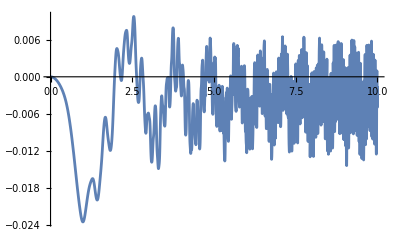

```mathematica
Plot[q1[t],{t,0,tf}]
```

```mathematica
q2[t_]=Subscript[q, 2][t]/.solTest;
```

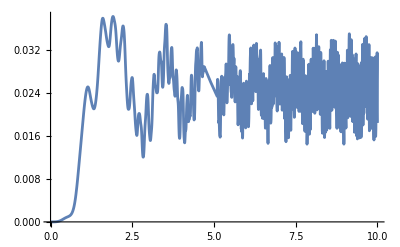

```mathematica
Plot[q2[t],{t,0,tf}]
```

```mathematica
Manipulate[ParametricPlot[{q1[t],q2[t]},{t,0,TF}],{TF,0.0001,tf,tf/10000}]
```

#### Clearing variables

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
Subscript[q, 11][t_]=.;
Subscript[Q, 1][t_]=.;
Subscript[Q, 2][t_]=.;
Subscript[Q, 3][t_]=.;
Subscript[Q, 4][t_]=.;
Subscript[Q, 5][t_]=.;
Subscript[Q, 6][t_]=.;
Subscript[Q, 7][t_]=.;
Subscript[Q, 8][t_]=.;
Subscript[Q, 9][t_]=.;
Subscript[Q, 10][t_]=.;
Subscript[Q, 11][t_]=.;
Subscript[ω, 1][t_]=.;
Subscript[ω, 2][t_]=.;
Subscript[ω, 3][t_]=.;
Subscript[ω, 4][t_]=.;
ω=.;
A=.;
B=.;
Cc=.;
r=.;
R=.;
t=.;
Ω=.;
A1=.;
A2=.;
A3=.;
A4=.;
A6=.;
A8=.;
A10=.;
B4=.;
B6=.;
B8=.;
B10=.;
b4=.;
b6=.;
b8=.;
b10=.;
```

Unset::norep: Assignment on Subscript for Q_1[t_] not found.

Unset::norep: Assignment on Subscript for Q_2[t_] not found.

Unset::norep: Assignment on Subscript for Q_3[t_] not found.

Unset::norep: Assignment on Subscript for Q_4[t_] not found.

Unset::norep: Assignment on Subscript for Q_5[t_] not found.

Unset::norep: Assignment on Subscript for Q_6[t_] not found.

Unset::norep: Assignment on Subscript for Q_7[t_] not found.

Unset::norep: Assignment on Subscript for Q_8[t_] not found.

Unset::norep: Assignment on Subscript for Q_9[t_] not found.

Unset::norep: Assignment on Subscript for Q_10[t_] not found.

Unset::norep: Assignment on Subscript for Q_11[t_] not found.

Unset::norep: Assignment on Subscript for ω_1[t_] not found.

Unset::norep: Assignment on Subscript for ω_2[t_] not found.

Unset::norep: Assignment on Subscript for ω_3[t_] not found.

Unset::norep: Assignment on Subscript for ω_4[t_] not found.

#### Energy

```mathematica
tE=∑_(k=1)^13 (PE[k]+KE[k])//.tRules//.{Ω[t]-> OM[t],Subscript[u, 1][t]-> U1[t],Subscript[u, 2][t]-> U2[t],Ω'[t]-> OMD[t],Subscript[u, 1]'[t]-> U1D[t],Subscript[u, 2]'[t]-> U2D[t]};
```

```mathematica
Cases[tE,A_[t],Infinity]//Union
Cases[tE,_Symbol,Infinity]//Union
Cases[tE,Subscript[q, n_][t],Infinity]//Union
Cases[tE,Subscript[q, n_]'[t],Infinity]//Union
```

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t],ω_1[t],ω_2[t],ω_3[t],ω_4[t]}

{r,R,t}

{q_3[t],q_4[t],q_5[t],q_6[t],q_7[t],q_8[t],q_9[t],q_10[t],q_11[t]}

{}

```mathematica
TotalE[t_]=tE;
```

```mathematica
TotalE[0]/.solTest/.{R-> 3,r->0.4}
```

272.722

```mathematica
R=3;r=0.4;
```

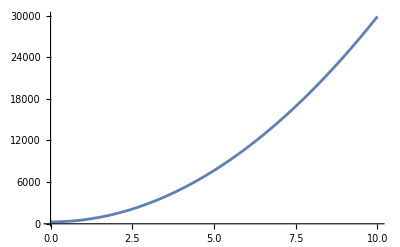

```mathematica
pL=Plot[Evaluate[tE/.solTest],{t,0,tf},PlotRange->{All,All}]
```

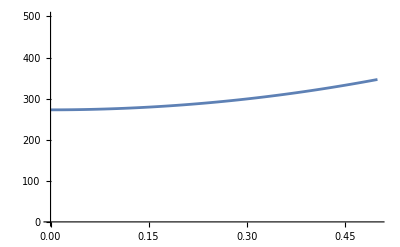

```mathematica
pL2=Plot[Evaluate[tE/.solTest],{t,0,0.5},PlotRange->{All,{0,500}}]
```

#### Plots

```mathematica
ome1[t_]=Subscript[ω, 1][t]/.solTest;
ome2[t_]=Subscript[ω, 2][t]/.solTest;
ome3[t_]=Subscript[ω, 3][t]/.solTest;
ome4[t_]=Subscript[ω, 4][t]/.solTest;
q1[t_]=Subscript[q, 1][t]/.solTest;
q2[t_]=Subscript[q, 2][t]/.solTest;
q3[t_]=Subscript[q, 3][t]/.solTest;
q4[t_]=Subscript[q, 4][t]/.solTest;
q5[t_]=Subscript[q, 5][t]/.solTest;
q6[t_]=Subscript[q, 6][t]/.solTest;
q7[t_]=Subscript[q, 7][t]/.solTest;
q8[t_]=Subscript[q, 8][t]/.solTest;
q9[t_]=Subscript[q, 9][t]/.solTest;
q10[t_]=Subscript[q, 10][t]/.solTest;
q11[t_]=Subscript[q, 11][t]/.solTest;
```

```mathematica
Po1=Plot[ome1[t],{t,0,tf},PlotLabel->ome1];
Po2=Plot[ome2[t],{t,0,tf},PlotLabel->ome2];
Po3=Plot[ome3[t],{t,0,tf},PlotLabel->ome3];
Po4=Plot[ome4[t],{t,0,tf},PlotLabel->ome4];
Pp1=Plot[q1[t],{t,0,tf},PlotLabel->q1];
Pp2=Plot[q2[t],{t,0,tf},PlotLabel->q2];
Pp3=Plot[q3[t],{t,0,tf},PlotLabel->q3];
Pp4=Plot[q4[t],{t,0,tf},PlotLabel->q4];
Pp5=Plot[q5[t],{t,0,tf},PlotLabel->q5];
Pp6=Plot[q6[t],{t,0,tf},PlotLabel->q6];
Pp7=Plot[q7[t],{t,0,tf},PlotLabel->q7];
Pp8=Plot[q8[t],{t,0,tf},PlotLabel->q8];
Pp9=Plot[q9[t],{t,0,tf},PlotLabel->q9];
Pp10=Plot[q10[t],{t,0,tf},PlotLabel->q10];
Pp11=Plot[q11[t],{t,0,tf},PlotLabel->q11];
```

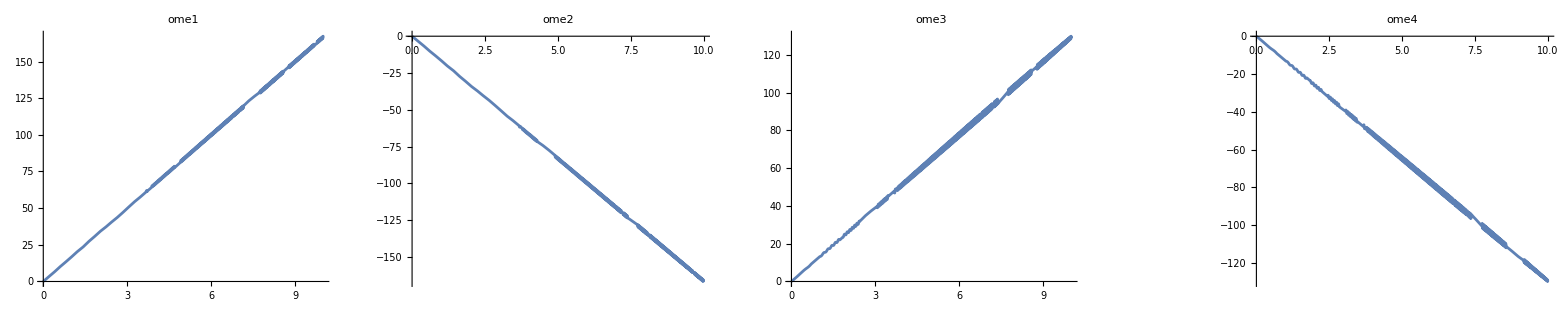

```mathematica
GraphicsRow[{Po1,Po2,Po3,,Po4}]
```

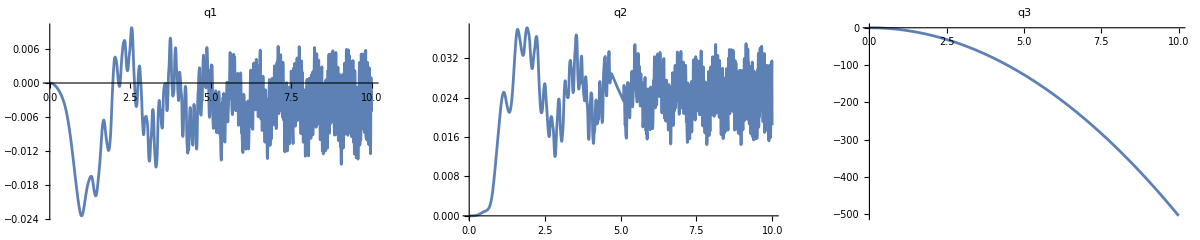

```mathematica
GraphicsRow[{Pp1,Pp2,Pp3}]
```

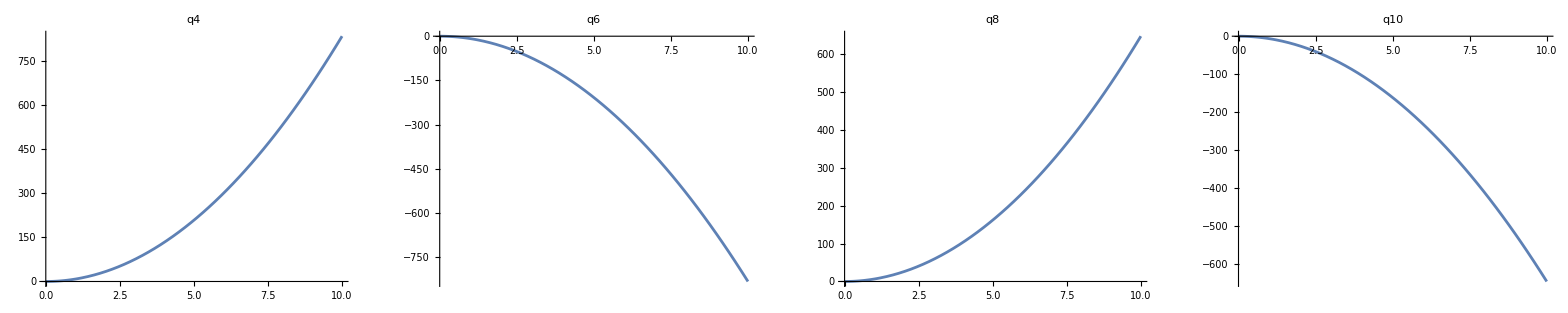

```mathematica
GraphicsRow[{Pp4,Pp6,Pp8,Pp10}]
```

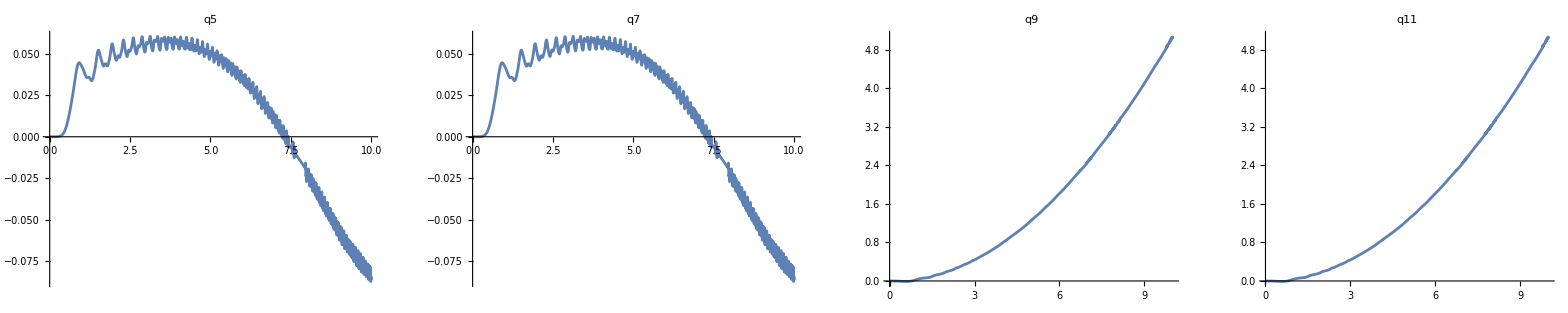

```mathematica
GraphicsRow[{Pp5,Pp7,Pp9,Pp11}]
```

#### Search for Mathematica used IC’ns

```mathematica
q1[t_]=Subscript[q, 1][t]/.solTest;
q2[t_]=Subscript[q, 2][t]/.solTest;
q3[t_]=Subscript[q, 3][t]/.solTest;
q4[t_]=Subscript[q, 4][t]/.solTest;
q5[t_]=Subscript[q, 5][t]/.solTest;
q6[t_]=Subscript[q, 6][t]/.solTest;
q7[t_]=Subscript[q, 7][t]/.solTest;
q8[t_]=Subscript[q, 8][t]/.solTest;
q9[t_]=Subscript[q, 9][t]/.solTest;
q10[t_]=Subscript[q, 10][t]/.solTest;
q11[t_]=Subscript[q, 11][t]/.solTest;
 q1pt[t_]=Subscript[q, 1]'[t]/.solTest;
q2pt[t_]=Subscript[q, 2]'[t]/.solTest;
 q3pt[t_]=Subscript[q, 3]'[t]/.solTest;
q4pt[t_]=Subscript[q, 4]'[t]/.solTest;
q5pt[t_]=Subscript[q, 5]'[t]/.solTest;
q6pt[t_]=Subscript[q, 6]'[t]/.solTest;
q7pt[t_]=Subscript[q, 7]'[t]/.solTest;
q8pt[t_]=Subscript[q, 8]'[t]/.solTest;
q9pt[t_]=Subscript[q, 9]'[t]/.solTest;
q10pt[t_]=Subscript[q, 10]'[t]/.solTest;
q11pt[t_]=Subscript[q, 11]'[t]/.solTest;
```

```mathematica
q1[0]
q2[0]
q3[0]
q4[0]
q5[0]
q6[0]
q7[0]
q8[0]
q9[0]
q10[0]
q11[0]
q1pt[0]
q2pt[0]
 q3pt[0]
q4pt[0]
q5pt[0]
q6pt[0]
q7pt[0]
q8pt[0]
q9pt[0]
q10pt[0]
q11pt[0]
```

0.

0.

0.

«6 more identical outputs»

1.65436×10^-24

0.

9.16151×10^-17

-3.15544×10^-30

-4.16334×10^-17

8.32667×10^-17

-7.88861×10^-31

0.

-7.88861×10^-31

0.

2.29092×10^-16

5.42101×10^-20

2.29092×10^-16

```mathematica
om1[t_]=Subscript[ω, 1][t]/.solTest;
om2[t_]=Subscript[ω, 2][t]/.solTest;
om3[t_]=Subscript[ω, 3][t]/.solTest;
om4[t_]=Subscript[ω, 4][t]/.solTest;
om1p[t_]=Subscript[ω, 1]'[t]/.solTest;
om2p[t_]=Subscript[ω, 2]'[t]/.solTest;
om3p[t_]=Subscript[ω, 3]'[t]/.solTest;
om4p[t_]=Subscript[ω, 4]'[t]/.solTest;
```

```mathematica
om1[0]
om2[0]
om3[0]
om4[0]
om1p[0]
om2p[0]
om3p[0]
om4p[0]
```

0.

0.

0.

«1 more identical outputs»

16.5295

-16.5515

12.8457

-12.8457

#### Dynamic Animation

```mathematica
Subscript[q, 1][t_]=Subscript[q, 1][t]/.solTest;
Subscript[q, 2][t_]=Subscript[q, 2][t]/.solTest;
Subscript[q, 3][t_]=Subscript[q, 3][t]/.solTest;
Subscript[q, 4][t_]=Subscript[q, 4][t]/.solTest;
Subscript[q, 5][t_]=Subscript[q, 5][t]/.solTest;
Subscript[q, 6][t_]=Subscript[q, 6][t]/.solTest;
Subscript[q, 7][t_]=Subscript[q, 7][t]/.solTest;
Subscript[q, 8][t_]=Subscript[q, 8][t]/.solTest;
Subscript[q, 9][t_]=Subscript[q, 9][t]/.solTest;
Subscript[q, 10][t_]=Subscript[q, 10][t]/.solTest;
Subscript[q, 11][t_]=Subscript[q, 11][t]/.solTest;
```

```mathematica
robotGraphicDynAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xA,yA,zA}],

(*Wheel graphic*)
Translate[GeometricTransformation[comwheelGraphic1,Transpose[rotB]],{xB,yB,zB}],
Translate[GeometricTransformation[barrelGraphic1,Transpose[rotC]],{xC,yC,zC}],
Translate[GeometricTransformation[comwheelGraphic2,Transpose[rotD]],{xD,yD,zD}],
Translate[GeometricTransformation[comwheelGraphic3,Transpose[rotF]],{xF,yF,zF}],
Translate[GeometricTransformation[comwheelGraphic4,Transpose[rotH]],{xH,yH,zH}]
};
```

```mathematica
robotGraphicDynAnimT[t_]=robotGraphicDynAnim;
```

```mathematica
scale=100
```

100

```mathematica
Animate[Show[Graphics3D[robotGraphicDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/1000},AnimationRunning->False]
```